```mathematica
<<EcoEvo`
SetDirectory[NotebookDirectory[]]
```

EcoEvo Package Version 1.7.1 (December 30, 2022)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

C:\Users\Koffel\Documents\Productions Scientifiques\Mes projets\NASA_Metabolic_evolution

## Tools

```mathematica
ftszlbl=12;
thicc2=Thickness[.008];
resol=200;
Colf[i_]:=ColorData[97,"ColorList"][[1+Mod[i,15]]];

(*automatically label the different variables depending on them being Substrate, Biomass, Products or Metabolites*)
lblvar[Sv_,Bv_,Pv_,Cv_]:=Table[If[MemberQ[Cv,i],Subscript["C",Position[Cv,i][[1,1]]],If[MemberQ[Sv,i],Subscript["R",Position[Sv,i][[1,1]]],If[MemberQ[Pv,i],Subscript["P",Position[Pv,i][[1,1]]],If[i==Bv,"B",{}]]]],{i,n}]
lblvar2[Sv_,Bv_,Pv_,Cv_]:=Table[Which[MemberQ[Sv,i],"Substrate",MemberQ[{Bv},i],"Biomass",MemberQ[Pv,i],"Product",MemberQ[Cv,i],"Metabolite"],{i,n}]

(*general function to represent the stoichiometric matrix as a graph*)
vf1[{xc_,yc_},name_,{w_,h_}]:=Rectangle[{xc-w,yc-h},{xc+w,yc+h}];
(*vf2[{xc_,yc_},name_,{w_,h_}]:=Circle[{xc,yc},h+w];*)
graphS[S_]:=Module[{graph=Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i,{j,in}],Table[n+i->j,{j,out}]}]
,{i,p}]]},
Graph[graph,PlotTheme->"IndexLabeled",VertexLabels->Flatten[{Table[j->Placed[lblmeta[[j]],Center],{j,n}],Table[(n+i)->Placed[Subscript[v,i],Center],{i,p}]}],VertexStyle->Flatten[{Table[j->If[MemberQ[Cv,j],LightGreen,If[MemberQ[Sv,j],LightYellow,LightOrange]],{j,n}],Table[(n+i)->LightBlue,{i,p}]}],VertexShapeFunction->Flatten[{Table[j->Automatic,{j,n}],Table[(n+i)->vf1,{i,p}]}]]]

(*Simpler graph when mostly single links; discard the energy pathways *)
graphSb[el_]:=Module[{adjM,boolM=Unitize[Normal[S[[1;;-3,el[[1;;-2]]]]]]},
adjM=boolM.Transpose[boolM];
adjM=UpperTriangularize[adjM,1]+LowerTriangularize[adjM,-1];
Show[Graphics[{EdgeForm[Directive[Thick,Green]],Opacity[.2,Green],Rectangle[{1.5,-1.5},{4.5,2.5}]}],AdjacencyGraph[adjM,PlotTheme->"Scientific",VertexLabels->Table[j->lblmeta[[j]],{j,n-2}],VertexCoordinates->{{1,0},{2,0},{3,1},{3,-1},{4,1},{3,-2},{3,2},{4,2},{4,3}}],ImagePadding->{{10,10},{10,10}}]]
```

```mathematica
(*gives the reaction rate as a generalized type II function*)
vb[i_Integer,elem_,S_,α_,μ_]:=Module[{reac=Normal[Transpose[S][[i]]],lst,reacb},
lst=Flatten[Position[reac,_?(#<0&)]];
reacb=Table[(α[[k,i]]*elem[[k]])^(-1),{k,lst}];
(Total[reacb]+μ[[i]]^(-1))^(-1)]

(*Quasy Steady State Approximation*)
QSSA[RR1_,RR2_,S_,α_,μ_]:=Module[{R1=RR1,R2=RR2,model,sol,pp=Dimensions[S][[2]]},
model={Pop[pop]->Flatten[{Table[Component[x[i]]->{Equation:>0,Color->ColorData[97,"ColorList"][[i]]},{i,{Bv}}],Table[Component[x[i]]->{Equation:>Evaluate[xin[i]+qB*S[[i]].Table[vb[j,Table[If[k==Sv[[1]],R1,If[k==Sv[[2]],R2,x[k][t]]],{k,n}],S,α,μ],{j,pp}]-If[(i==n)||(i==n-1),0,qB*x[i][t]*S[[Bv]].Table[vb[j,Table[If[k==Sv[[1]],R1,If[k==Sv[[2]],R2,x[k][t]]],{k,n}],S,α,μ],{j,pp}]]],Color->ColorData[97,"ColorList"][[i]],Type->"Intensive"},{i,Cv}]}]};
SetModel[model];
sol=EcoSim[condini,2000];
FinalSlice[sol]]

invgr[RR1_,RR2_,S_,α_,μ_]:=Module[{R1=RR1,R2=RR2,model,sol,n=Dimensions[S][[1]],p=Dimensions[S][[2]]},
(S[[Bv]].Table[vb[j,Table[If[k==Sv[[1]],R1,If[k==Sv[[2]],R2,x[k]]],{k,n}],S,α,μ],{j,p}]-m[S])/.QSSA[R1,R2,S,α,μ]]

lblR={Row[{Style["Substrate R_1",FontSize->ftszlbl],Style["",FontSlant->Italic,FontSize->ftszlbl]}],Row[{Style["Substrate R_2",FontSize->ftszlbl],Style["",FontSlant->Italic,FontSize->ftszlbl]}]};
(*color is always the same for a given subset of reactions, allows comparisons*)
PlotZNGIs[subs_,R1x_,R2x_]:=Module[{Sb=S[[1;;-1,subs]],αb,μb},
αb=α[[1;;-1,subs]];
μb=μ[[subs]];
Quiet[ContourPlot[
invgr[RR1,RR2,Sb,αb,μb]==0,{RR1,0,R1x},{RR2,0,R2x},ContourStyle->ColorData[97,"ColorList"][[1+Mod[Total[subs],15]]],
FrameLabel -> lblR]]
];

(*Similar function in spirit as above, but more adapted to eco-evo and you can pick color*)
PlotZNGIb[Sb_,αb_,μb_,R1x_,R2x_,col_]:=Module[{},
Quiet[ContourPlot[
invgr[RR1,RR2,Sb,αb,μb]==0,{RR1,0,R1x},{RR2,0,R2x},ContourStyle->col,
FrameLabel ->lblR,MaxRecursion->3]]
];

Plot3DGrowth[Sb_,αb_,μb_,R1x_,R2x_,col_]:=Module[{},
Quiet[Plot3D[
invgr[RR1,RR2,Sb,αb,μb],{RR1,0,R1x},{RR2,0,R2x},PlotStyle->col]]
];

(*function to set the QSSA model*)
SetQSSAModel[{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{},
model={Pop[pop]->Flatten[{Table[Component[x[i]]->{Equation:>0,Color->Colf[i]},{i,{Bv}}],Table[Component[x[i]]->{Equation:>Evaluate[qB*S[[i,subreac]].Table[vb[j,Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k][t]]],{k,n}],S,α,μ],{j,subreac}]-If[MemberQ[{},i],0,qB*x[i][t]*S[[Bv,GAMi]]*vb[GAMi,Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k][t]]],{k,n}],S,α,μ]]],Color->Colf[i],Type->"Intensive"},{i,Complement[Intersection[Cv,submeta],fxdi]}]}]};
SetModel[model]]

(*limiting metabolite column only works with liebig's law!*)
DisplayFinalSlice[{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_,solslice_]:=Module[{argmin,lst},{Join[{{"rate","reaction","lim. metabolite(s)"}},Sort[Transpose[{(Table[vb[j,Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}],S,α,μ],{j,subreac}]/.solslice)//N,reacnames[[subreac]],Table[lst=Flatten[Position[Normal[Transpose[S][[i]]],_?(#<0&)]];
argmin=Ordering[Flatten[{Table[(α[[k,i]]*Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}][[k]]),{k,lst}],gmax}]/.solslice,1];
Flatten[{metabo[[lst]],"max"}][[argmin]],{i,subreac}]}]]]//MatrixForm,
Join[{{"concentration","metabolite","index"}},Sort[Table[{If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],metabo[[k]],k},{k,submeta}]/.solslice]]//MatrixForm}]

edges[S_,subreac_]:=Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i,{j,in}],Table[n+i->j,{j,out}]}]
,{i,subreac}]];
edgstyle[S_,subreac_,style_]:=Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i->style[[i]],{j,in}],Table[n+i->j->style[[i]],{j,out}]}]
,{i,subreac}]];

verts[submeta_,subreac_]:=Flatten[{Table[j,{j,submeta}],Table[n+j,{j,subreac}]}];
vertstyle[submeta_,subreac_]:=Flatten[{Table[j->If[MemberQ[Cv,j],LightGreen,If[MemberQ[Sv,j],LightYellow,LightOrange]],{j,submeta}],Table[(n+i)->LightBlue,{i,subreac}]}];
vertlabels[submeta_,subreac_,metabo_,reacnames_]:=Flatten[{Table[j->Placed[metabo[[j]],Center],{j,submeta}],Table[(n+i)->Placed[reacnames[[i]],Center],{i,subreac}]}];

vf1[{xc_,yc_},name_,{w_,h_}]:=Rectangle[{xc-w,yc-h},{xc+w,yc+h}];
GraphMetabNet[{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},coord_,szvtx_,szim_]:=Graph[verts[submeta,subreac],edges[S,subreac],
VertexLabels->vertlabels[submeta,subreac,metabo,reacnames],
PlotTheme->"IndexLabeled",
VertexStyle->vertstyle[submeta,subreac],VertexSize->{"Scaled",szvtx},
(*VertexShapeFunction->Flatten[{Table[j->Automatic,{j,submeta}],Table[(n+i)->vf1,{i,subreac}]}],*)
VertexCoordinates->If[ToString[coord]=="Automatic",Automatic,Flatten[{Table[j->coord[[j]],{j,submeta}],Table[(n+i)->coord[[n+i]],{i,subreac}]}]],
VertexShapeFunction->Flatten[{Table[j->Automatic,{j,submeta}],Table[(n+i)->vf1,{i,subreac}]}],ImageSize->szim]

gmax=5;

(*graphic directive: attribute a single classic mathematica color to each integer*)
Colf[i_]:=ColorData[97,"ColorList"][[1+Mod[i,15]]];

vb[i_Integer,elem_,S_,α_,μ_]:=Module[{reac=Normal[Transpose[S][[i]]],lst,reacb},
lst=Flatten[Position[reac,_?(#<0&)]];
reacb=Table[(α[[k,i]]*elem[[k]]),{k,lst}];
μ[[i]]*Min[reacb,gmax]]
edges[S_,subreac_]:=Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i,{j,in}],Table[n+i->j,{j,out}]}]
,{i,subreac}]];
edgstyle[S_,subreac_,style_]:=Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i->style[[i]],{j,in}],Table[n+i->j->style[[i]],{j,out}]}]
,{i,subreac}]];

verts[submeta_,subreac_]:=Flatten[{Table[j,{j,submeta}],Table[n+j,{j,subreac}]}];
vertstyle[submeta_,subreac_]:=Flatten[{Table[j->If[MemberQ[Cv,j],LightGreen,If[MemberQ[Sv,j],LightYellow,LightOrange]],{j,submeta}],Table[(n+i)->LightBlue,{i,subreac}]}];
vertlabels[submeta_,subreac_,metabo_,reacnames_]:=Flatten[{Table[j->Placed[metabo[[j]],Center],{j,submeta}],Table[(n+i)->Placed[reacnames[[i]],Center],{i,subreac}]}];

vf1[{xc_,yc_},name_,{w_,h_}]:=Rectangle[{xc-w,yc-h},{xc+w,yc+h}];
GraphMetabNet[{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},coord_,szvtx_,szim_]:=Graph[verts[submeta,subreac],edges[S,subreac],
VertexLabels->vertlabels[submeta,subreac,metabo,reacnames],
PlotTheme->"IndexLabeled",
VertexStyle->vertstyle[submeta,subreac],VertexSize->{"Scaled",szvtx},
(*VertexShapeFunction->Flatten[{Table[j->Automatic,{j,submeta}],Table[(n+i)->vf1,{i,subreac}]}],*)
VertexCoordinates->If[ToString[coord]=="Automatic",Automatic,Flatten[{Table[j->coord[[j]],{j,submeta}],Table[(n+i)->coord[[n+i]],{i,subreac}]}]],
VertexShapeFunction->Flatten[{Table[j->Automatic,{j,submeta}],Table[(n+i)->vf1,{i,subreac}]}],ImageSize->szim]
```

## Toy model with Leibig’s law

### General tools

```mathematica
gmax=5;

(*graphic directive: attribute a single classic mathematica color to each integer*)
Colf[i_]:=ColorData[97,"ColorList"][[1+Mod[i,15]]];

vb[i_Integer,elem_,S_,α_,μ_]:=Module[{reac=Normal[Transpose[S][[i]]],lst,reacb},
lst=Flatten[Position[reac,_?(#<0&)]];
reacb=Table[(α[[k,i]]*elem[[k]]),{k,lst}];
μ[[i]]*Min[reacb,gmax]]
```

```mathematica
edges[S_,subreac_]:=Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i,{j,in}],Table[n+i->j,{j,out}]}]
,{i,subreac}]];
edgstyle[S_,subreac_,style_]:=Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i->style[[i]],{j,in}],Table[n+i->j->style[[i]],{j,out}]}]
,{i,subreac}]];

verts[submeta_,subreac_]:=Flatten[{Table[j,{j,submeta}],Table[n+j,{j,subreac}]}];
vertstyle[submeta_,subreac_]:=Flatten[{Table[j->If[MemberQ[Cv,j],LightGreen,If[MemberQ[Sv,j],LightYellow,LightOrange]],{j,submeta}],Table[(n+i)->LightBlue,{i,subreac}]}];
vertlabels[submeta_,subreac_,metabo_,reacnames_]:=Flatten[{Table[j->Placed[metabo[[j]],Center],{j,submeta}],Table[(n+i)->Placed[reacnames[[i]],Center],{i,subreac}]}];

vf1[{xc_,yc_},name_,{w_,h_}]:=Rectangle[{xc-w,yc-h},{xc+w,yc+h}];
GraphMetabNet[{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},coord_,szvtx_,szim_]:=Graph[verts[submeta,subreac],edges[S,subreac],
VertexLabels->vertlabels[submeta,subreac,metabo,reacnames],
PlotTheme->"IndexLabeled",
VertexStyle->vertstyle[submeta,subreac],VertexSize->{"Scaled",szvtx},
(*VertexShapeFunction->Flatten[{Table[j->Automatic,{j,submeta}],Table[(n+i)->vf1,{i,subreac}]}],*)
VertexCoordinates->If[ToString[coord]=="Automatic",Automatic,Flatten[{Table[j->coord[[j]],{j,submeta}],Table[(n+i)->coord[[n+i]],{i,subreac}]}]],
VertexShapeFunction->Flatten[{Table[j->Automatic,{j,submeta}],Table[(n+i)->vf1,{i,subreac}]}],ImageSize->szim]
```

### Initialization of the Toy model

```mathematica
(*raw metabolic network, encoded by non-zero stoichiometric coefficients*)
reacs={
{1,1}->-1,{2,1}->1,                              (*R1 uptake, transformed into q1; no ATP cost yet*)
{3,2}->-1,{4,2}->1,                              (*R2 uptake, transformed into q2; no ATP cost yet*)
{2,3}->-1,{4,3}->-1,{5,3}->1       (*growth, transforms q1 and q2 into biomass; no ATP cost yet*)
}

(* labeling who's who: extracellular metabolite, biomass component, products (not necessary?) and intracellular metabolite *)
Sv={1,3};  (*external substrates R1 and R2*)
Bv=5;            (*biomass*)
Pv={};          (*excreted products (not in the model)*)
Cv={2,4};  
(*internal metabolites q1 and q2*)
```

{{1,1}→-1,{2,1}→1,{3,2}→-1,{4,2}→1,{2,3}→-1,{4,3}→-1,{5,3}→1}

```mathematica
(*temporary number of dynamical variable*)
n=Dimensions[SparseArray[reacs]][[1]]
(*number of reactions*)
p=Dimensions[SparseArray[reacs]][[2]];

(*the speed at which ATP is regenerated from ADP*)
ADPeff=1;
(*amount of mass balanced ATP/ADP*)
massbal0=2;
(*Do[S2[[i,13]]=S2[[i,13]]+2*massbal0,{i,{13,50}}]*)

(*single out the biomass creating reaction*)
GAMi=p;
(*add the energy regeneration pathway: automatic pump from ADP to ATP, could be tweaked*)
(*also add the energy cost to each react, using one ATP to make one ADP*)
(*also adds the net creation of ADP by the biomass reaction, to ensure mass balance of ATP+ADP through growth; note: biomass reaction has to be encoded as reaction No GAMi*)
energy=Flatten[{Table[If[k≠GAMi,{{n+1,k}->1,{n+2,k}->-1},{{n+1,k}->1+2*massbal0,{n+2,k}->-1}],{k,1,p}],{n+1,p+1}->-1,{n+2,p+1}->1}]
(*indices of the conserved metabolites*)
Mv={n+1,n+2}

(*new matrix with ATP/ADP*)
S=SparseArray[Sort[Flatten[{reacs,energy}],#1[[1,2]]<#2[[1,2]]&]];
S//MatrixForm

(*number of dynamical variable*)
n=Dimensions[SparseArray[S]][[1]]
(*number of reactions*)
p=Dimensions[SparseArray[S]][[2]];
Cv=Flatten[{Cv,{n-1,n}}]
```

5

{{6,1}→1,{7,1}→-1,{6,2}→1,{7,2}→-1,{6,3}→5,{7,3}→-1,{6,4}→-1,{7,4}→1}

{6,7}

(-1 | 0 | 0 | 0
1 | 0 | -1 | 0
0 | -1 | 0 | 0
0 | 1 | -1 | 0
0 | 0 | 1 | 0
1 | 1 | 5 | -1
-1 | -1 | -1 | 1)

7

{2,4,6,7}

```mathematica
(*BUILDING α AND μ, THE REACTION RATES COEFFICIENTS *)
(*locate all reactants for each reaction*)
input=Position[Normal[S],_?(#<0&)];
(*(*randomly generated parameters*)
α=SparseArray[Table[k->RandomReal[],{k,input}]];
α//MatrixForm;
μ=Table[3*RandomReal[],{k,p}];*)
(*pick all coefficients equal to one*)
α=SparseArray[Table[k->1,{k,input}]];
α//MatrixForm;
μ=Table[1,{k,p}];
(*EXCEPT energy pump*)
μ[[4]]=ADPeff;
```

```mathematica
metabo={"R_1","q_1","R_2","q_2","B","ADP","ATP"}
reacnames={"R1aq","R2aq","GAM","EN"}

metabo={"R_1","q_1","R_2","q_2","N","q_ADP","q_ATP"}
reacnames={"v_1","v_2","v_G","v_E"}

metabo2={"R_1","q_1","R_2","q_2","N","q_ADP","q_ATP"}
reacnames2={"v_1","v_2","v_G","v_E"}
(*metabo2={"R_1","q_1","R_2","q_2","B","q_3","q_4"}
reacnames2={"v_1","v_2","v_4","v_3"}*)
Inactivate[D["",t]].MatrixForm[metabo2]==MatrixForm[S].MatrixForm[Table[Subscript[v,i],{i,p}]]
subm={2,4,6,7}
Inactivate[D["",t]].MatrixForm[metabo2[[subm]]]==MatrixForm[S[[subm,{1,2,3,4}]]].MatrixForm[reacnames2[[{1,2,3,4}]]]

submeta=Range[1,n]
subreac=Range[1,p]
label=lblvar2[Sv,Bv,Pv,Cv]
(*graphS[S];
graphtwor=GraphMetabNet[S,Range[1,n],Range[1,p],metabo,reacnames,Automatic,0.055,400]*)

(*define the general system*)
system={S,metabo,reacnames,submeta,subreac,α,μ};

coordsub={{-2,-1},{-1,1},{2,-1},{1,1},{0,2},{-.5,.5},{.5,.5},{-1,0},{1,0},{0,1},{0,0}}
vtxsz=.07;
(*imgsz=300;*)
imgsz=400;
system2={S,metabo2,reacnames2,submeta,subreac,α,μ};
graphtwor=GraphMetabNet[system2,coordsub,vtxsz,imgsz]
Export[StringJoin["figures/graph2essen.png"],graphtwor,"PNG"];
Export[StringJoin["figures/graph2essen.pdf"],graphtwor,"PDF"];
```

{R_1,q_1,R_2,q_2,B,ADP,ATP}

{R1aq,R2aq,GAM,EN}

{R_1,q_1,R_2,q_2,N,q_ADP,q_ATP}

{v_1,v_2,v_G,v_E}

{R_1,q_1,R_2,q_2,N,q_ADP,q_ATP}

{v_1,v_2,v_G,v_E}

Inactivet.(R_1
q_1
R_2
q_2
N
q_ADP
q_ATP)==(-1 | 0 | 0 | 0
1 | 0 | -1 | 0
0 | -1 | 0 | 0
0 | 1 | -1 | 0
0 | 0 | 1 | 0
1 | 1 | 5 | -1
-1 | -1 | -1 | 1).(v_1
v_2
v_3
v_4)

{2,4,6,7}

Inactivet.(q_1
q_2
q_ADP
q_ATP)==(1 | 0 | -1 | 0
0 | 1 | -1 | 0
1 | 1 | 5 | -1
-1 | -1 | -1 | 1).(v_1
v_2
v_G
v_E)

{1,2,3,4,5,6,7}

{1,2,3,4}

{Substrate,Metabolite,Substrate,Metabolite,Biomass,Metabolite,Metabolite}

{{-2,-1},{-1,1},{2,-1},{1,1},{0,2},{-0.5,0.5},{0.5,0.5},{-1,0},{1,0},{0,1},{0,0}}

-Graphics-

```mathematica
GraphMetabNet[{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},coord_,szvtx_,szim_]:=Graph[verts[submeta,subreac],edges[S,subreac],
VertexLabels->vertlabels[submeta,subreac,metabo,reacnames],
PlotTheme->"IndexLabeled",
VertexStyle->vertstyle[submeta,subreac],VertexSize->{"Scaled",szvtx},
(*VertexShapeFunction->Flatten[{Table[j->Automatic,{j,submeta}],Table[(n+i)->vf1,{i,subreac}]}],*)
VertexCoordinates->If[ToString[coord]=="Automatic",Automatic,Flatten[{Table[j->coord[[j]],{j,submeta}],Table[(n+i)->coord[[n+i]],{i,subreac}]}]],
VertexShapeFunction->Flatten[{Table[j->vf1,{j,submeta}],Table[(n+i)->Automatic,{i,subreac}]}],ImageSize->szim]
```

```mathematica
graphtwor=GraphMetabNet[system2,coordsub,vtxsz,imgsz]
Export[StringJoin["figures/graph2essen.png"],graphtwor,"PNG"];
Export[StringJoin["figures/graph2essen.pdf"],graphtwor,"PDF"];
```

-Graphics-

```mathematica
reacnames={"v_1","v_2","μ","v_E"}
system={S,metabo,reacnames,submeta,subreac,α,μ};
```

{v_1,v_2,μ,v_E}

### Simulating the network

```mathematica
(*WARNING, MAKE SURE S IS REPLACED BY S2 EVERYWHERE*)
```

#### Setting the parameters

```mathematica
(*mortality function, potentially penalized by the number of reactions in the metabolic network (trade-off)*)
c=0;
m0=.1;
m[S_]:=m0+c*Dimensions[SparseArray[S]][[2]];

(*stoichiometric coefficient converting cell number into metabolite concentrations*)
qB=1;

(*building the supply vectors*)
Clear[xin]
(*list of all the extracellular metabolites in the Glycolysis pathway*)
Intersection[Sv,submeta]
essent={1,3};
metabo[[essent]]

(*DEBUGGING TOOL ONLY; fxdi={} does not do anything*)
(*pick some metabolites and set them at fixed value*)
Table[{k,metabo[[k]]},{k,Cv}];
fxdi={};
fxdval=.1;

(*set all the essential metbolites to 1 by default*)
xin=Table[0,{i,n}];
Do[xin[[i]]=1.,{i,essent}];
```

{1,3}

{R_1,R_2}

#### Simulating equilibration of the internal dynamics

```mathematica
(*function to set the QSSA model*)
SetQSSAModel[{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{},
model={Pop[pop]->Flatten[{Table[Component[x[i]]->{Equation:>0,Color->Colf[i]},{i,{Bv}}],Table[Component[x[i]]->{Equation:>Evaluate[qB*S[[i,subreac]].Table[vb[j,Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k][t]]],{k,n}],S,α,μ],{j,subreac}]-If[MemberQ[{},i],0,qB*x[i][t]*S[[Bv,GAMi]]*vb[GAMi,Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k][t]]],{k,n}],S,α,μ]]],Color->Colf[i],Type->"Intensive"},{i,Complement[Intersection[Cv,submeta],fxdi]}]}]};
SetModel[model]]

(*limiting metabolite column only works with liebig's law!*)
DisplayFinalSlice[{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_,solslice_]:=Module[{argmin,lst},{Join[{{"rate","reaction","lim. metabolite(s)"}},Sort[Transpose[{(Table[vb[j,Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}],S,α,μ],{j,subreac}]/.solslice)//N,reacnames[[subreac]],Table[lst=Flatten[Position[Normal[Transpose[S][[i]]],_?(#<0&)]];
argmin=Ordering[Flatten[{Table[(α[[k,i]]*Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}][[k]]),{k,lst}],gmax}]/.solslice,1];
Flatten[{metabo[[lst]],"max"}][[argmin]],{i,subreac}]}]]]//MatrixForm,
Join[{{"concentration","metabolite","index"}},Sort[Table[{If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],metabo[[k]],k},{k,submeta}]/.solslice]]//MatrixForm}]
```

```mathematica
(*glucose set to .1, to make it the limiting factor*)
xin[[1]]=.1;

(*SET THE INITIAL CONDITION*)
(*non-supplied extracell metabolites start at 0 concentration, supplied start at the value at which they are supplied (will stay there)*)
(*biomass starts at .1 (does not matter, no dynamics) *)
(*All intracellular metabolites are set at 1, except the conserved ones set at the SAME value as in the stoichiometric matrix (to ensure they are conserved)*)
condini=Table[If[MemberQ[Sv,i],If[xin[[i]]==0,x[i]->0,x[i]->xin[[i]]],If[i==Bv,x[i]->.1,If[MemberQ[Mv,i],x[i]->massbal0,x[i]->1]]],{i,n}];

(*gather all of the important bits into a simgle object*)
system={S,metabo,reacnames,submeta,subreac,α,μ};
(*build the Quasi Steasy State dynamics: total population stays put, metabolites respond to fixed extracellular concentrations, eventually equilibrate due to dilution by growth*)
SetQSSAModel[system,xin]

sub=Complement[submeta,fxdi];

(*DISPLAYS THE *)
MatrixForm[model[[1,2,1+Flatten[Table[Position[Table[i,{i,Complement[Intersection[Cv,submeta],fxdi]}],i],{i,sub}]]]],TableAlignments->Left]

tmax=300;
sol=EcoSim[condini,tmax];

figtraj=PlotDynamics[sol,Table[x[i],{i,Intersection[sub,Cv]}],Logged->True,PlotLegends->metabo[[Intersection[sub,Cv]]],AxesLabel->{"time",""}]
DisplayFinalSlice[system,xin,FinalSlice[sol]]
```

```mathematica
xin[[1]]=.9;
condini=Table[If[MemberQ[Sv,i],If[xin[[i]]==0,x[i]->0,x[i]->xin[[i]]],If[i==Bv,x[i]->.1,If[MemberQ[Mv,i],x[i]->massbal0,x[i]->1]]],{i,n}];
SetQSSAModel[system,xin]

tmax=300;
sol=EcoSim[condini,tmax];
fslice=FinalSlice[sol];

figtraj=PlotDynamics[sol,Table[x[i],{i,Intersection[sub,Cv]}],Logged->True,PlotLegends->metabo[[Intersection[sub,Cv]]],AxesLabel->{"time",""}]
DisplayFinalSlice[system,xin,FinalSlice[sol]]
```

### Linear algebra approach (most coef to 1)

#### Tools

```mathematica
GraphMetabNetLim[limcb_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},coord_,style_,szvtx_,szim_]:=
Module[{arwsz=szim*.8*10^(-4)},
Graph[verts[submeta,subreac],edges[S,subreac],
VertexLabels->vertlabels[submeta,subreac,metabo,reacnames],
PlotTheme->"IndexLabeled",
VertexStyle->vertstyle[submeta,subreac],VertexSize->{"Scaled",szvtx},
EdgeStyle->Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i->{If[j==limcb[[Position[subreac,i][[1,1]],2]],style,Automatic],Arrowheads[arwsz]},{j,in}],Table[n+i->j->{If[MemberQ[{Bv},j]&&Length[Intersection[Sv,Transpose[limcb][[2]]]]≠0,style,If[MemberQ[Transpose[limcb][[2]],j]&&Not[MemberQ[Sv,j]],style,Automatic]],Arrowheads[arwsz]},{j,out}]}]
,{i,subreac}]],
VertexCoordinates->If[ToString[coord]=="Automatic",Automatic,Flatten[{Table[j->coord[[j]],{j,submeta}],Table[(n+i)->coord[[n+i]],{i,subreac}]}]],
VertexShapeFunction->Flatten[{Table[j->vf1,{j,submeta}],Table[(n+i)->Automatic,{i,subreac}]}],ImageSize->szim]]

(*GraphMetabNetLoop[limcb_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_,coord_,style1_,style2_,szvtx_,szim_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,Sacl,reprod,rvaleq,aclmeta,aclreac},
{subS,Lim,P}=PopMatrixSetup[limcb,{S,metabo,reacnames,submeta,subreac,α,μ},xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},{S,metabo,reacnames,submeta,subreac,α,μ}];
(*find the reactions contributing to the autocatalytic loop*)
rvaleq=Transpose[subS].le;
aclreac=Flatten[Position[rvaleq,_?Positive]];

(*find the metabolites contributing to the autocatalytic loop*)
reprod=P.le;
reprod[[Sv]]=0;
aclmeta=Flatten[Position[reprod,_?Positive]];
(*manually add the extracell metabo in the loop if: biomass is involved in the autocatalytic loop, and they are limiting a reaction from the autocatalytic loop*)
Sacl=If[MemberQ[aclmeta,Bv],Intersection[Select[limcb,MemberQ[aclreac,#[[1]]]&][[1;;-1,2]],Sv],{}];
aclmeta=Sort[Join[aclmeta,Sacl]];

Graph[verts[submeta,subreac],edges[S,subreac],
VertexLabels->vertlabels[submeta,subreac,metabo,reacnames],
PlotTheme->"IndexLabeled",
VertexStyle->vertstyle[submeta,subreac],VertexSize->{"Scaled",szvtx},
EdgeStyle->Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i->If[MemberQ[aclreac,i]&&MemberQ[aclmeta,j]&&j==limcb[[Position[subreac,i][[1,1]],2]],style1,style2],{j,in}],Table[n+i->j->If[MemberQ[aclreac,i]&&MemberQ[aclmeta,j],style1,style2],{j,out}]}]
,{i,subreac}]],
VertexCoordinates->If[ToString[coord]=="Automatic",Automatic,Flatten[{Table[j->coord[[j]],{j,submeta}],Table[(n+i)->coord[[n+i]],{i,subreac}]}]],
VertexShapeFunction->Flatten[{Table[j->Automatic,{j,submeta}],Table[(n+i)->vf1,{i,subreac}]}],ImageSize->szim]]*)

tol=10^(-9);
(*NEW adapted to glycolysis from the toy model (convert indices to submeta)*)
(*GraphMetabNetLoop[limcb_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_,coord_,style1_,style2_,szvtx_,szim_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,Sacl,reprod,rvaleq,aclmeta,aclreac,arwsz=szim*.8*10^(-4)},
{subS,Lim,P}=PopMatrixSetup[limcb,{S,metabo,reacnames,submeta,subreac,α,μ},xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},{S,metabo,reacnames,submeta,subreac,α,μ}];
(*find the reactions contributing to the autocatalytic loop*)
(*rvaleq=Chop[Transpose[subS].le,tol];*)
rvaleq=Chop[grad,tol];
aclreac=subreac[[Flatten[Position[rvaleq,_?Positive]]]];
(*find the metabolites contributing to the autocatalytic loop*)
reprod=Chop[P.le,tol];
(*complement gets rid of the *)
aclmeta=Complement[submeta[[Flatten[Position[reprod,_?Positive]]]],Sv];
(*manually add the extracell metabo in the loop if: biomass is involved in the autocatalytic loop, and they are limiting a reaction from the autocatalytic loop*)
Sacl=If[MemberQ[aclmeta,Bv],Intersection[Select[limcb,MemberQ[aclreac,#[[1]]]&][[1;;-1,2]],Sv],{}];
aclmeta=Sort[Join[aclmeta,Sacl]];
Graph[verts[submeta,subreac],edges[S,subreac],
VertexLabels->vertlabels[submeta,subreac,metabo,reacnames],
PlotTheme->"IndexLabeled",
VertexStyle->vertstyle[submeta,subreac],VertexSize->{"Scaled",szvtx},
EdgeStyle->Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i->{If[MemberQ[aclreac,i]&&MemberQ[aclmeta,j]&&j==limcb[[Position[subreac,i][[1,1]],2]],style1,style2],Arrowheads[arwsz]},{j,in}],Table[n+i->j->{If[MemberQ[aclreac,i]&&MemberQ[aclmeta,j],style1,style2],Arrowheads[arwsz]},{j,out}]}]
,{i,subreac}]],
VertexCoordinates->If[ToString[coord]=="Automatic",Automatic,Flatten[{Table[j->coord[[j]],{j,submeta}],Table[(n+i)->coord[[n+i]],{i,subreac}]}]],
VertexShapeFunction->Flatten[{Table[j->vf1,{j,submeta}],Table[(n+i)->Automatic,{i,subreac}]}],ImageSize->szim]]*)
arwcf=.8*10^(-4);
arwcf2=.8*10^(-4);
GraphMetabNetLoop[limcb_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_,coord_,style1_,style2_,style3_,szvtx_,szim_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,Sacl,Sinhib,reprod,rvaleq,aclmeta,aclreac,inhreac,inhmeta,arwsz=szim*arwcf2,arwsz2=szim*arwcf},
{subS,Lim,P}=PopMatrixSetup[limcb,{S,metabo,reacnames,submeta,subreac,α,μ},xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},{S,metabo,reacnames,submeta,subreac,α,μ}];
(*find the reactions contributing to the autocatalytic loop*)
(*rvaleq=Chop[Transpose[subS].le,tol];*)
rvaleq=Chop[grad,tol];
aclreac=subreac[[Flatten[Position[rvaleq,_?Positive]]]];
inhreac=subreac[[Flatten[Position[rvaleq,_?Negative]]]];
(*find the metabolites contributing to the autocatalytic loop*)
reprod=Chop[P.le,tol];
(*complement gets rid of the *)
aclmeta=Complement[submeta[[Flatten[Position[reprod,_?Positive]]]],Sv];
inhmeta=Complement[submeta[[Flatten[Position[reprod,_?Negative]]]],Sv];
(*manually add the extracell metabo in the loop if: biomass is involved in the autocatalytic loop, and they are limiting a reaction from the autocatalytic loop*)
Sacl=If[MemberQ[aclmeta,Bv],Intersection[Select[limcb,MemberQ[aclreac,#[[1]]]&][[1;;-1,2]],Sv],{}];
aclmeta=Sort[Join[aclmeta,Sacl]];
Sinhib=Intersection[Select[limcb,MemberQ[inhreac,#[[1]]]&][[1;;-1,2]],Sv];
inhmeta=Sort[Join[inhmeta,Sinhib]];
Graph[verts[submeta,subreac],edges[S,subreac],
VertexLabels->vertlabels[submeta,subreac,metabo,reacnames],
PlotTheme->"IndexLabeled",
VertexStyle->vertstyle2[submeta,subreac,aclmeta,aclreac,inhmeta,inhreac,style1,style3],VertexSize->{"Scaled",szvtx},
EdgeStyle->Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i->If[MemberQ[aclreac,i]&&MemberQ[aclmeta,j]&&j==limcb[[Position[subreac,i][[1,1]],2]],{style1,Arrowheads[arwsz]},If[MemberQ[inhreac,i]&&(j==limcb[[Position[subreac,i][[1,1]],2]]||MemberQ[aclmeta,j]),{style3,Arrowheads[arwsz]},{style2,Arrowheads[arwsz2]}]],{j,in}],Table[n+i->j->If[MemberQ[aclreac,i]&&MemberQ[aclmeta,j],{style1,Arrowheads[arwsz]},If[MemberQ[inhreac,i]&&MemberQ[inhmeta,j],{style3,Arrowheads[arwsz]},{style2,Arrowheads[arwsz2]}]],{j,out}]}]
,{i,subreac}]],
VertexCoordinates->If[ToString[coord]=="Automatic",Automatic,Flatten[{Table[j->coord[[j]],{j,submeta}],Table[(n+i)->coord[[n+i]],{i,subreac}]}]],
VertexShapeFunction->Flatten[{Table[j->vf1,{j,submeta}],Table[(n+i)->Automatic,{i,subreac}]}],ImageSize->szim]]

vertstyle2[submeta_,subreac_,aclmeta_,aclreac_,inhmeta_,inhreac_,style1_,style3_]:=Flatten[{Table[j->If[MemberQ[Cv,j],If[MemberQ[aclmeta,j],{LightGreen,EdgeForm[style1]},If[MemberQ[inhmeta,j],{LightGreen,EdgeForm[style3]},LightGreen]],If[MemberQ[Sv,j],If[MemberQ[aclmeta,j],{LightYellow,EdgeForm[style1]},If[MemberQ[inhmeta,j],{LightYellow,EdgeForm[style3]},LightYellow]],If[MemberQ[aclmeta,j],{LightOrange,EdgeForm[style1]},LightOrange]]],{j,submeta}],Table[(n+i)->If[MemberQ[aclreac,i],{LightBlue,EdgeForm[style1]},If[MemberQ[inhreac,i],{LightBlue,EdgeForm[style3]},LightBlue]],{i,subreac}]}];

ListLim[S_,subreac_]:=Module[{row},
Table[row=Position[Normal[S[[All,subreac[[i]]]]],_?(#<0&)];Table[{subreac[[i]],j[[1]]},{j,row}],{i,Length[subreac]}]]

GenerateLimRegimes[S_,subreac_]:=Module[{combi},
combi=ListLim[S,subreac];
Tuples[combi]]

PopMatrixSetup[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P},
subS=IntegerPart[S[[Join[Intersection[Cv,submeta],{Bv}],subreac]]];
(*Let's make the limitation matrix now*)
Lim=ConstantArray[0,{Length[subreac],Length[submeta]}];
Do[Lim[[Position[subreac,i[[1]]][[1]],Position[submeta,i[[2]]][[1]]]]=μ[[i[[1]]]]*α[[i[[2]],i[[1]]]],{i,limcombi}];
(*now we need to make the matrix that sends all non-internal substrates onto biomass*)
P=ConstantArray[0,{Length[submeta],Length[Join[Intersection[Cv,submeta],{Bv}]]}];
Do[If[MemberQ[Sv,submeta[[i]]],P[[i,-1]]=xin[[submeta[[i]]]],P[[i,Position[Join[Intersection[Cv,submeta],{Bv}],submeta[[i]]][[1]]]]=1],{i,Length[submeta]}];{subS,Lim,P}]

MakePopMatrix[{subS_,Lim_,P_}]:=subS.Lim.P;

(*LifeCycle[A_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},style_,cordstyle_,szvtx_,szim_]:=Module[{lifecyc,autoloop,edg},
lifecyc=Graph[submeta,Table[Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]],{t,Position[Normal[A],_?(#>0&)]}]];
autoloop=DeleteDuplicates[Flatten[FindCycle[lifecyc,Infinity,All]]];
Graph[submeta,Table[Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]],{t,Position[Normal[A],_?(#>0&)]}],
EdgeStyle->Table[edg=Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]];edg->If[MemberQ[autoloop,edg],style,Automatic],{t,Position[Normal[A],_?(#>0&)]}],
PlotTheme->"IndexLabeled",
VertexCoordinates->cordstyle[[1;;Length[submeta]]],
VertexStyle->Table[j->If[MemberQ[Cv,j],LightGreen,If[MemberQ[Sv,j],LightYellow,LightOrange]],{j,submeta}],
VertexSize->{"Scaled",szvtx},VertexLabels->Table[j->Placed[metabo[[j]],Center],{j,submeta}],ImageSize->szim]]*)

LifeCycle[A_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},style_,cordstyle_,szvtx_,szim_]:=Module[{lifecyc,autoloop,edg,submetab=Complement[submeta,Sv]},
lifecyc=Graph[submeta,Table[Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]],{t,Position[Normal[A],_?(#>0&)]}]];
autoloop=DeleteDuplicates[Flatten[FindCycle[lifecyc,Infinity,All]]];
Graph[submetab,Table[Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]],{t,Position[Normal[A],_?(#>0&)]}],
EdgeStyle->Table[edg=Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]];edg->If[MemberQ[autoloop,edg],style,Automatic],{t,Position[Normal[A],_?(#>0&)]}],
PlotTheme->"IndexLabeled",
VertexCoordinates->cordstyle[[submetab]],
VertexStyle->Table[j->If[MemberQ[Cv,j],LightGreen,If[MemberQ[Sv,j],LightYellow,LightOrange]],{j,submetab}],
VertexSize->{"Scaled",szvtx},VertexLabels->Table[j->Placed[metabo[[j]],Center],{j,submetab}],ImageSize->szim]]

(*this new version should work same as the previous one; BUT DOESNT?*)
LifeCycle[A_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},style_,cordstyle_,szvtx_,szim_]:=Module[{lifecyc,autoloop,edg,submetab=Complement[submeta,Sv]},
lifecyc=Graph[submeta,Table[Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]],{t,Position[Normal[A],_?(#>0&)]}]];
autoloop=DeleteDuplicates[Flatten[FindCycle[lifecyc,Infinity,All]]];
Graph[submetab,Table[Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]],{t,Position[Normal[A],_?(#>0&)]}],
EdgeStyle->Table[edg=Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]];edg->If[MemberQ[autoloop,edg],style,Automatic],{t,Position[Normal[A],_?(#>0&)]}],
PlotTheme->"IndexLabeled",
VertexCoordinates->cordstyle[[1;;Length[submeta]]],
VertexStyle->Table[j->If[MemberQ[Cv,j],LightGreen,If[MemberQ[Sv,j],LightYellow,LightOrange]],{j,submetab}],
VertexSize->{"Scaled",szvtx},VertexLabels->Table[j->Placed[metabo[[j]],Center],{j,submetab}],ImageSize->szim]]

FindQSS[{subS_,Lim_,P_},{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_}]:=Module[{eig,A,λ,re,le,veq,rvaleq,μeq,grad},
A=MakePopMatrix[{subS,Lim,P}];
eig=Eigensystem[A,1,Method->{"Arnoldi","Criteria"->"RealPart"}]//N;
λ=eig[[1,1]];
re=eig[[2,1,1;;-1]]/eig[[2,1,-1]];
le=Eigensystem[Transpose[A],1,Method->{"Arnoldi","Criteria"->"RealPart"}][[2,1]];
le=Chop[le/(le.re)];
veq=Lim.P.re;
rvaleq=Transpose[subS].le;
μeq=Table[μ[[j]],{j,subreac}];
grad=Table[rvaleq[[j]]*veq[[j]]/μeq[[j]],{j,Length[veq]}];
{λ,re,le,veq,grad}]

FindLimMetabo[{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_,P_,re_,le_]:=Module[{metabeq,limsubstr,lst,reac,ix,substr,argmin},
metabeq=Table[{submeta[[k]],metabo[[submeta[[k]]]],If[MemberQ[Sv,submeta[[k]]],xin[[submeta[[k]]]],If[MemberQ[fxdi,submeta[[k]]],fxdval,(P.re)[[k]]]],If[MemberQ[Sv,submeta[[k]]],"NA",(P.le)[[k]]]},{k,Length[submeta]}];
limsubstr=Table[lst=combi[[i]];reac=lst[[1,1]];substr=Transpose[lst][[2]];ix=Flatten[Table[Position[submeta,j],{j,substr}]];argmin=Ordering[Flatten[{Table[α[[substr[[k]],subreac[[i]]]]*Transpose[metabeq][[3]][[ix[[k]]]],{k,Length[ix]}],gmax}],1];
(*!!n+1 codes for the max rate of a reaction, will need to be added to the list metabo!!*)
Flatten[{substr,n+1}][[argmin[[1]]]],{i,Length[subreac]}];
{metabeq,limsubstr}]

DisplayQSS[{subS_,Lim_,P_},{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{λ,re,le,veq,grad,metabeq,limsubstr},
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},{S,metabo,reacnames,submeta,subreac,α,μ}];
{metabeq,limsubstr}=FindLimMetabo[{S,metabo,reacnames,submeta,subreac,α,μ},xin,P,re,le];
{Join[{{"reaction","code","rate","limiting metabolite","fitness gradient"}},Sort[Transpose[{reacnames[[subreac]],subreac,veq,metabo[[limsubstr]],grad}],#1[[3]]<#2[[3]]&]]//MatrixForm,
Join[{{"code","metabolite","concentration","reproductive value"}},Sort[metabeq,#1[[3]]<#2[[3]]&]]//MatrixForm}]

FindQSSselfc[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,system},
system={S,metabo,reacnames,submeta,subreac,α,μ};
{subS,Lim,P}=PopMatrixSetup[limcombi,system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
If[Element[λ,PositiveReals]&&AllTrue[re,#>0&],If[Transpose[limcombi][[2]]==FindLimMetabo[system,xin,P,re,le][[2]],λ,Undefined],Undefined]]

CheckSelfc[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,system},
system={S,metabo,reacnames,submeta,subreac,α,μ};
{subS,Lim,P}=PopMatrixSetup[limcombi,system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
If[Element[λ,PositiveReals]&&AllTrue[re,#>0&],If[Transpose[limcombi][[2]]==FindLimMetabo[system,xin,P,re,le][[2]],True,False],False]]

GetQSSλ[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,system},
system={S,metabo,reacnames,submeta,subreac,α,μ};
{subS,Lim,P}=PopMatrixSetup[limcombi,system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
λ]

GetQSSstate[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,system},
system={S,metabo,reacnames,submeta,subreac,α,μ};
{subS,Lim,P}=PopMatrixSetup[limcombi,system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
re]

FindQSSstate[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,system},
system={S,metabo,reacnames,submeta,subreac,α,μ};
{subS,Lim,P}=PopMatrixSetup[limcombi,system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
If[Element[λ,PositiveReals]&&AllTrue[re,#>0&],If[Transpose[limcombi][[2]]==FindLimMetabo[system,xin,P,re,le][[2]],re,Undefined],Undefined]]

FindQSSrates[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,system},
system={S,metabo,reacnames,submeta,subreac,α,μ};
{subS,Lim,P}=PopMatrixSetup[limcombi,system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
If[Element[λ,PositiveReals]&&AllTrue[re,#>0&],If[Transpose[limcombi][[2]]==FindLimMetabo[system,xin,P,re,le][[2]],Lim.P.re,Undefined],Undefined]]
```

#### Setup

```mathematica
col1=Darker[Green];
col2=Red;

(*cordstyle=GraphEmbedding[graph]*)
(*coordsub={{2,-1},{1,1},{-2,-1},{-1,1},{0,2},{-.5,.5},{.5,-.5},{1,0},{-1,0},{0,1},{0,-1}}*)
GraphMetabNet[system,coordsub,vtxsz,imgsz]

μ=Table[1,{k,p}];

xin=Table[0,{i,n}];
Do[xin[[i]]=1.,{i,essent}];
xin[[1]]=.9;

(*tweak the amount of total metabolites in the conserved pools*)
condini=Table[If[MemberQ[Sv,i],If[xin[[i]]==0,x[i]->0,x[i]->xin[[i]]],If[i==Bv,x[i]->.1,If[MemberQ[Mv,i],x[i]->massbal0,x[i]->1]]],{i,n}];
SetQSSAModel[system,xin]

tmax=1000;
sol=EcoSim[condini,tmax];
fslice=FinalSlice[sol];

grad=nabg0[Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}]/.FinalSlice[sol],μ];
(S[[Bv,GAMi]]*vb[GAMi,Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}],S,α,μ])/.FinalSlice[sol]

figtraj=PlotDynamics[sol,Table[x[i],{i,Intersection[sub,Cv]}],Logged->True,PlotLegends->metabo[[Intersection[sub,Cv]]],AxesLabel->{"time",""}]
(*{Join[{{"rate","reaction","code","lim metabo","gradient"}},Sort[Transpose[{(Table[vb[j,Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}],S,α,μ],{j,subreac2}]/.FinalSlice[sol])//N,reacnames2[[subreac2]],subreac2,Table[lst=Flatten[Position[Normal[Transpose[S][[i]]],_?(#<0&)]];
argmin=Ordering[Flatten[{Table[(α[[k,i]]*Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}][[k]]),{k,lst}],gmax}]/.FinalSlice[sol],1];
Flatten[{metabo[[lst]],"max"}][[argmin]],{i,subreac2}],Table[grad[[j]],{j,subreac2}]}]]]//MatrixForm,
Join[{{"concentration","metabolite","index"}},Sort[Table[{If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],metabo[[k]],k},{k,submeta}]/.FinalSlice[sol]]]//MatrixForm}*)
```

-Graphics-

#### Generate all limitation regimes

```mathematica
(*summary of all the possible limitation options for each reaction*)
combi=ListLim[S,subreac]
(*let us then generate all possible limitation regimes*)
limcombi=GenerateLimRegimes[S,subreac]
Length[limcombi]
```

{{{1,1},{1,7}},{{2,3},{2,7}},{{3,2},{3,4},{3,7}},{{4,6}}}

{{{1,1},{2,3},{3,2},{4,6}},{{1,1},{2,3},{3,4},{4,6}},{{1,1},{2,3},{3,7},{4,6}},{{1,1},{2,7},{3,2},{4,6}},{{1,1},{2,7},{3,4},{4,6}},{{1,1},{2,7},{3,7},{4,6}},{{1,7},{2,3},{3,2},{4,6}},{{1,7},{2,3},{3,4},{4,6}},{{1,7},{2,3},{3,7},{4,6}},{{1,7},{2,7},{3,2},{4,6}},{{1,7},{2,7},{3,4},{4,6}},{{1,7},{2,7},{3,7},{4,6}}}

12

#### Analyze one limitation regime

```mathematica
coordsub
```

{{-2,-1},{-1,1},{2,-1},{1,1},{0,2},{-0.5,0.5},{0.5,0.5},{-1,0},{1,0},{0,1},{0,0}}

```mathematica
LifeCycle[A_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},style_,cordstyle_,szvtx_,szim_]:=Module[{lifecyc,autoloop,edg,submetab=Complement[submeta,Sv]},
lifecyc=Graph[submeta,Table[Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]],{t,Position[Normal[A],_?(#>0&)]}]];
autoloop=DeleteDuplicates[Flatten[FindCycle[lifecyc,Infinity,All]]];
Graph[submetab,Table[Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]],{t,Position[Normal[A],_?(#>0&)]}],
EdgeStyle->Table[edg=Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]];edg->If[MemberQ[autoloop,edg],style,Automatic],{t,Position[Normal[A],_?(#>0&)]}],
PlotTheme->"IndexLabeled",
VertexCoordinates->cordstyle[[submetab]],
VertexStyle->Table[j->If[MemberQ[Cv,j],LightGreen,If[MemberQ[Sv,j],LightYellow,LightOrange]],{j,submetab}],
VertexSize->{"Scaled",szvtx},VertexLabels->Table[j->Placed[metabo[[j]],Center],{j,submetab}],ImageSize->szim]]
```

```mathematica
(*now we want, for each possible limitation combination, to test if they are self-consistent, to eliminate trivial *)
(*Table[If[ToString[FullSimplify[And@@Table[And@@Table[a[limcombi[[kk]][[i,2]]]≤a[combi[[i,j,2]]],{j,Length[combi[[i]]]}] ,{i,Length[limcombi[[kk]]]}]]]==ToString[False],kk,{}],{kk,Length[limcombi]}]*)
(*doesn't seem like there are any contradictions?? To investigate later...*)

(*let's pick one of these limitation regimes (spoiler alert: it is a self-consistent one)*)
kk=1;
(*let us generate the "Population Matrix" that encodes the life cycle, or auto catalytic loop, of this particular limitation regime*)
{subS,Lim,P}=PopMatrixSetup[limcombi[[kk]],system,xin];
Lim//MatrixForm;
A=MakePopMatrix[{subS,Lim,P}];
A//MatrixForm

(*draw the life cycle of the corresponding "life cycle graph"*)
lifecyc=LifeCycle[A,system,col1,coordsub,vtxsz,imgsz]
(*find the connected component, useful for visualizing the auto-catalytic cycle*)
ConnectedComponents[lifecyc]
(*find all the different pathways of the auto-catalytic cycle*)
FindCycle[lifecyc,Infinity,All]
```

(-1. | 0. | 0. | 0. | 0.771453
-1. | 0. | 0. | 0. | 0.857169
5. | 0. | -1. | 0. | 1.62862
-1. | 0. | 1. | 0. | -1.62862
1. | 0. | 0. | 0. | 0.)

-Graphics-

{{4},{7},{6},{2,5}}

{{2->5,5->2}}

```mathematica
(*get the QSS to obtain: steady state growth rate, metabolite concentrations, reproductive values, identify the limiting metabolite (before self-consistency)*)
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
GraphMetabNetLim[limcombi[[kk]],system,coordsub,col1,vtxsz,imgsz]
DisplayQSS[PopMatrixSetup[limcombi[[kk]],system,xin],system,xin]
```

-Graphics-

{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.510669 | q_1 | 0.129015
v_1 | 1 | 0.771453 | R_1 | 0.445249
v_2 | 2 | 0.857169 | R_2 | 0.
v_E | 4 | 2.76829 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
2 | q_1 | 0.510669 | 0.494722
4 | q_2 | 0.678521 | 0.
1 | R_1 | 0.9 | NA
5 | N | 1. | 0.747361
3 | R_2 | 1. | NA
7 | q_ATP | 1.23171 | 0.
6 | q_ADP | 2.76829 | 0.)}

```mathematica
(*let us look at a particular reaction, the one that creates biomass (GAM)*)
j=3;
kb=Position[subreac,j][[1,1]];
(*GAM fitness gradient is negative*)
Transpose[subS][[kb]].le
(*why should GAM be downregulated? (negative fitness gradient)*)
Join[{{"metabolite",reacnames[[subreac]][[kb]],"reproductive value"}},Transpose[{metabo[[Join[Intersection[Cv,submeta],{Bv}]]],Transpose[subS][[kb]],le}]]//MatrixForm
(*basically, biomass is not limiting in this autocatalytic cycle (the loop is internal, no demographic coupling) so that biomass creation is only a resource sink (ATP here)*)
```

0.252639

(metabolite | μ | reproductive value
q_1 | -1 | 0.494722
q_2 | -1 | 0
q_ADP | 5 | 0
q_ATP | -1 | 0
N | 1 | 0.747361)

#### All possible limitation regimes

```mathematica
vtxsz2=vtxsz*1;
imgsz2=400;
Table[{kk,GraphMetabNetLim[limcombi[[kk]],system,coordsub,col1,vtxsz2,imgsz2],LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[kk]],system,xin]],system,col1,coordsub,vtxsz2,imgsz2],DisplayQSS[PopMatrixSetup[limcombi[[kk]],system,xin],system,xin]},{kk,Length[limcombi]}]
```

{{1,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.510669 | q_1 | 0.129015
v_1 | 1 | 0.771453 | R_1 | 0.445249
v_2 | 2 | 0.857169 | R_2 | 0.
v_E | 4 | 2.76829 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
2 | q_1 | 0.510669 | 0.494722
4 | q_2 | 0.678521 | 0.
1 | R_1 | 0.9 | NA
5 | N | 1. | 0.747361
3 | R_2 | 1. | NA
7 | q_ATP | 1.23171 | 0.
6 | q_ADP | 2.76829 | 0.)}},{2,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.552221 | q_1 | 0.144907
v_1 | 1 | 0.771453 | R_1 | 0.
v_2 | 2 | 0.857169 | R_2 | 0.475185
v_E | 4 | 2.82803 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
2 | q_1 | 0.396999 | 0.
4 | q_2 | 0.552221 | 0.475185
1 | R_1 | 0.9 | NA
5 | N | 1. | 0.737593
3 | R_2 | 1. | NA
7 | q_ATP | 1.17197 | 0.
6 | q_ADP | 2.82803 | 0.)}},{3,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
v_1 | 1 | 0.771453 | q_ATP | -0.245081
μ | 3 | 0.836131 | q_1 | 0.418066
v_2 | 2 | 0.857169 | q_ATP | -0.272312
v_E | 4 | 3.16387 | q_ADP | 0.861558),(code | metabolite | concentration | reproductive value
2 | q_1 | -0.0773548 | 0.
4 | q_2 | 0.0251613 | 0.
7 | q_ATP | 0.836131 | 0.597992
1 | R_1 | 0.9 | NA
5 | N | 1. | -0.53041
3 | R_2 | 1. | NA
6 | q_ADP | 3.16387 | 0.325681)}},{4,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.510669 | q_1 | 0.129015
v_1 | 1 | 0.771453 | R_1 | 0.445249
v_2 | 2 | 0.983885 | R_2 | 0.
v_E | 4 | 2.85217 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
2 | q_1 | 0.510669 | 0.494722
1 | R_1 | 0.9 | NA
4 | q_2 | 0.926659 | 0.
5 | N | 1. | 0.747361
3 | R_2 | 1. | NA
7 | q_ATP | 1.14783 | 0.
6 | q_ADP | 2.85217 | 0.)}},{5,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.585216 | q_1 | 0.118046
v_1 | 1 | 0.771453 | R_1 | -0.108872
v_2 | 2 | 0.927693 | R_2 | 0.24212
v_E | 4 | 2.91773 | q_ADP | 0.352953),(code | metabolite | concentration | reproductive value
2 | q_1 | 0.318236 | 0.
4 | q_2 | 0.585216 | 0.344683
1 | R_1 | 0.9 | NA
5 | N | 1. | -0.159465
3 | R_2 | 1. | NA
7 | q_ATP | 1.08227 | 0.327676
6 | q_ADP | 2.91773 | 0.206708)}},{6,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
v_2 | 2 | 0.743109 | q_ATP | -0.188832
v_1 | 1 | 0.771453 | q_ATP | -0.196034
μ | 3 | 0.866933 | q_2 | 0.514397
v_E | 4 | 3.13307 | q_ADP | 0.682431),(code | metabolite | concentration | reproductive value
4 | q_2 | -0.142831 | 0.
2 | q_1 | -0.110136 | 0.
7 | q_ATP | 0.866933 | 0.469064
1 | R_1 | 0.9 | NA
5 | N | 1. | -0.193826
3 | R_2 | 1. | NA
6 | q_ADP | 3.13307 | 0.251249)}},{7,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.574776 | q_2 | 0.114942
v_2 | 2 | 0.857169 | R_2 | -0.12263
v_1 | 1 | 0.905143 | R_1 | 0.237902
v_E | 4 | 2.94403 | q_ADP | 0.361026),(code | metabolite | concentration | reproductive value
4 | q_2 | 0.491311 | 0.
2 | q_1 | 0.574776 | 0.347923
1 | R_1 | 0.9 | NA
5 | N | 1. | -0.182879
3 | R_2 | 1. | NA
7 | q_ATP | 1.05597 | 0.335982
6 | q_ADP | 2.94403 | 0.213352)}},{8,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.552221 | q_2 | 0.144907
v_2 | 2 | 0.857169 | R_2 | 0.475185
v_1 | 1 | 0.92164 | R_1 | 0.
v_E | 4 | 2.92479 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
4 | q_2 | 0.552221 | 0.475185
2 | q_1 | 0.668969 | 0.
1 | R_1 | 0.9 | NA
5 | N | 1. | 0.737593
3 | R_2 | 1. | NA
7 | q_ATP | 1.07521 | 0.
6 | q_ADP | 2.92479 | 0.)}},{9,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
v_1 | 1 | 0.727039 | q_ATP | -0.18627
μ | 3 | 0.848186 | q_1 | 0.503925
v_2 | 2 | 0.857169 | q_ATP | -0.219609
v_E | 4 | 3.15181 | q_ADP | 0.692168),(code | metabolite | concentration | reproductive value
2 | q_1 | -0.142831 | 0.
4 | q_2 | 0.0105914 | 0.
7 | q_ATP | 0.848186 | 0.478526
1 | R_1 | 0.9 | NA
5 | N | 1. | -0.221935
3 | R_2 | 1. | NA
6 | q_ADP | 3.15181 | 0.258916)}},{10,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.570107 | q_1 | 0.121561
v_2 | 2 | 0.895128 | R_2 | -0.101931
v_1 | 1 | 0.895128 | R_1 | 0.288641
v_E | 4 | 2.95572 | q_ADP | 0.288503),(code | metabolite | concentration | reproductive value
4 | q_2 | 0.570107 | 0.
2 | q_1 | 0.570107 | 0.37401
1 | R_1 | 0.9 | NA
5 | N | 1. | 0.
3 | R_2 | 1. | NA
7 | q_ATP | 1.04428 | 0.268819
6 | q_ADP | 2.95572 | 0.171211)}},{11,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.570107 | q_2 | 0.121561
v_2 | 2 | 0.895128 | R_2 | 0.288641
v_1 | 1 | 0.895128 | R_1 | -0.101931
v_E | 4 | 2.95572 | q_ADP | 0.288503),(code | metabolite | concentration | reproductive value
4 | q_2 | 0.570107 | 0.37401
2 | q_1 | 0.570107 | 0.
1 | R_1 | 0.9 | NA
5 | N | 1. | 0.
3 | R_2 | 1. | NA
7 | q_ATP | 1.04428 | 0.268819
6 | q_ADP | 2.95572 | 0.171211)}},{12,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
v_2 | 2 | 0.747564 | q_ATP | -0.159772
v_1 | 1 | 0.747564 | q_ATP | -0.159772
μ | 3 | 0.872131 | q_2 | 0.573017
v_E | 4 | 3.12787 | q_ADP | 0.573017),(code | metabolite | concentration | reproductive value
4 | q_2 | -0.142831 | 0.
2 | q_1 | -0.142831 | 0.
7 | q_ATP | 0.872131 | 0.393254
1 | R_1 | 0.9 | NA
5 | N | 1. | 0.
3 | R_2 | 1. | NA
6 | q_ADP | 3.12787 | 0.210057)}}}

```mathematica
panels=Table[Show[{GraphMetabNetLim[limcombi[[kk]],system,coordsub,col1,vtxsz2,imgsz2],Graphics[{Text[Style[ToString[kk]<>" )",Bold,FontSize->14],{-2,2}]}]}],{kk,Length[limcombi]}];limregtoy=GraphicsGrid[Table[panels[[(kk1-1)*3+kk2]],{kk1,Length[limcombi]/3},{kk2,3}],ImageSize->3*imgsz2]
Export[StringJoin["figures/figS1.png"],limregtoy,"PNG",ImageResolution->resol];
Export[StringJoin["figures/figS2.pdf"],limregtoy,"PDF"];
```

-Graphics-

```mathematica
(*all possible autocatalytic loops*)
limreg=DeleteDuplicates[Table[GraphMetabNetLoop[limcombi[[kk]],system,xin,coordsub,{col1,Thickness[0.00002*imgsz2]},Automatic,{col2,Thickness[0.00002*imgsz2]},vtxsz2,imgsz2],{kk,Length[limcombi]}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export[StringJoin["figures/fig2a.png"],limreg[[1]],"PNG",ImageResolution->resol];
Export[StringJoin["figures/fig2a.pdf"],limreg[[1]],"PDF"];
Export[StringJoin["figures/fig2b.png"],limreg[[8]],"PNG",ImageResolution->resol];
Export[StringJoin["figures/fig2b.pdf"],limreg[[8]],"PDF"];
Export[StringJoin["figures/fig2c.png"],limreg[[5]],"PNG",ImageResolution->resol];
Export[StringJoin["figures/fig2c.pdf"],limreg[[5]],"PDF"];
```

Can all of these regimes happen?
Regime 12: ATP limits all reactions. Not self consistent here, because GAM is not actually limited by ATP, but by q1. Why? Because there is no q1 left. This actually depends on the parameters: q1 and q2 could as well accumulate indefinitely,

```mathematica
{subS,Lim,P}=PopMatrixSetup[limcombi[[12]],system,xin];
subS//MatrixForm
Lim//MatrixForm
P//MatrixForm
subS.Lim//MatrixForm
MakePopMatrix[PopMatrixSetup[limcombi[[12]],system,xin]]//MatrixForm
LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[12]],system,xin]],system,col1,coordsub,vtxsz2,imgsz2]
```

(1 | 0 | -1 | 0
0 | 1 | -1 | 0
1 | 1 | 5 | -1
-1 | -1 | -1 | 1
0 | 0 | 1 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0.857169
0 | 0 | 0 | 0 | 0 | 0 | 0.857169
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0)

(0 | 0 | 0 | 0 | 0.9
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0)

(0. | 0. | 0. | 0. | 0. | 0. | -0.142831
0. | 0. | 0. | 0. | 0. | 0. | -0.142831
0. | 0. | 0. | 0. | 0. | -1. | 6.71434
0. | 0. | 0. | 0. | 0. | 1. | -2.71434
0. | 0. | 0. | 0. | 0. | 0. | 1.)

(0. | 0. | 0. | -0.142831 | 0.
0. | 0. | 0. | -0.142831 | 0.
0. | 0. | -1. | 6.71434 | 0.
0. | 0. | 1. | -2.71434 | 0.
0. | 0. | 0. | 1. | 0.)

-Graphics-

#### Select self-consistent regimes only

```mathematica
(*function testing for self-consistency*)
kk=1;
{subS,Lim,P}=PopMatrixSetup[limcombi[[kk]],system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system]
(*gives an answer, thus confirming this is self-consistent*)
FindQSSselfc[limcombi[[kk]],system,xin]
```

{0.510669,{0.510669,0.678521,2.76829,1.23171,1.},{0.494722,0,0,0,0.747361},{0.771453,0.857169,0.510669,2.76829},{0.445249,0.,0.129015,0.}}

0.510669

```mathematica
(*Let's go through all combinations and keep the self consistent ones*)
Timing[altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]]]
```

{0.,{{1,0.510669}}}

```mathematica
DeleteDuplicates[Table[LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[kk]],system,xin]],system,Red,vtxsz2,imgsz2],{kk,Transpose[altss][[1]]}]];
DeleteDuplicates[Table[{Show[GraphMetabNetLoop[limcombi[[kk]],system,xin,coordsub,{Red,thicc2},White,vtxsz2,imgsz2],GraphMetabNetLim[limcombi[[kk]],system,coordsub,Red,vtxsz2,imgsz2]],LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[kk]],system,xin]],system,Red,coordsub,vtxsz2,imgsz2],DisplayQSS[PopMatrixSetup[limcombi[[kk]],system,xin],system,xin]},{kk,Transpose[altss][[1]]}]]
```

Show::gcomb: Could not combine the graphics objects in ….

{{Show[GraphMetabNetLoop[{{1,1},{2,3},{3,2},{4,6}},{SparseArray[…],{R_1,q_1,R_2,q_2,N,q_ADP,q_ATP},{v_1,v_2,μ,v_E},{1,2,3,4,5,6,7},{1,2,3,4},SparseArray[…],{0.857169,0.857169,1,1}},{0.9,0,1.,0,0,0,0},{{-2,-1},{-1,1},{2,-1},{1,1},{0,2},{-0.5,0.5},{0.5,0.5},{-1,0},{1,0},{0,1},{0,0}},{RGBColor[1, 0, 0],Thickness[0.008]},GrayLevel[1],0.07,400],-Graphics-],-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.510669 | q_1 | 0.129015
v_1 | 1 | 0.771453 | R_1 | 0.445249
v_2 | 2 | 0.857169 | R_2 | 0.
v_E | 4 | 2.76829 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
2 | q_1 | 0.510669 | 0.494722
4 | q_2 | 0.678521 | 0.
1 | R_1 | 0.9 | NA
5 | N | 1. | 0.747361
3 | R_2 | 1. | NA
7 | q_ATP | 1.23171 | 0.
6 | q_ADP | 2.76829 | 0.)}}}

### Growth along gradient in Glc (symmetrical, no inhibition)

```mathematica
xin[[3]]=1;
μ=Table[1,{k,p}];
(*Exploratory phase:find all relevant limitation regimes along gradients*)
AbsoluteTiming[R1lim=Table[xin[[1]]=SR1;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{SR1,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{SR1,Range[0.5,1.2,.01]}]]
```

{0.645776,{{0.5,{1},{0.323763}},{0.51,{1},{0.328949}},{0.52,{1},{0.334103}},{0.53,{1},{0.339226}},{0.54,{1},{0.344317}},{0.55,{1},{0.349378}},{0.56,{1},{0.354409}},{0.57,{1},{0.359411}},{0.58,{1},{0.364383}},{0.59,{1},{0.369327}},{0.6,{1},{0.374243}},{0.61,{1},{0.379132}},{0.62,{1},{0.383994}},{0.63,{1},{0.388829}},{0.64,{1},{0.393638}},{0.65,{1},{0.398421}},{0.66,{1},{0.403179}},{0.67,{1},{0.407912}},{0.68,{1},{0.41262}},{0.69,{1},{0.417304}},{0.7,{1},{0.421965}},{0.71,{1},{0.426601}},{0.72,{1},{0.431215}},{0.73,{1},{0.435806}},{0.74,{1},{0.440375}},{0.75,{1},{0.444922}},{0.76,{1},{0.449447}},{0.77,{1},{0.45395}},{0.78,{1},{0.458432}},{0.79,{1},{0.462893}},{0.8,{1},{0.467334}},{0.81,{1},{0.471755}},{0.82,{1},{0.476155}},{0.83,{1},{0.480536}},{0.84,{1},{0.484897}},{0.85,{1},{0.489239}},{0.86,{1},{0.493562}},{0.87,{1},{0.497866}},{0.88,{1},{0.502152}},{0.89,{1},{0.50642}},{0.9,{1},{0.510669}},{0.91,{1},{0.514901}},{0.92,{1},{0.519115}},{0.93,{1},{0.523312}},{0.94,{1},{0.527492}},{0.95,{1},{0.531654}},{0.96,{1},{0.5358}},{0.97,{1},{0.53993}},{0.98,{1},{0.544043}},{0.99,{1},{0.54814}},{1.,{1,2},{0.552221,0.552221}},{1.01,{2},{0.552221}},{1.02,{2},{0.552221}},{1.03,{2},{0.552221}},{1.04,{2},{0.552221}},{1.05,{2},{0.552221}},{1.06,{2},{0.552221}},{1.07,{2},{0.552221}},{1.08,{8},{0.552221}},{1.09,{8},{0.552221}},{1.1,{8},{0.552221}},{1.11,{8},{0.552221}},{1.12,{8},{0.552221}},{1.13,{8},{0.552221}},{1.14,{8},{0.552221}},{1.15,{8},{0.552221}},{1.16,{8},{0.552221}},{1.17,{8},{0.552221}},{1.18,{8},{0.552221}},{1.19,{8},{0.552221}},{1.2,{8},{0.552221}}}}

{1,2,8}

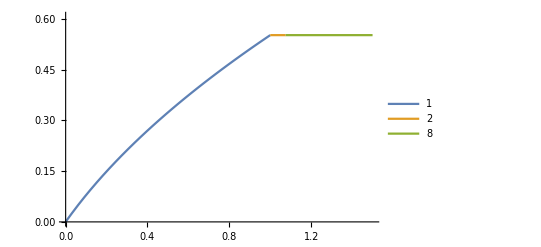

```mathematica
(*summary of all the limitation regimes encountered*)
lrlst=DeleteDuplicates[Flatten[R1lim[[All,2]]]]
ymax=1.1*Max[Flatten[R1lim[[All,3]]]];
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]];
Quiet[Show[Table[Plot[xin[[1]]=x;FindQSSselfc[limcombi[[lrlst[[kk]]]],system,xin],{x,0,1.5},PlotStyle->collr[[kk]],PlotRange->{All,{0,ymax}}(*,PlotPoints->200,MaxRecursion->5*),PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]]
```

### Growth along gradients in Glc and Pi (symmetrical, no inhibition)

```mathematica
iR1=1;
iR2=3;
AbsoluteTiming[R1lim=Table[xin[[iR1]]=SR1;xin[[iR2]]=SR2;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{SR1,SR2,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{SR1,Range[0.7,1.2,.01]},{SR2,Range[0.7,1.2,.01]}]]
```

```mathematica
lrlst=Sort[DeleteDuplicates[Flatten[Flatten[R1lim,1][[All,3]]]]]
(*ymax for scaling 3D plot z-axis*)
ymax=1.1*Max[Flatten[Flatten[R1lim,1][[All,4]]]];
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]]
```

{1,2,4,8,10,11}

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387]}

```mathematica
(*computing average coordinates for the point identified, to get a "representative" supply to look at the network*)
avcoord=Table[listi=Position[Flatten[R1lim,1][[All,3]],j][[1;;-1,1]];Mean[Flatten[R1lim,1][[listi]][[1;;-1,{1,2}]]],{j,lrlst}]

regimes=Table[{xin[[iR1]],xin[[iR2]]}=avcoord[[j]];
{avcoord[[j]],lrlst[[j]],Show[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{col1,thicc2},Automatic,{col2,thicc2},vtxsz2,imgsz2]],LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin]],system,col1,coordsub,vtxsz2,imgsz2],DisplayQSS[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin],system,xin]},{j,Length[lrlst]}]
```

{{0.815904,0.998614},{0.999483,0.815106},{0.9715,1.1505},{1.1505,0.9715},{1.125,1.125},{1.125,1.125}}

{{{0.815904,0.998614},1,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.474355 | q_1 | 0.115467
v_1 | 1 | 0.699368 | R_1 | 0.418689
v_2 | 2 | 0.855982 | R_2 | 0.
v_E | 4 | 2.66362 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
2 | q_1 | 0.474355 | 0.51316
4 | q_2 | 0.804517 | 0.
1 | R_1 | 0.815904 | NA
3 | R_2 | 0.998614 | NA
5 | N | 1. | 0.75658
7 | q_ATP | 1.33638 | 0.
6 | q_ADP | 2.66362 | 0.)}},{{0.999483,0.815106},2,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.474004 | q_2 | 0.115338
v_2 | 2 | 0.698684 | R_2 | 0.418431
v_1 | 1 | 0.856727 | R_1 | 0.
v_E | 4 | 2.66311 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
4 | q_2 | 0.474004 | 0.513345
2 | q_1 | 0.807424 | 0.
3 | R_2 | 0.815106 | NA
1 | R_1 | 0.999483 | NA
5 | N | 1. | 0.756672
7 | q_ATP | 1.33689 | 0.
6 | q_ADP | 2.66311 | 0.)}},{{0.9715,1.1505},4,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.540548 | q_1 | 0.140403
v_1 | 1 | 0.83274 | R_1 | 0.466821
v_2 | 2 | 0.939034 | q_ATP | 0.
v_E | 4 | 2.90449 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
2 | q_1 | 0.540548 | 0.480516
4 | q_2 | 0.737188 | 0.
1 | R_1 | 0.9715 | NA
5 | N | 1. | 0.740258
7 | q_ATP | 1.09551 | 0.
3 | R_2 | 1.1505 | NA
6 | q_ADP | 2.90449 | 0.)}},{{1.1505,0.9715},8,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.540548 | q_2 | 0.140403
v_2 | 2 | 0.83274 | R_2 | 0.466821
v_1 | 1 | 0.939034 | q_ATP | 0.
v_E | 4 | 2.90449 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
4 | q_2 | 0.540548 | 0.480516
2 | q_1 | 0.737188 | 0.
3 | R_2 | 0.9715 | NA
5 | N | 1. | 0.740258
7 | q_ATP | 1.09551 | 0.
1 | R_1 | 1.1505 | NA
6 | q_ADP | 2.90449 | 0.)}},{{1.125,1.125},10,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.570107 | q_1 | 0.121561
v_2 | 2 | 0.895128 | q_ATP | -0.101931
v_1 | 1 | 0.895128 | q_ATP | 0.288641
v_E | 4 | 2.95572 | q_ADP | 0.288503),(code | metabolite | concentration | reproductive value
4 | q_2 | 0.570107 | 0.
2 | q_1 | 0.570107 | 0.37401
5 | N | 1. | 0.
7 | q_ATP | 1.04428 | 0.268819
3 | R_2 | 1.125 | NA
1 | R_1 | 1.125 | NA
6 | q_ADP | 2.95572 | 0.171211)}},{{1.125,1.125},11,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.570107 | q_2 | 0.121561
v_2 | 2 | 0.895128 | q_ATP | 0.288641
v_1 | 1 | 0.895128 | q_ATP | -0.101931
v_E | 4 | 2.95572 | q_ADP | 0.288503),(code | metabolite | concentration | reproductive value
4 | q_2 | 0.570107 | 0.37401
2 | q_1 | 0.570107 | 0.
5 | N | 1. | 0.
7 | q_ATP | 1.04428 | 0.268819
3 | R_2 | 1.125 | NA
1 | R_1 | 1.125 | NA
6 | q_ADP | 2.95572 | 0.171211)}}}

```mathematica
fig3=GraphicsRow[regimes[[1,{3,4}]],ImageSize->800]
Export[StringJoin["figures/fig3.png"],fig3,"PNG",ImageResolution->resol];
Export[StringJoin["figures/fig3.pdf"],fig3,"PDF"];
```

-Graphics-

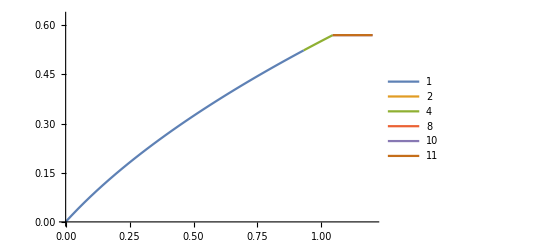

```mathematica
Show[Table[Plot[FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,iR1->x]],{x,0,1.2},PlotStyle->collr[[kk]],PlotRange->{All,{0,ymax}},PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]
```

```mathematica
AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotLegends->{lrlst[[kk]]},MaxRecursion->5,MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,Length[lrlst]}],ImageSize->700]]];
```

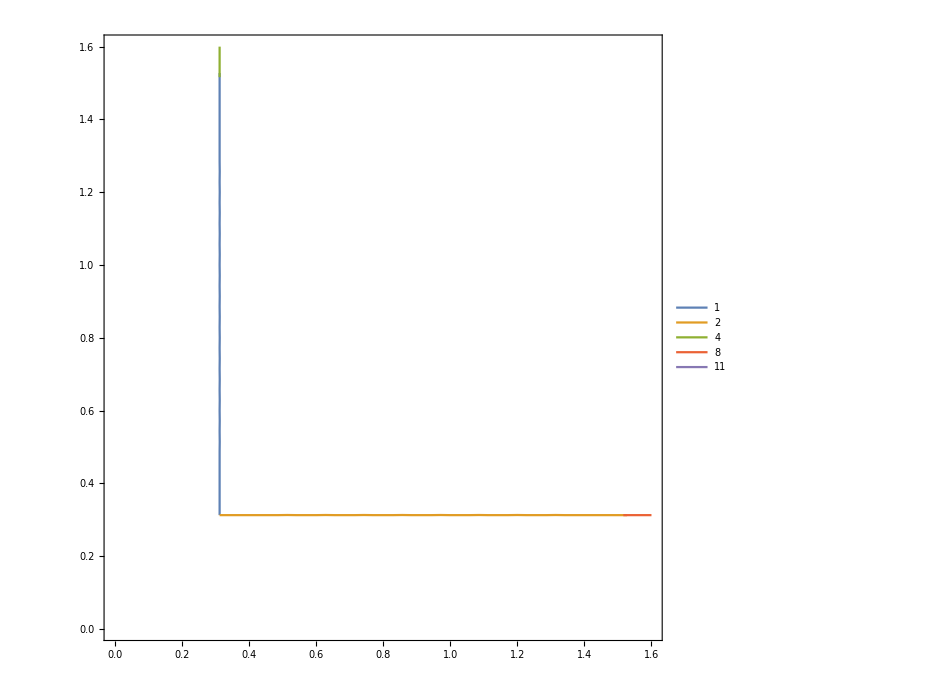

```mathematica
(*ZNGI*)
Quiet[Show[Table[ContourPlot[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]==.25,{x,0,1.6},{y,0,1.6},ContourStyle->collr[[kk]],PlotRange->{{0,1.6},{0,1.6}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}],ImageSize->700]]
```

```mathematica
avcoord2=Table[Mean[Nest[First,overview,Length[lrlst]][[1,i,1,1,1;;-1,{1,2}]]],{i,Length[lrlst]}]
```

{{0.478177,0.832869},{0.829586,0.497784},{0.791861,1.35125},{1.35752,0.78149},{1.24047,1.24047},{1.24047,1.24047}}

```mathematica
vtxsz3=vtxsz2*1.2;
imgsz3=300;
thicc3=Thickness[0.008];
lbl=Table[Show[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,ReplacePart[xin,{iR1->avcoord2[[j,1]],iR2->avcoord2[[j,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2]],{j,Length[lrlst]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Timing[overview=Quiet[Show[Table[Plot3D[Plotλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{1->x,3->y}]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}],ImageSize->700]]]*)
```

```mathematica
dL=.8;
dD=.6;
dL=.2;
dD=.2;
eqcl=GatherBy[Range[1,Length[lrlst]],GraphMetabNetLoop[limcombi[[lrlst[[#]]]],system,ReplacePart[xin,{iR1->avcoord2[[#,1]],iR2->avcoord2[[#,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2]&]
coleqcl=Delete[ColorData[97,"ColorList"],2][[Range[1,Length[eqcl]]]];
cols=Table[Table[dc=(dD+dL)/(Length[eqcl[[i]]]+1);If[j*dc<dL,Lighter[coleqcl[[i]],dL-j*dc],Darker[coleqcl[[i]],j*dc-dL]],{j,Length[eqcl[[i]]]}],{i,Length[eqcl]}]

(*lrlst=Table[lrlst[[j]],{j,Flatten[eqcl]}]*)
(*collr=Table[collr[[kk]],{kk,Length[lrlst]}];*)
lrlst
(*collr=Flatten[cols][[Flatten[eqcl]]]*)
collr=Flatten[cols][[Table[Position[Flatten[eqcl],i][[1,1]],{i,Length[lrlst]}]]]
```

{{1,3},{2,4},{5},{6}}

{{RGBColor[0.41052253333333333, 0.5396604, 0.7291448],RGBColor[0.3438558666666667, 0.47299373333333333, 0.6624781333333334]},{RGBColor[0.5895022666666667, 0.7121310666666667, 0.24855933333333335],RGBColor[0.5228356000000001, 0.6454644, 0.18189266666666667]},{RGBColor[0.922526, 0.385626, 0.209179]},{RGBColor[0.528488, 0.470624, 0.701351]}}

{1,2,4,8,10,11}

{RGBColor[0.41052253333333333, 0.5396604, 0.7291448],RGBColor[0.5895022666666667, 0.7121310666666667, 0.24855933333333335],RGBColor[0.3438558666666667, 0.47299373333333333, 0.6624781333333334],RGBColor[0.5228356000000001, 0.6454644, 0.18189266666666667],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351]}

```mathematica
Table[Position[eqcl,kk][[1,2]],{kk,Length[lrlst]}]
Table[Position[eqcl,kk][[1,1]],{kk,Length[lrlst]}]
Table[Length[eqcl[[Position[eqcl,kk][[1,1]]]]],{kk,Length[lrlst]}]
Table[collr[[kk]],{kk,Length[lrlst]}]
```

{1,1,2,2,1,1}

{1,2,1,2,3,4}

{2,2,2,2,1,1}

{RGBColor[0.41052253333333333, 0.5396604, 0.7291448],RGBColor[0.5895022666666667, 0.7121310666666667, 0.24855933333333335],RGBColor[0.3438558666666667, 0.47299373333333333, 0.6624781333333334],RGBColor[0.5228356000000001, 0.6454644, 0.18189266666666667],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351]}

```mathematica
(*here we manually draw the colimiting case (baseline code not good at handling colimitation)*)
GraphMetabNetLoopColim[limcb_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_,coord_,style1_,style2_,style3_,szvtx_,szim_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,Sacl,Sinhib,reprod,rvaleq,aclmeta,aclreac,inhreac,inhmeta,arwsz=szim*arwcf2,arwsz2=szim*arwcf},
aclreac={1,2,3,4};
aclmeta={2,4,6,7};
inhreac={};
inhmeta={};
Graph[verts[submeta,subreac],edges[S,subreac],
VertexLabels->vertlabels[submeta,subreac,metabo,reacnames],
PlotTheme->"IndexLabeled",
VertexStyle->vertstyle2[submeta,subreac,aclmeta,aclreac,inhmeta,inhreac,style1,style3],VertexSize->{"Scaled",szvtx},
EdgeStyle->Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i->If[(MemberQ[aclreac,i]&&MemberQ[aclmeta,j]&&j==limcb[[Position[subreac,i][[1,1]],2]])||(i==3&&j==2),{style1,Arrowheads[arwsz]},{style2,Arrowheads[arwsz2]}],{j,in}],Table[n+i->j->If[MemberQ[aclreac,i]&&MemberQ[aclmeta,j],{style1,Arrowheads[arwsz]},{style2,Arrowheads[arwsz2]}],{j,out}]}]
,{i,subreac}]],
VertexCoordinates->If[ToString[coord]=="Automatic",Automatic,Flatten[{Table[j->coord[[j]],{j,submeta}],Table[(n+i)->coord[[n+i]],{i,subreac}]}]],
VertexShapeFunction->Flatten[{Table[j->vf1,{j,submeta}],Table[(n+i)->Automatic,{i,subreac}]}],ImageSize->szim]]
```

```mathematica
lbl[[5]]=GraphMetabNetLoopColim[limcombi[[lrlst[[5]]]],system,ReplacePart[xin,{iR1->avcoord2[[5,1]],iR2->avcoord2[[5,2]]}],coordsub,{col1,thicc3},Automatic,{col1,thicc3},vtxsz2,imgsz2];
fulllbl=Table[Show[Graphics[{collr[[i]],Disk[{-2,0.5},.1]}],lbl[[i]]],{i,Length[lrlst]}]
Do[
fig=fulllbl[[i]];
Export[StringJoin["figures/figS3leg",ToString[i],".png"],fig,"PNG",ImageResolution->resol];
,{i,Length[lbl]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotLegends->{If[Position[eqcl,kk][[1,2]]==Length[eqcl[[Position[eqcl,kk][[1,1]]]]],lbl[[kk]],None]},MaxRecursion->5,MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,Length[lrlst]}],ImageSize->700]]]*)
```

```mathematica
AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},MaxRecursion->5,MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,Length[lrlst]}],ImageSize->700]]]
```

{64.7751,-Graphics3D-}

```mathematica
toy1=Show[overview,ViewPoint->{-1,-2,1},ViewAngle->35°]
Export[StringJoin["figures/fig4.png"],toy1,"PNG",ImageResolution->resol];
Export[StringJoin["figures/fig4.pdf"],toy1,"PDF"];
```

-Graphics3D-

### Growth along gradients in Glc and Pi (symmetrical, INHIBITION)

#### Setup

```mathematica
(*cordstyle=GraphEmbedding[graph]*)
(*coordsub={{2,-1},{1,1},{-2,-1},{-1,1},{0,2},{-.5,.5},{.5,-.5},{1,0},{-1,0},{0,1},{0,-1}}*)
GraphMetabNet[system,coordsub,vtxsz,imgsz]

(*make accumulation when ATP limited faster than growth*)
α=SparseArray[Table[k->1,{k,input}]];
α[[7,1]]=2.1;
α[[7,2]]=2.1;

(*α[[7,1]]=1;
α[[7,2]]=1;*)

μ=Table[1,{k,p}];
(*LESS ENERGY: ATP FORMATION BY ADP SLOWED DOWN*)
μ[[4]]=.5;

xin=Table[0,{i,n}];
Do[xin[[i]]=1.,{i,essent}];
xin[[1]]=.9;
system={S,metabo,reacnames,submeta,subreac,α,μ};
```

-Graphics-

#### Both R1 and R2 gradients

```mathematica
Timing[R1lim=Table[xin[[iR1]]=SR1;xin[[iR2]]=SR2;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{SR1,SR2,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{SR1,Range[0.1,1.2,.05]},{SR2,Range[0.1,1.2,.05]}]];
```

```mathematica
lrlst=Sort[DeleteDuplicates[Flatten[Flatten[R1lim,1][[All,3]]]]]
ymax=1.1*Max[Flatten[Flatten[R1lim,1][[All,4]]]]
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]]
```

{1,2,3,4,6,8,9,12}

0.458988

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0]}

```mathematica
(*computing average coordinates for the point identified, to get a "representative" supply to look at the network*)
avcoord=Table[listi=Position[Flatten[R1lim,1][[All,3]],j][[1;;-1,1]];Mean[Flatten[R1lim,1][[listi]][[1;;-1,{1,2}]]],{j,lrlst}]

Table[{xin[[iR1]],xin[[iR2]]}=avcoord[[j]];
{avcoord[[j]],lrlst[[j]],Show[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{col1,thicc2},Automatic,{col2,thicc2},vtxsz2,imgsz2]],LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin]],system,col1,coordsub,vtxsz2,imgsz2],DisplayQSS[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin],system,xin]},{j,Length[lrlst]}]
```

{{0.257801,0.681206},{0.674828,0.263103},{0.645,0.645},{0.417241,1.07414},{0.601724,0.982759},{1.07414,0.417241},{0.982759,0.601724},{0.95,0.95}}

{{{0.257801,0.681206},1,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.212602 | q_1 | 0.0317145
v_1 | 1 | 0.257801 | R_1 | 0.180887
v_2 | 2 | 0.681206 | R_2 | 0.
v_E | 4 | 1.40472 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
2 | q_1 | 0.212602 | 0.701654
1 | R_1 | 0.257801 | NA
3 | R_2 | 0.681206 | NA
5 | N | 1. | 0.850827
7 | q_ATP | 1.19055 | 0.
4 | q_2 | 2.20414 | 0.
6 | q_ADP | 2.80945 | 0.)}},{{0.674828,0.263103},2,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.216312 | q_2 | 0.0326611
v_2 | 2 | 0.263103 | R_2 | 0.183651
v_1 | 1 | 0.674828 | R_1 | 0.
v_E | 4 | 1.40965 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
4 | q_2 | 0.216312 | 0.698019
3 | R_2 | 0.263103 | NA
1 | R_1 | 0.674828 | NA
5 | N | 1. | 0.84901
7 | q_ATP | 1.18071 | 0.
2 | q_1 | 2.11969 | 0.
6 | q_ADP | 2.81929 | 0.)}},{{0.645,0.645},3,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.378051 | q_ATP | 0.147134
v_2 | 2 | 0.645 | R_2 | -0.285891
v_1 | 1 | 0.645 | R_1 | -0.285891
v_E | 4 | 1.81097 | q_ADP | 1.6054),(code | metabolite | concentration | reproductive value
7 | q_ATP | 0.378051 | 1.02946
3 | R_2 | 0.645 | NA
1 | R_1 | 0.645 | NA
4 | q_2 | 0.706117 | 0.
2 | q_1 | 0.706117 | 0.
5 | N | 1. | -1.51245
6 | q_ADP | 3.62195 | 0.586219)}},{{0.417241,1.07414},4,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.316848 | q_1 | 0.0614514
v_1 | 1 | 0.417241 | R_1 | 0.255397
v_2 | 2 | 0.911399 | q_ATP | 0.
v_E | 4 | 1.783 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
2 | q_1 | 0.316848 | 0.612109
1 | R_1 | 0.417241 | NA
7 | q_ATP | 0.433999 | 0.
5 | N | 1. | 0.806054
3 | R_2 | 1.07414 | NA
4 | q_2 | 1.87645 | 0.
6 | q_ADP | 3.566 | 0.)}},{{0.601724,0.982759},6,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.353666 | q_ATP | 0.242519
v_1 | 1 | 0.601724 | R_1 | -0.139698
v_2 | 2 | 0.742698 | q_ATP | -0.172426
v_E | 4 | 1.82317 | q_ADP | 0.846541),(code | metabolite | concentration | reproductive value
7 | q_ATP | 0.353666 | 0.560385
1 | R_1 | 0.601724 | NA
2 | q_1 | 0.701393 | 0.
3 | R_2 | 0.982759 | NA
5 | N | 1. | -0.394999
4 | q_2 | 1.1 | 0.
6 | q_ADP | 3.64633 | 0.328223)}},{{1.07414,0.417241},8,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.316848 | q_2 | 0.0614514
v_2 | 2 | 0.417241 | R_2 | 0.255397
v_1 | 1 | 0.911399 | q_ATP | 0.
v_E | 4 | 1.783 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
4 | q_2 | 0.316848 | 0.612109
3 | R_2 | 0.417241 | NA
7 | q_ATP | 0.433999 | 0.
5 | N | 1. | 0.806054
1 | R_1 | 1.07414 | NA
2 | q_1 | 1.87645 | 0.
6 | q_ADP | 3.566 | 0.)}},{{0.982759,0.601724},9,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.353666 | q_ATP | 0.242519
v_2 | 2 | 0.601724 | R_2 | -0.139698
v_1 | 1 | 0.742698 | q_ATP | -0.172426
v_E | 4 | 1.82317 | q_ADP | 0.846541),(code | metabolite | concentration | reproductive value
7 | q_ATP | 0.353666 | 0.560385
3 | R_2 | 0.601724 | NA
4 | q_2 | 0.701393 | 0.
1 | R_1 | 0.982759 | NA
5 | N | 1. | -0.394999
2 | q_1 | 1.1 | 0.
6 | q_ADP | 3.64633 | 0.328223)}},{{0.95,0.95},12,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.331588 | q_ATP | 0.262198
v_2 | 2 | 0.696334 | q_ATP | -0.109432
v_1 | 1 | 0.696334 | q_ATP | -0.109432
v_E | 4 | 1.83421 | q_ADP | 0.576507),(code | metabolite | concentration | reproductive value
7 | q_ATP | 0.331588 | 0.394127
3 | R_2 | 0.95 | NA
1 | R_1 | 0.95 | NA
5 | N | 1. | 0.
4 | q_2 | 1.1 | 0.
2 | q_1 | 1.1 | 0.
6 | q_ADP | 3.66841 | 0.236972)}}}

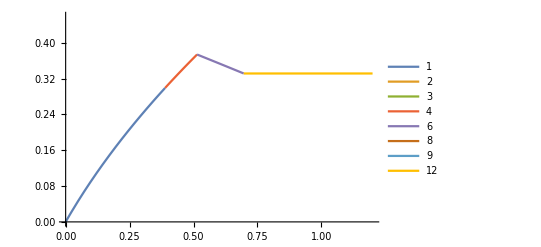

```mathematica
Show[Table[Plot[FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,iR1->x]],{x,0,1.2},PlotStyle->collr[[kk]],PlotRange->{All,{0,ymax}},PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]
```

```mathematica
AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{1->x,3->y}]]],Lighting->{{"Ambient",White}},MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]},PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}],ImageSize->700]]];
```

```mathematica
avcoord2=Table[Mean[Nest[First,overview,Length[lrlst]][[1,i,1,1,1;;-1,{1,2}]]],{i,Length[lrlst]}]
```

{{0.223757,0.751169},{0.743206,0.222873},{0.652207,0.641456},{0.323526,1.27809},{0.629066,1.12745},{1.29502,0.315592},{1.13615,0.628733},{1.01648,1.03301}}

```mathematica
vtxsz3=vtxsz2*1.2;
imgsz3=300;
thicc3=Thickness[0.008];
lbl=Table[Show[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,ReplacePart[xin,{iR1->avcoord2[[j,1]],iR2->avcoord2[[j,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2]],{j,Length[lrlst]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
eqcl=GatherBy[Range[1,Length[lrlst]],GraphMetabNetLoop[limcombi[[lrlst[[#]]]],system,ReplacePart[xin,{iR1->avcoord2[[#,1]],iR2->avcoord2[[#,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2]&]
coleqcl=Delete[ColorData[97,"ColorList"],2][[Range[1,Length[eqcl]]]];
cols=Table[Table[dc=(dD+dL)/(Length[eqcl[[i]]]+1);If[j*dc<dL,Lighter[coleqcl[[i]],dL-j*dc],Darker[coleqcl[[i]],j*dc-dL]],{j,Length[eqcl[[i]]]}],{i,Length[eqcl]}]

(*lrlst=Table[lrlst[[j]],{j,Flatten[eqcl]}]*)
(*collr=Table[collr[[kk]],{kk,Length[lrlst]}];*)
lrlst
(*collr=Flatten[cols][[Flatten[eqcl]]]*)
collr=Flatten[cols][[Table[Position[Flatten[eqcl],i][[1,1]],{i,Length[lrlst]}]]]
```

{{1,4},{2,6},{3},{5},{7},{8}}

{{RGBColor[0.41052253333333333, 0.5396604, 0.7291448],RGBColor[0.3438558666666667, 0.47299373333333333, 0.6624781333333334]},{RGBColor[0.5895022666666667, 0.7121310666666667, 0.24855933333333335],RGBColor[0.5228356000000001, 0.6454644, 0.18189266666666667]},{RGBColor[0.922526, 0.385626, 0.209179]},{RGBColor[0.528488, 0.470624, 0.701351]},{RGBColor[0.772079, 0.431554, 0.102387]},{RGBColor[0.363898, 0.618501, 0.782349]}}

{1,2,3,4,6,8,9,12}

{RGBColor[0.41052253333333333, 0.5396604, 0.7291448],RGBColor[0.5895022666666667, 0.7121310666666667, 0.24855933333333335],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.3438558666666667, 0.47299373333333333, 0.6624781333333334],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.5228356000000001, 0.6454644, 0.18189266666666667],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349]}

```mathematica
Do[
fig=Show[Graphics[{collr[[i]],Disk[{-2,.5},.1]}],lbl[[i]]];
Export[StringJoin["figures/fig4bleg",ToString[i],".png"],fig,"PNG",ImageResolution->resol];
,{i,Length[lbl]}]
```

```mathematica
AbsoluteTiming[overview0=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},MaxRecursion->5,MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,Length[lrlst]}],ImageSize->700]]]
Export[StringJoin["figures/fig4b0.png"],overview0,"PNG",ImageResolution->resol];
Export[StringJoin["figures/fig4b0.pdf"],overview0,"PDF"];
```

{327.192,-Graphics3D-}

```mathematica
(*AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotLegends->{If[Position[eqcl,kk][[1,2]]==Length[eqcl[[Position[eqcl,kk][[1,1]]]]],lbl[[kk]],None]},MaxRecursion->5,MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,Length[lrlst]}],ImageSize->700]]]*)
overview=Show[overview0,Show[Table[Plot3D[Undefined,{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotLegends->{If[Position[eqcl,kk][[1,2]]==Length[eqcl[[Position[eqcl,kk][[1,1]]]]],lbl[[kk]],None]},MaxRecursion->5,MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,Length[lrlst]}]]]
```

{402.372,-Graphics3D-}

```mathematica
toy2=Show[overview,ViewPoint->{-1,-2,1},ViewAngle->35°]
Export[StringJoin["figures/fig4b.png"],toy2,"PNG",ImageResolution->resol];
Export[StringJoin["figures/fig4b.pdf"],toy2,"PDF"];
```

-Graphics3D-

```mathematica
ymax2=.75;
AbsoluteTiming[overview0=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax2}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},MaxRecursion->5,MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax2,ymax2/20}]}],{kk,Length[lrlst]}],ImageSize->700]]]
Export[StringJoin["figures/figS2b.png"],overview0,"PNG",ImageResolution->resol];
Export[StringJoin["figures/figS2b.pdf"],overview0,"PDF"];
```

{448.743,-Graphics3D-}

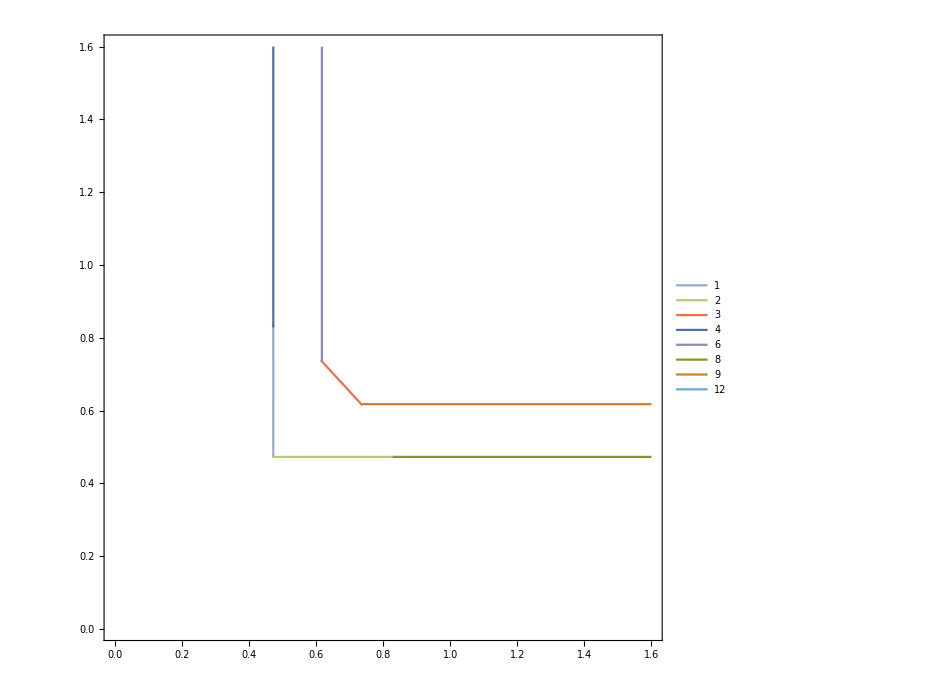

```mathematica
(*Quiet[Show[Table[ContourPlot[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]==.35,{x,0,1.6},{y,0,1.6},ContourStyle->collr[[kk]],PlotRange->{{0,1.6},{0,1.6}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}],ImageSize->700]]*)
```

```mathematica
Table[
overview=Quiet[Show[Table[Plot3D[GetQSSstate[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]][[jj]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},MaxRecursion->5,MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,Length[lrlst]}],ImageSize->700]],{jj,4}]
```

$Aborted

### Growth along gradients in Glc and Pi (symmetrical, EVEN LESS ENERGY)

#### Setup

```mathematica
(*cordstyle=GraphEmbedding[graph]*)
(*coordsub={{2,-1},{1,1},{-2,-1},{-1,1},{0,2},{-.5,.5},{.5,-.5},{1,0},{-1,0},{0,1},{0,-1}}*)
GraphMetabNet[system,coordsub,vtxsz,imgsz]

(*make accumulation when ATP limited faster than growth*)
α=SparseArray[Table[k->1,{k,input}]];
α[[7,1]]=2.1;
α[[7,2]]=2.1;

(*α[[7,1]]=1;
α[[7,2]]=1;*)

μ=Table[1,{k,p}];
(*LESS ENERGY: ATP FORMATION BY ADP SLOWED DOWN*)
μ[[4]]=.2;

xin=Table[0,{i,n}];
Do[xin[[i]]=1.,{i,essent}];
xin[[1]]=.9;
system={S,metabo,reacnames,submeta,subreac,α,μ};
```

-Graphics-

#### Both R1 and R2 gradients

```mathematica
Timing[R1lim=Table[xin[[iR1]]=SR1;xin[[iR2]]=SR2;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{SR1,SR2,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{SR1,Range[0.1,1.2,.05]},{SR2,Range[0.1,1.2,.05]}]];
```

```mathematica
lrlst=Sort[DeleteDuplicates[Flatten[Flatten[R1lim,1][[All,3]]]]]
ymax=1.1*Max[Flatten[Flatten[R1lim,1][[All,4]]]]
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]]
```

{1,2,3,4,6,8,9,12}

0.199127

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0]}

```mathematica
(*computing average coordinates for the point identified, to get a "representative" supply to look at the network*)
avcoord=Table[listi=Position[Flatten[R1lim,1][[All,3]],j][[1;;-1,1]];Mean[Flatten[R1lim,1][[listi]][[1;;-1,{1,2}]]],{j,lrlst}]

Table[{xin[[iR1]],xin[[iR2]]}=avcoord[[j]];
{avcoord[[j]],lrlst[[j]],Show[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{col1,thicc2},Automatic,{col2,thicc2},vtxsz2,imgsz2]],LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin]],system,col1,coordsub,vtxsz2,imgsz2],DisplayQSS[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin],system,xin]},{j,Length[lrlst]}]
```

{{0.138889,0.297222},{0.3,0.132353},{0.4,0.2375},{0.153191,0.830851},{0.275,0.775},{0.830851,0.153191},{0.775,0.275},{0.775,0.775}}

{{{0.138889,0.297222},1,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.12361 | q_1 | 0.0122507
v_1 | 1 | 0.138889 | R_1 | 0.111359
v_2 | 2 | 0.297222 | R_2 | 0.
v_E | 4 | 0.6515 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
2 | q_1 | 0.12361 | 0.801784
1 | R_1 | 0.138889 | 0.125124
3 | R_2 | 0.297222 | 0.267765
7 | q_ATP | 0.742498 | 0.
5 | B | 1. | 0.900892
4 | q_2 | 1.40452 | 0.
6 | q_ADP | 3.2575 | 0.)}},{{0.3,0.132353},2,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.118347 | q_2 | 0.0113254
v_2 | 2 | 0.132353 | R_2 | 0.107022
v_1 | 1 | 0.3 | R_1 | 0.
v_E | 4 | 0.643378 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
4 | q_2 | 0.118347 | 0.808608
3 | R_2 | 0.132353 | 0.119687
1 | R_1 | 0.3 | 0.271291
7 | q_ATP | 0.783108 | 0.
5 | B | 1. | 0.904304
2 | q_1 | 1.53492 | 0.
6 | q_ADP | 3.21689 | 0.)}},{{0.4,0.2375},3,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.122842 | q_ATP | 0.0274323
v_2 | 2 | 0.2375 | R_2 | -0.164282
v_1 | 1 | 0.4 | q_ATP | -0.276686
v_E | 4 | 0.775432 | q_ADP | 2.68189),(code | metabolite | concentration | reproductive value
7 | q_ATP | 0.122842 | 1.8179
3 | R_2 | 0.2375 | -0.85256
1 | R_1 | 0.4 | -1.43589
4 | q_2 | 0.933384 | 0.
5 | B | 1. | -3.58973
2 | q_1 | 2.25623 | 0.
6 | q_ADP | 3.87716 | 1.12619)}},{{0.153191,0.830851},4,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.134974 | q_1 | 0.0143454
v_1 | 1 | 0.153191 | R_1 | 0.120628
v_2 | 2 | 0.441423 | q_ATP | 0.
v_E | 4 | 0.75796 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
2 | q_1 | 0.134974 | 0.787434
1 | R_1 | 0.153191 | 0.13691
7 | q_ATP | 0.210201 | 0.
3 | R_2 | 0.830851 | 0.742546
5 | B | 1. | 0.893717
4 | q_2 | 2.27044 | 0.
6 | q_ADP | 3.7898 | 0.)}},{{0.275,0.775},6,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.152082 | q_ATP | 0.103469
v_1 | 1 | 0.275 | R_1 | -0.0763006
v_2 | 2 | 0.319372 | q_ATP | -0.0886121
v_E | 4 | 0.769584 | q_ADP | 1.06763),(code | metabolite | concentration | reproductive value
7 | q_ATP | 0.152082 | 0.642334
1 | R_1 | 0.275 | -0.137969
3 | R_2 | 0.775 | -0.388823
2 | q_1 | 0.808233 | 0.
5 | B | 1. | -0.501707
4 | q_2 | 1.1 | 0.
6 | q_ADP | 3.84792 | 0.364878)}},{{0.830851,0.153191},8,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.134974 | q_2 | 0.0143454
v_2 | 2 | 0.153191 | R_2 | 0.120628
v_1 | 1 | 0.441423 | q_ATP | 0.
v_E | 4 | 0.75796 | q_ADP | 0.),(code | metabolite | concentration | reproductive value
4 | q_2 | 0.134974 | 0.787434
3 | R_2 | 0.153191 | 0.13691
7 | q_ATP | 0.210201 | 0.
1 | R_1 | 0.830851 | 0.742546
5 | B | 1. | 0.893717
2 | q_1 | 2.27044 | 0.
6 | q_ADP | 3.7898 | 0.)}},{{0.775,0.275},9,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.152082 | q_ATP | 0.103469
v_2 | 2 | 0.275 | R_2 | -0.0763006
v_1 | 1 | 0.319372 | q_ATP | -0.0886121
v_E | 4 | 0.769584 | q_ADP | 1.06763),(code | metabolite | concentration | reproductive value
7 | q_ATP | 0.152082 | 0.642334
3 | R_2 | 0.275 | -0.137969
1 | R_1 | 0.775 | -0.388823
4 | q_2 | 0.808233 | 0.
5 | B | 1. | -0.501707
2 | q_1 | 1.1 | 0.
6 | q_ADP | 3.84792 | 0.364878)}},{{0.775,0.775},12,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
μ | 3 | 0.144293 | q_ATP | 0.115267
v_2 | 2 | 0.303014 | q_ATP | -0.0532671
v_1 | 1 | 0.303014 | q_ATP | -0.0532671
v_E | 4 | 0.771141 | q_ADP | 0.677797),(code | metabolite | concentration | reproductive value
7 | q_ATP | 0.144293 | 0.419449
3 | R_2 | 0.775 | 0.
1 | R_1 | 0.775 | 0.
5 | B | 1. | 0.
2 | q_1 | 1.1 | 0.
4 | q_2 | 1.1 | 0.
6 | q_ADP | 3.85571 | 0.243659)}}}

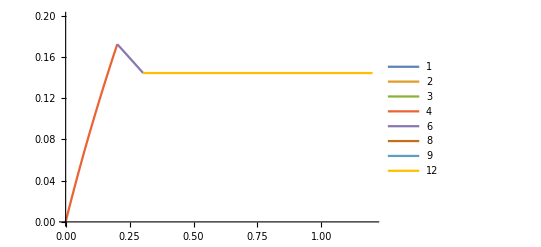

```mathematica
Show[Table[Plot[FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,iR1->x]],{x,0,1.2},PlotStyle->collr[[kk]],PlotRange->{All,{0,ymax}},PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]
```

```mathematica
AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{1->x,3->y}]]],Lighting->{{"Ambient",White}},MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]},PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}],ImageSize->700]]];
```

```mathematica
avcoord2=Table[Mean[Nest[First,overview,Length[lrlst]][[1,i,1,1,1;;-1,{1,2}]]],{i,Length[lrlst]}]
```

{{0.0965443,0.336538},{0.340181,0.0942421},{0.280692,0.277133},{0.121806,1.02018},{0.252939,0.963598},{1.01841,0.121609},{0.977271,0.251932},{0.779129,0.759436}}

```mathematica
vtxsz3=vtxsz2*1.2;
imgsz3=300;
thicc3=Thickness[0.008];
lbl=Table[Show[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,ReplacePart[xin,{iR1->avcoord2[[j,1]],iR2->avcoord2[[j,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2]],{j,Length[lrlst]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
eqcl=GatherBy[Range[1,Length[lrlst]],GraphMetabNetLoop[limcombi[[lrlst[[#]]]],system,ReplacePart[xin,{iR1->avcoord2[[#,1]],iR2->avcoord2[[#,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2]&]
coleqcl=Delete[ColorData[97,"ColorList"],2][[Range[1,Length[eqcl]]]];
cols=Table[Table[dc=(dD+dL)/(Length[eqcl[[i]]]+1);If[j*dc<dL,Lighter[coleqcl[[i]],dL-j*dc],Darker[coleqcl[[i]],j*dc-dL]],{j,Length[eqcl[[i]]]}],{i,Length[eqcl]}]

(*lrlst=Table[lrlst[[j]],{j,Flatten[eqcl]}]*)
(*collr=Table[collr[[kk]],{kk,Length[lrlst]}];*)
lrlst
(*collr=Flatten[cols][[Flatten[eqcl]]]*)
collr=Flatten[cols][[Table[Position[Flatten[eqcl],i][[1,1]],{i,Length[lrlst]}]]]
```

{{1,4},{2,6},{3},{5},{7},{8}}

{{RGBColor[0.41052253333333333, 0.5396604, 0.7291448],RGBColor[0.3438558666666667, 0.47299373333333333, 0.6624781333333334]},{RGBColor[0.5895022666666667, 0.7121310666666667, 0.24855933333333335],RGBColor[0.5228356000000001, 0.6454644, 0.18189266666666667]},{RGBColor[0.922526, 0.385626, 0.209179]},{RGBColor[0.528488, 0.470624, 0.701351]},{RGBColor[0.772079, 0.431554, 0.102387]},{RGBColor[0.363898, 0.618501, 0.782349]}}

{1,2,3,4,6,8,9,12}

{RGBColor[0.41052253333333333, 0.5396604, 0.7291448],RGBColor[0.5895022666666667, 0.7121310666666667, 0.24855933333333335],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.3438558666666667, 0.47299373333333333, 0.6624781333333334],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.5228356000000001, 0.6454644, 0.18189266666666667],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349]}

```mathematica
Do[
fig=Show[Graphics[{collr[[i]],Disk[{-2,1},.1]}],lbl[[i]]];
Export[StringJoin["figures/fig4cleg",ToString[i],".png"],fig,"PNG",ImageResolution->resol];
,{i,Length[lbl]}]
```

```mathematica
AbsoluteTiming[overview0=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax2}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},MaxRecursion->5,MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax2,ymax2/20}]}],{kk,Length[lrlst]}],ImageSize->700]]]
Export[StringJoin["figures/figS2a.png"],overview0,"PNG",ImageResolution->resol];
Export[StringJoin["figures/figS2a.pdf"],overview0,"PDF"];
```

{1015.16,-Graphics3D-}

### MORE ENERGY: Growth along gradients in Glc and Pi (symmetrical)

#### Setup

```mathematica
(*cordstyle=GraphEmbedding[graph]*)
(*coordsub={{2,-1},{1,1},{-2,-1},{-1,1},{0,2},{-.5,.5},{.5,-.5},{1,0},{-1,0},{0,1},{0,-1}}*)
GraphMetabNet[system,coordsub,vtxsz,imgsz]

(*make accumulation when ATP limited faster than growth*)
α=SparseArray[Table[k->1,{k,input}]];
α[[7,1]]=2.1;
α[[7,2]]=2.1;

(*α[[7,1]]=1;
α[[7,2]]=1;*)

μ=Table[1,{k,p}];
(*LESS ENERGY: ATP FORMATION BY ADP SLOWED DOWN*)
μ[[4]]=1;

xin=Table[0,{i,n}];
Do[xin[[i]]=1.,{i,essent}];
xin[[1]]=.9;
system={S,metabo,reacnames,submeta,subreac,α,μ};
```

-Graphics-

#### Both R1 and R2 gradients

```mathematica
Timing[R1lim=Table[xin[[iR1]]=SR1;xin[[iR2]]=SR2;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{SR1,SR2,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{SR1,Range[0.1,1.6,.05]},{SR2,Range[0.1,1.6,.05]}]];
```

```mathematica
lrlst=Sort[DeleteDuplicates[Flatten[Flatten[R1lim,1][[All,3]]]]]
ymax=1.1*Max[Flatten[Flatten[R1lim,1][[All,4]]]]
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]]
```

{1,2,3,4,6,8,9,12}

0.728085

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0]}

```mathematica
(*computing average coordinates for the point identified, to get a "representative" supply to look at the network*)
avcoord=Table[listi=Position[Flatten[R1lim,1][[All,3]],j][[1;;-1,1]];Mean[Flatten[R1lim,1][[listi]][[1;;-1,{1,2}]]],{j,lrlst}]

Table[{xin[[iR1]],xin[[iR2]]}=avcoord[[j]];
{avcoord[[j]],lrlst[[j]],Show[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{col1,thicc2},Automatic,{col2,thicc2},vtxsz2,imgsz2]],LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin]],system,col1,coordsub,vtxsz2,imgsz2],DisplayQSS[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin],system,xin]},{j,Length[lrlst]}]
```

{{0.466203,1.02937},{1.03689,0.465039},{1.175,1.175},{0.925,1.5125},{1.12778,1.45556},{1.5125,0.925},{1.45556,1.12778},{1.425,1.425}}

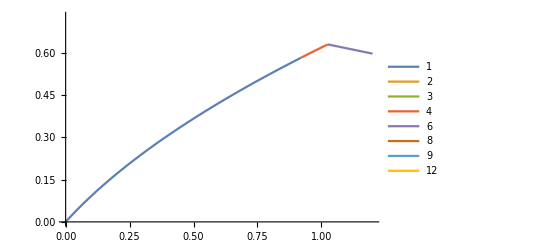

```mathematica
Show[Table[Plot[FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,iR1->x]],{x,0,1.2},PlotStyle->collr[[kk]],PlotRange->{All,{0,ymax}},PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]
```

```mathematica
AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{1->x,3->y}]]],Lighting->{{"Ambient",White}},MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]},PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}],ImageSize->700]]];
```

```mathematica
avcoord2=Table[Mean[Nest[First,overview,Length[lrlst]][[1,i,1,1,1;;-1,{1,2}]]],{i,Length[lrlst]}]
```

{{0.445805,0.921496},{0.905284,0.44861},{1.16909,1.17193},{0.915853,1.50816},{1.13949,1.40812},{1.50777,0.91696},{1.41821,1.14489},{1.38017,1.3746}}

```mathematica
vtxsz3=vtxsz2*1.2;
imgsz3=300;
thicc3=Thickness[0.008];
lbl=Table[Show[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,ReplacePart[xin,{iR1->avcoord2[[j,1]],iR2->avcoord2[[j,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2]],{j,Length[lrlst]}]
```

```mathematica
eqcl=GatherBy[Range[1,Length[lrlst]],GraphMetabNetLoop[limcombi[[lrlst[[#]]]],system,ReplacePart[xin,{iR1->avcoord2[[#,1]],iR2->avcoord2[[#,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2]&]
coleqcl=Delete[ColorData[97,"ColorList"],2][[Range[1,Length[eqcl]]]];
cols=Table[Table[dc=(dD+dL)/(Length[eqcl[[i]]]+1);If[j*dc<dL,Lighter[coleqcl[[i]],dL-j*dc],Darker[coleqcl[[i]],j*dc-dL]],{j,Length[eqcl[[i]]]}],{i,Length[eqcl]}]

(*lrlst=Table[lrlst[[j]],{j,Flatten[eqcl]}]*)
(*collr=Table[collr[[kk]],{kk,Length[lrlst]}];*)
lrlst
(*collr=Flatten[cols][[Flatten[eqcl]]]*)
collr=Flatten[cols][[Table[Position[Flatten[eqcl],i][[1,1]],{i,Length[lrlst]}]]]
```

{{1,4},{2,6},{3},{5},{7},{8}}

{{RGBColor[0.41052253333333333, 0.5396604, 0.7291448],RGBColor[0.3438558666666667, 0.47299373333333333, 0.6624781333333334]},{RGBColor[0.5895022666666667, 0.7121310666666667, 0.24855933333333335],RGBColor[0.5228356000000001, 0.6454644, 0.18189266666666667]},{RGBColor[0.922526, 0.385626, 0.209179]},{RGBColor[0.528488, 0.470624, 0.701351]},{RGBColor[0.772079, 0.431554, 0.102387]},{RGBColor[0.363898, 0.618501, 0.782349]}}

{1,2,3,4,6,8,9,12}

{RGBColor[0.41052253333333333, 0.5396604, 0.7291448],RGBColor[0.5895022666666667, 0.7121310666666667, 0.24855933333333335],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.3438558666666667, 0.47299373333333333, 0.6624781333333334],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.5228356000000001, 0.6454644, 0.18189266666666667],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349]}

```mathematica
Do[
fig=Show[Graphics[{collr[[i]],Disk[{-2,1},.1]}],lbl[[i]]];
Export[StringJoin["figures/fig4dleg",ToString[i],".png"],fig,"PNG",ImageResolution->resol];
,{i,Length[lbl]}]
```

```mathematica
AbsoluteTiming[overview0=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax2}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},MaxRecursion->5,MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax2,ymax2/20}]}],{kk,Length[lrlst]}],ImageSize->700]]]
Export[StringJoin["figures/figS2c.png"],overview0,"PNG",ImageResolution->resol];
Export[StringJoin["figures/figS2c.pdf"],overview0,"PDF"];
```

{69.5389,-Graphics3D-}

### Growth along gradients in Glc and Pi (asymmetrical, random)

#### Setup

```mathematica
(*cordstyle=GraphEmbedding[graph]*)
(*coordsub={{2,-1},{1,1},{-2,-1},{-1,1},{0,2},{-.5,.5},{.5,-.5},{1,0},{-1,0},{0,1},{0,-1}}*)
GraphMetabNet[system,coordsub,vtxsz,imgsz]

SeedRandom[1]
α=SparseArray[Table[k->1+.3*RandomReal[{-1,1}],{k,input}]];

(*α[[7,1]]=1;
α[[7,2]]=1;*)

μ=Table[1,{k,p}];
(*LESS ENERGY: ATP FORMATION BY ADP SLOWED DOWN*)
μ[[4]]=.5;

xin=Table[0,{i,n}];
Do[xin[[i]]=1.,{i,essent}];
xin[[1]]=.9;
system={S,metabo,reacnames,submeta,subreac,α,μ};
```

-Graphics-

#### Both R1 and R2 gradients

```mathematica
Timing[R1lim=Table[xin[[iR1]]=SR1;xin[[iR2]]=SR2;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{SR1,SR2,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{SR1,Range[0.1,1.2,.05]},{SR2,Range[0.1,1.2,.05]}]];
```

```mathematica
lrlst=Sort[DeleteDuplicates[Flatten[Flatten[R1lim,1][[All,3]]]]]
ymax=1.1*Max[Flatten[Flatten[R1lim,1][[All,4]]]]
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]]
```

{1,2,4,7,8,10}

0.35018

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387]}

```mathematica
(*computing average coordinates for the point identified, to get a "representative" supply to look at the network*)
avcoord=Table[listi=Position[Flatten[R1lim,1][[All,3]],j][[1;;-1,1]];Mean[Flatten[R1lim,1][[listi]][[1;;-1,{1,2}]]],{j,lrlst}]

Table[{xin[[iR1]],xin[[iR2]]}=avcoord[[j]];
{avcoord[[j]],lrlst[[j]],Show[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{col1,thicc2},Automatic,{col2,thicc2},vtxsz2,imgsz2]],LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin]],system,col1,coordsub,vtxsz2,imgsz2],DisplayQSS[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin],system,xin]},{j,Length[lrlst]}]
```

{{0.186735,0.44898},{0.385366,0.17439},{0.212727,0.940909},{0.8,0.425},{0.884375,0.2375},{0.775,0.85}}

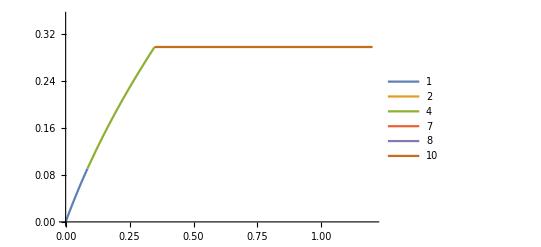

```mathematica
Show[Table[Plot[FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,iR1->x]],{x,0,1.2},PlotStyle->collr[[kk]],PlotRange->{All,{0,ymax}},PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]
```

```mathematica
AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{1->x,3->y}]]],Lighting->{{"Ambient",White}},MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]},PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}],ImageSize->700]]]
```

{26.5494,-Graphics3D-}

```mathematica
avcoord2=Table[Mean[Nest[First,overview,Length[lrlst]][[1,i,1,1,1;;-1,{1,2}]]],{i,Length[lrlst]}]
```

{{0.143003,0.475614},{0.438719,0.128667},{0.20903,1.07255},{0.972054,0.424187},{1.02056,0.233445},{0.81742,0.946166}}

```mathematica
vtxsz3=vtxsz2*1.2;
imgsz3=300;
thicc3=Thickness[0.008];
lbl=Table[Show[GraphMetabNetLim[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,ReplacePart[xin,{iR1->avcoord2[[j,1]],iR2->avcoord2[[j,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc2},vtxsz2,imgsz2]],{j,Length[lrlst]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
dL=.8;
dD=.6;
eqcl=GatherBy[Range[1,Length[lrlst]],GraphMetabNetLoop[limcombi[[lrlst[[#]]]],system,ReplacePart[xin,{iR1->avcoord2[[#,1]],iR2->avcoord2[[#,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc2},vtxsz2,imgsz2]&]
coleqcl=Delete[ColorData[97,"ColorList"],2][[Range[1,Length[eqcl]]]];
cols=Table[Table[dc=(dD+dL)/(Length[eqcl[[i]]]+1);If[j*dc<dL,Lighter[coleqcl[[i]],dL-j*dc],Darker[coleqcl[[i]],j*dc-dL]],{j,Length[eqcl[[i]]]}],{i,Length[eqcl]}]
collr=Flatten[cols][[Table[Position[Flatten[eqcl],i][[1,1]],{i,Length[lrlst]}]]]
```

{{1,3},{2,5},{4},{6}}

{{RGBColor[0.5789446666666667, 0.6711860000000001, 0.806532],RGBColor[0.31929473333333336, 0.4392084666666667, 0.6151582666666668]},{RGBColor[0.7067873333333334, 0.7943793333333333, 0.46325666666666676],RGBColor[0.4854902000000001, 0.5993598000000001, 0.16890033333333337]},{RGBColor[0.9302733999999999, 0.44706340000000006, 0.28826110000000005]},{RGBColor[0.5756392, 0.5235616000000001, 0.7312159]}}

{RGBColor[0.5789446666666667, 0.6711860000000001, 0.806532],RGBColor[0.7067873333333334, 0.7943793333333333, 0.46325666666666676],RGBColor[0.31929473333333336, 0.4392084666666667, 0.6151582666666668],RGBColor[0.9302733999999999, 0.44706340000000006, 0.28826110000000005],RGBColor[0.4854902000000001, 0.5993598000000001, 0.16890033333333337],RGBColor[0.5756392, 0.5235616000000001, 0.7312159]}

```mathematica
AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotLegends->{If[Position[eqcl,kk][[1,2]]==Length[eqcl[[Position[eqcl,kk][[1,1]]]]],lbl[[kk]],None]},MaxRecursion->5,MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,Length[lrlst]}],ImageSize->700]]]
```

```mathematica
toy3=Show[overview,ViewPoint->{-1,-2,1},ViewAngle->35°]
Export[StringJoin["figures/fig4c.png"],toy3,"PNG",ImageResolution->resol];
Export[StringJoin["figures/fig4c.pdf"],toy3,"PDF"];
```

-Graphics3D-

```mathematica
Table[
overview=Quiet[Show[Table[Plot3D[GetQSSstate[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]][[jj]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},MaxRecursion->5,MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,Length[lrlst]}],ImageSize->700]],{jj,4}]
```

$Aborted

### Growth along gradients in Glc and Pi (symmetrical, INHIBITION, random)

#### Setup

```mathematica
(*cordstyle=GraphEmbedding[graph]*)
(*coordsub={{2,-1},{1,1},{-2,-1},{-1,1},{0,2},{-.5,.5},{.5,-.5},{1,0},{-1,0},{0,1},{0,-1}}*)
GraphMetabNet[system,coordsub,vtxsz,imgsz]

(*make accumulation when ATP limited faster than growth*)
SeedRandom[2]
α=SparseArray[Table[k->1+.5*RandomReal[{-1,1}],{k,input}]];
α[[7,1]]=2.1+.5*RandomReal[{-1,1}];
α[[7,2]]=2.1+.5*RandomReal[{-1,1}];

(*α[[7,1]]=1;
α[[7,2]]=1;*)

μ=Table[1,{k,p}];
(*LESS ENERGY: ATP FORMATION BY ADP SLOWED DOWN*)
μ[[4]]=.5;

xin=Table[0,{i,n}];
Do[xin[[i]]=1.,{i,essent}];
xin[[1]]=.9;
system={S,metabo,reacnames,submeta,subreac,α,μ};
```

-Graphics-

#### Both R1 and R2 gradients

```mathematica
R1lim=Table[xin[[iR1]]=SR1;xin[[iR2]]=SR2;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{SR1,SR2,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{SR1,Range[0.1,1.2,.05]},{SR2,Range[0.1,1.2,.05]}];
```

```mathematica
lrlst=Sort[DeleteDuplicates[Flatten[Flatten[R1lim,1][[All,3]]]]]
ymax=1.1*Max[Flatten[Flatten[R1lim,1][[All,4]]]]
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]]
```

{1,2,3,4,6,8,9,12}

0.469455

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0]}

```mathematica
(*computing average coordinates for the point identified, to get a "representative" supply to look at the network*)
avcoord=Table[listi=Position[Flatten[R1lim,1][[All,3]],j][[1;;-1,1]];Mean[Flatten[R1lim,1][[listi]][[1;;-1,{1,2}]]],{j,lrlst}]

Table[{xin[[iR1]],xin[[iR2]]}=avcoord[[j]];
{avcoord[[j]],lrlst[[j]],Show[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{col1,thicc2},Automatic,{col2,thicc2},vtxsz2,imgsz2]],LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin]],system,Red,coordsub,vtxsz2,imgsz2],DisplayQSS[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin],system,xin]},{j,Length[lrlst]}]
```

{{0.267123,0.718493},{0.646377,0.263406},{0.6625,0.7625},{0.44,1.0925},{0.575,1.025},{1.04184,0.42551},{0.943333,0.676667},{0.925,1.}}

{{{0.267123,0.718493},1,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
v_4 | 3 | 0.235493 | q_1 | 0.0513285
v_1 | 1 | 0.326489 | R_1 | 0.184165
v_2 | 2 | 0.697443 | R_2 | 0.
v_3 | 4 | 1.53427 | q_3 | 0.),(code | metabolite | concentration | reproductive value
1 | R_1 | 0.267123 | NA
2 | q_1 | 0.386404 | 0.564077
3 | R_2 | 0.718493 | NA
5 | B | 1. | 0.782039
7 | q_4 | 1.1671 | 0.
4 | q_2 | 1.96163 | 0.
6 | q_3 | 2.8329 | 0.)}},{{0.646377,0.263406},2,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
v_4 | 3 | 0.212205 | q_2 | 0.0308433
v_2 | 2 | 0.255689 | R_2 | 0.181362
v_1 | 1 | 0.790027 | R_1 | 0.
v_3 | 4 | 1.51366 | q_3 | 0.),(code | metabolite | concentration | reproductive value
4 | q_2 | 0.204914 | 0.709307
3 | R_2 | 0.263406 | NA
1 | R_1 | 0.646377 | NA
5 | B | 1. | 0.854653
7 | q_4 | 1.20515 | 0.
2 | q_1 | 2.72294 | 0.
6 | q_3 | 2.79485 | 0.)}},{{0.6625,0.7625},3,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
v_4 | 3 | 0.342028 | q_4 | 0.129881
v_2 | 2 | 0.740161 | q_4 | -0.350297
v_1 | 1 | 0.809734 | q_4 | -0.383224
v_3 | 4 | 1.99815 | q_3 | 1.89134),(code | metabolite | concentration | reproductive value
7 | q_4 | 0.310579 | 1.22268
1 | R_1 | 0.6625 | NA
3 | R_2 | 0.7625 | NA
5 | B | 1. | -2.14463
4 | q_2 | 1.16404 | 0.
2 | q_1 | 1.36745 | 0.
6 | q_3 | 3.68942 | 0.74941)}},{{0.44,1.0925},4,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
v_4 | 3 | 0.34382 | q_1 | 0.0911365
v_1 | 1 | 0.537786 | R_1 | 0.252683
v_2 | 2 | 0.935443 | q_4 | 0.
v_3 | 4 | 1.95269 | q_3 | 0.),(code | metabolite | concentration | reproductive value
7 | q_4 | 0.394515 | 0.
1 | R_1 | 0.44 | NA
2 | q_1 | 0.564149 | 0.469859
5 | B | 1. | 0.734929
3 | R_2 | 1.0925 | NA
4 | q_2 | 1.72074 | 0.
6 | q_3 | 3.60549 | 0.)}},{{0.575,1.025},6,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
v_4 | 3 | 0.367832 | q_4 | 0.254059
v_1 | 1 | 0.702788 | R_1 | -0.16295
v_2 | 2 | 0.79198 | q_4 | -0.18363
v_3 | 4 | 1.98546 | q_3 | 0.920704),(code | metabolite | concentration | reproductive value
7 | q_4 | 0.33401 | 0.573251
1 | R_1 | 0.575 | NA
2 | q_1 | 0.910624 | 0.
5 | B | 1. | -0.443
3 | R_2 | 1.025 | NA
4 | q_2 | 1.1531 | 0.
6 | q_3 | 3.66599 | 0.341389)}},{{1.04184,0.42551},8,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
v_4 | 3 | 0.316384 | q_2 | 0.0599988
v_2 | 2 | 0.413044 | R_2 | 0.256385
v_1 | 1 | 1.05313 | q_4 | 0.
v_3 | 4 | 1.92408 | q_3 | 0.),(code | metabolite | concentration | reproductive value
4 | q_2 | 0.305514 | 0.620722
3 | R_2 | 0.42551 | NA
7 | q_4 | 0.447336 | 0.
5 | B | 1. | 0.810361
1 | R_1 | 1.04184 | NA
2 | q_1 | 2.32863 | 0.
6 | q_3 | 3.55266 | 0.)}},{{0.943333,0.676667},9,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
v_4 | 3 | 0.379806 | q_4 | 0.261548
v_2 | 2 | 0.656842 | R_2 | -0.152071
v_1 | 1 | 0.811932 | q_4 | -0.187977
v_3 | 4 | 1.97957 | q_3 | 0.916613),(code | metabolite | concentration | reproductive value
7 | q_4 | 0.344884 | 0.561654
3 | R_2 | 0.676667 | NA
4 | q_2 | 0.729413 | 0.
1 | R_1 | 0.943333 | NA
5 | B | 1. | -0.400391
2 | q_1 | 1.13775 | 0.
6 | q_3 | 3.65512 | 0.330136)}},{{0.925,1.},12,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
v_4 | 3 | 0.354856 | q_4 | 0.281853
v_1 | 1 | 0.758596 | q_4 | -0.118031
v_2 | 2 | 0.764043 | q_4 | -0.118878
v_3 | 4 | 1.99184 | q_3 | 0.619825),(code | metabolite | concentration | reproductive value
7 | q_4 | 0.322228 | 0.393057
1 | R_1 | 0.925 | NA
5 | B | 1. | 0.
3 | R_2 | 1. | NA
2 | q_1 | 1.13775 | 0.
4 | q_2 | 1.1531 | 0.
6 | q_3 | 3.67777 | 0.237466)}}}

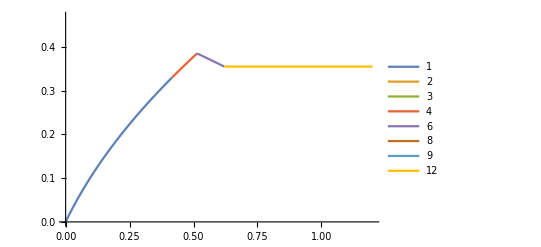

```mathematica
Show[Table[Plot[FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,iR1->x]],{x,0,1.2},PlotStyle->collr[[kk]],PlotRange->{All,{0,ymax}},PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]
```

```mathematica
AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{1->x,3->y}]]],Lighting->{{"Ambient",White}},MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]},PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}],ImageSize->700]]]
```

{36.9786,-Graphics3D-}

```mathematica
avcoord2=Table[Mean[Nest[First,overview,Length[lrlst]][[1,i,1,1,1;;-1,{1,2}]]],{i,Length[lrlst]}]
```

{{0.228666,0.800304},{0.648461,0.23799},{0.593973,0.740035},{0.359057,1.30909},{0.581297,1.2038},{1.24186,0.315141},{1.11418,0.684641},{1.01203,1.05838}}

```mathematica
vtxsz3=vtxsz2;
imgsz3=imgsz2;
thicc3=Thickness[0.008];
lbl=Table[Show[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,ReplacePart[xin,{iR1->avcoord2[[j,1]],iR2->avcoord2[[j,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc2},vtxsz3,imgsz3]],{j,Length[lrlst]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
dL=.8;
dD=.6;
eqcl=GatherBy[Range[1,Length[lrlst]],GraphMetabNetLoop[limcombi[[lrlst[[#]]]],system,ReplacePart[xin,{iR1->avcoord2[[#,1]],iR2->avcoord2[[#,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2]&]
coleqcl=Delete[ColorData[97,"ColorList"],2][[Range[1,Length[eqcl]]]];
cols=Table[Table[dc=(dD+dL)/(Length[eqcl[[i]]]+1);If[j*dc<dL,Lighter[coleqcl[[i]],dL-j*dc],Darker[coleqcl[[i]],j*dc-dL]],{j,Length[eqcl[[i]]]}],{i,Length[eqcl]}]
collr=Flatten[cols][[Table[Position[Flatten[eqcl],i][[1,1]],{i,Length[lrlst]}]]]
```

{{1,4},{2,6},{3},{5},{7},{8}}

{{RGBColor[0.5789446666666667, 0.6711860000000001, 0.806532],RGBColor[0.31929473333333336, 0.4392084666666667, 0.6151582666666668]},{RGBColor[0.7067873333333334, 0.7943793333333333, 0.46325666666666676],RGBColor[0.4854902000000001, 0.5993598000000001, 0.16890033333333337]},{RGBColor[0.9302733999999999, 0.44706340000000006, 0.28826110000000005]},{RGBColor[0.5756392, 0.5235616000000001, 0.7312159]},{RGBColor[0.7948710999999999, 0.4883986, 0.1921483000000001]},{RGBColor[0.42750820000000006, 0.6566509, 0.8041140999999999]}}

{RGBColor[0.5789446666666667, 0.6711860000000001, 0.806532],RGBColor[0.7067873333333334, 0.7943793333333333, 0.46325666666666676],RGBColor[0.9302733999999999, 0.44706340000000006, 0.28826110000000005],RGBColor[0.31929473333333336, 0.4392084666666667, 0.6151582666666668],RGBColor[0.5756392, 0.5235616000000001, 0.7312159],RGBColor[0.4854902000000001, 0.5993598000000001, 0.16890033333333337],RGBColor[0.7948710999999999, 0.4883986, 0.1921483000000001],RGBColor[0.42750820000000006, 0.6566509, 0.8041140999999999]}

```mathematica
AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,1.6},{y,0,1.6},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotLegends->{If[Position[eqcl,kk][[1,2]]==Length[eqcl[[Position[eqcl,kk][[1,1]]]]],lbl[[kk]],None]},MaxRecursion->5,MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,Length[lrlst]}],ImageSize->700]]]
```

{473.509,-Graphics3D-}

```mathematica
toy4=Show[overview,ViewPoint->{-1,-2,1},ViewAngle->35°]
Export[StringJoin["figures/fig4d.png"],toy4,"PNG",ImageResolution->resol];
Export[StringJoin["figures/fig4d.pdf"],toy4,"PDF"];
```

-Graphics3D-

## Glycolysis with Leibig’s Law

### Initialization of the full E. coli core model

```mathematica
-Graphics-;
```

#### Import the stoichiometric matrix

```mathematica
(*import the stoichiometric matrix of the full E. coli core model*)
dataS=Chop[Import["ecoli_core_model.xls",{"Sheets","Ecoli_core_S"}]];
reacs=dataS[[2;;-1,2;;-1]];
(*Manually add a metabolite line for the biomass*)
AppendTo[reacs,Table[If[i==13,1,0],{i,Dimensions[reacs][[2]]}]];
(*drop the reactions that correspond to the chemostat leakage of metabolites in solution (not part of the metabolic network per se*)
reacs=Transpose[Drop[Transpose[reacs],{20,39}]];

(*number of dynamical variable*)
n=Dimensions[reacs][[1]]
(*number of reactions*)
p=Dimensions[reacs][[2]]
```

73

75

#### Import the metabolites

```mathematica
(*import the table that contains all the info on the metabolites*)
dataM=Import["ecoli_core_model.xls",{"Sheets","metabolites"}];
(*metabo is the list of the names of all the metabolites, with [e] indicating extracellular metabolites*)
metabo=dataM[[2;;n,1]];
(*add "biomass" to the list*)
(*AppendTo[metabo,"biomass"];*)
AppendTo[metabo,"N"];
metabo

(*create sublists for metabolites*)
Sv={};Cv={};
(*separate metabolites between extracellular and intracellular; the last one is biomass*)
Do[If[StringContainsQ[metabo[[i]],"[e]"],AppendTo[Sv,i],AppendTo[Cv,i]],{i,1,n-1}]
Cv;
metabo[[Cv]];
Sv;
metabo[[Sv]];
Bv=n;
Pv={};

label=lblvar2[Sv,Bv,Pv,Cv];
```

{13dpg,2pg,3pg,6pgc,6pgl,ac,ac[e],acald,acald[e],accoa,acon-C,actp,adp,akg,akg[e],amp,atp,cit,co2,co2[e],coa,dhap,e4p,etoh,etoh[e],f6p,fdp,for,for[e],fru[e],fum,fum[e],g3p,g6p,glc-D[e],gln-L,gln-L[e],glu-L,glu-L[e],glx,h2o,h2o[e],h,h[e],icit,lac-D,lac-D[e],mal-L,mal-L[e],nad,nadh,nadp,nadph,nh4,nh4[e],o2,o2[e],oaa,pep,pi,pi[e],pyr,pyr[e],q8,q8h2,r5p,ru5p-D,s7p,succ,succ[e],succoa,xu5p-D,N}

#### Locate the metabolites that are involved in conservation laws

```mathematica
(*look for the nullspace of the stoichiometric matrix*)
stoich=IntegerPart[reacs[[Cv,Join[Range[1,12],Range[14,p]]]]];
nullspace=Transpose[NullSpace[Transpose[stoich]]];
Join[{metabo[[Cv]]},Transpose[nullspace]]//MatrixForm
(*from there, we can identify the metabolites involved in conservation laws*)
Table[metabo[[Cv]][[Flatten[Position[Transpose[nullspace][[i]],1]]]],{i,Dimensions[nullspace][[2]]}]
metacons=metabo[[Cv]][[Flatten[Position[Total[Transpose[nullspace]],1]]]]
Mv=Flatten[Table[Position[metabo,i],{i,metacons}]]
```

(13dpg | 2pg | 3pg | 6pgc | 6pgl | ac | acald | accoa | acon-C | actp | adp | akg | amp | atp | cit | co2 | coa | dhap | e4p | etoh | f6p | fdp | for | fum | g3p | g6p | gln-L | glu-L | glx | h2o | h | icit | lac-D | mal-L | nad | nadh | nadp | nadph | nh4 | o2 | oaa | pep | pi | pyr | q8 | q8h2 | r5p | ru5p-D | s7p | succ | succoa | xu5p-D
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

{{accoa,coa,succoa},{q8,q8h2},{nadp,nadph},{nad,nadh},{adp,amp,atp}}

{accoa,adp,amp,atp,coa,nad,nadh,nadp,nadph,q8,q8h2,succoa}

{10,13,16,17,21,50,51,52,53,64,65,71}

#### Import the metabolic reactions

```mathematica
(*load the equations of the chemical reactions*)
dataR=Import["ecoli_core_model.xls",{"Sheets","reactions"}];
reacnames=Drop[dataR[[2;;-1,1]],{20,39}][[1;;p]];
(*first, remove the equations that correspond to the chemostat leakage of metabolites in solution (see above)*)
chemreac=dataR[[Join[Range[2,20],Range[41,Length[dataS[[1,1;;-1]]]]],3]];

(*chemreac[[revreac]]//MatrixForm
chemreac[[41]]
Table[If[StringContainsQ[chemreac[[i]],"pyr"], i,"_"], {i,revreac}]
Table[If[StringContainsQ[chemreac[[i]],"pyr"], i,"_"], {i,1,n}]*)

(*(*these are the reverse-order reactions that were identified as completely necessary to add to the network*)
essentreac={18,33,55,57,66,70};
(*also added 14 for co2, 49 for nh4 & 38 for h2o, 50 for o2, 58 for pi/h, 62 for actp to be turned back into accoa to leak out of the system!!*)
essentreac={14,18,33,38,49,50,55,57,58,62,66,70};
(*also let protons leak out to equilibriate!*)
essentreac={12,14,18,33,38,49,50,55,57,58,62,66,70};
(*but maybe pyruvate leaching out is not super cool... let's get rid of 64, also, let's not make lactate because it also leaches out*)
(*essentreac=Complement[revreac,{41,64}];*)*)

(*ADD ALL REVERSIBLE REACTIONS*)
(*length of the forward reactions only (avoiding to double plot forward and backward ways for reversible reactions)*)
p2=Length[chemreac];
(*loop to select all the reversible reactions, where the symbol"<==>" appears*)
revreac={};
Do[If[StringContainsQ[chemreac[[i]],"<==>"],AppendTo[revreac,i]],{i,1,p2}];
(*alternative option: add all reversible reactions!*)
essentreac=revreac;

(*here, add 0 more randomly picked reverse-order reactions to the network*)
Complement[revreac,essentreac];
extrareac=Union[RandomSample[Complement[revreac,essentreac],0],essentreac];

(*rename the biomass creation reaction*)
reacnames[[13]]="μ"
(*only select the actual reaction names (rest are empty names), then add the reversible reaction with a notation _r*)
reacnames2=Join[reacnames[[1;;p2]],Table[reacnames[[i]]<>"_r",{i,extrareac}]]

(*new stoichiometric matrix*)
S=Join[reacs,-reacs[[All,extrareac]],2];
(*new number of reactions*)
p=Dimensions[S][[2]]
```

μ

{ACALD,ACALDt,ACKr,ACONTa,ACONTb,ACt2r,ADK1,AKGDH,AKGt2r,ALCD2x,ATPM,ATPS4r,μ,CO2t,CS,CYTBD,D_LACt2,ENO,ETOHt2r,FBA,FBP,FORt2,FORti,FRD7,FRUpts2,FUM,FUMt2_2,G6PDH2r,GAPD,GLCpts,GLNS,GLNabc,GLUDy,GLUN,GLUSy,GLUt2r,GND,H2Ot,ICDHyr,ICL,LDH_D,MALS,MALt2_2,MDH,ME1,ME2,NADH16,NADTRHD,NH4t,O2t,PDH,PFK,PFL,PGI,PGK,PGL,PGM,PIt2r,PPC,PPCK,PPS,PTAr,PYK,PYRt2r,RPE,RPI,SUCCt2_2,SUCCt3,SUCDi,SUCOAS,TALA,THD2,TKT1,TKT2,TPI,ACALD_r,ACALDt_r,ACKr_r,ACONTa_r,ACONTb_r,ACt2r_r,ADK1_r,AKGt2r_r,ALCD2x_r,ATPS4r_r,CO2t_r,D_LACt2_r,ENO_r,ETOHt2r_r,FBA_r,FUM_r,G6PDH2r_r,GAPD_r,GLUDy_r,GLUt2r_r,H2Ot_r,ICDHyr_r,LDH_D_r,MDH_r,NH4t_r,O2t_r,PGI_r,PGK_r,PGM_r,PIt2r_r,PTAr_r,PYRt2r_r,RPE_r,RPI_r,SUCOAS_r,TALA_r,TKT1_r,TKT2_r,TPI_r}

114

#### Graphing the metabolic network

```mathematica
GraphMetabNet[{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},coord_,szvtx_,szim_]:=Graph[verts[submeta,subreac],edges[S,subreac],
VertexLabels->vertlabels[submeta,subreac,metabo,reacnames],
PlotTheme->"IndexLabeled",
VertexStyle->vertstyle[submeta,subreac],VertexSize->{"Scaled",szvtx},
(*VertexShapeFunction->Flatten[{Table[j->Automatic,{j,submeta}],Table[(n+i)->vf1,{i,subreac}]}],*)
VertexCoordinates->If[ToString[coord]=="Automatic",Automatic,Flatten[{Table[j->coord[[j]],{j,submeta}],Table[(n+i)->coord[[n+i]],{i,subreac}]}]],
VertexShapeFunction->Flatten[{Table[j->vf1,{j,submeta}],Table[(n+i)->Automatic,{i,subreac}]}],ImageSize->szim]
```

```mathematica
(*total number of nodes*)
ntot=Length[Flatten[{Table[j->Placed[metabo[[j]],Center],{j,n}],Table[(n+i)->Placed[Subscript[v,i],Center],{i,p}]}]];
(*manually entered coordinates for the nodes of E. coli core model*)
coord={{0,8},{0,6},{0,7},{2,12},{1,12},{2,1},{2,0},{3,3},{3,0},{2,3},{7,3},{2,2},{11.5,11},{9,4},{13,5},{11,12},{11.5,12},{6,3},{9,1},{9,0},{1.5,2.5},{1,9},{3,9},{4,1},{4,0},{4,9},{0,10},{1,2},{1,0},{-1,12},{6,7},{6,13},{4,10},{0,12},{0,13},{12,2},{13,2},{12,4},{13,4},{7,5},{7,1},{7,0},{12,11},{13,11},{8,3},{0,1},{0,0},{5,6},{5,13},{9,12},{8,12},{8,11},{10,11},{11,1},{11,0},{11,10},{13,10},{5,4},{0,5},{6,1},{6,0},{0,3},{-1,3},{12,9},{11,9},{4,11},{4,12},{3,10},{8,7},{13,7},{9,6},{3,11},{7,9},{2.5,3},{3,.5},{2,1.5},{6.5,3},{7.5,3},{2,.5},{11,11.5},{9,5},{12,5},{3.5,2.5},{11.5,11.5},{12.5,11},{6,9},{9,.5},{5.5,3.5},{11.5,9.5},{0,.5},{0,5.5},{4,.5},{0,9.5},{-.5,10.5},{.5,.5},{1,.5},{7,8},{-.5,12},{5.5,6.5},{6,12.5},{.5,12},{0,8.5},{0,12.5},{12.5,3},{12.5,2},{11,4},{12,3},{11.5,3},{12.5,4},{3,12},{7,.5},{8.5,3.5},{8,4},{0,2},{6,5},{5,12.5},{5,5},{2.5,6},{2.5,5},{12,8},{9,11},{11,.5},{12,10},{1,3.5},{0,10.5},{1,2.5},{0,11.5},{0,7.5},{1.5,12},{0,6.5},{6,.5},{1,5},{1,4},{0,4},{2,2.5},{.5,4},{-.5,3},{3.5,11.5},{4,11.5},{11,6},{11,7},{7,7},{8.5,6.5},{3.5,9.5},{8.5,12.5},{3.5,10.5},{2,10},{1,9.5}};
(*add coordinates for backward reactions, basically at same location as the forward one; will be useful below*)
coord2=Join[coord,Table[coord[[n+1;;n+p2]][[i]],{i,extrareac}]];
```

```mathematica
system={S,metabo,reacnames,Range[1,n],Range[1,p2],α,μ};
GraphMetabNet[system,coord,0.025,700]
```

-Graphics-

```mathematica
(*search tools, for debogging*)
(*Flatten[Table[If[StringContainsQ[chemreac[[i]],"h[e]"], i,{}], {i,n}]]
chemreac[[Flatten[Table[If[StringContainsQ[chemreac[[i]],"h[e]"], i,{}], {i,n}]]]]
chemreac[[Flatten[Table[If[StringContainsQ[chemreac[[i]],"atp"], i,{}], {i,n}]]]]
metabo[[17]]
coord[[43]]
Flatten[{Table[metabo[[j]],{j,n}],Table[reacnames2[[i]],{i,p}]}]*)

(*bit of code to look at the network dynamically*)
(*tt=20;
Graph[verts,edges,VertexLabels->Flatten[{Table[j->Placed[metabo[[j]],Center],{j,n}],Table[(n+i)->Placed[Subscript[v,i],Center],{i,p2}]}],
VertexStyle->vertstyle,
EdgeStyle->edgstyle[Map[Lighter[Black,1-#]&,vt[tt]/Max[vt[10]]]],
VertexSize->{"Scaled",.019},
VertexShapeFunction->Flatten[{Table[j->Automatic,{j,n}],Table[(n+i)->vf1,{i,p2}]}],
VertexCoordinates->Table[j->coord[[j]],{j,Length[coord]}]]*)
```

### Focus on the Glycolysis pathway

```mathematica
-Graphics-;
```

#### Building the subsystem

```mathematica
(*tools to find positions of reactions*)
(*Position[reacnames,"FRUpts2"]
Position[metabo,"atp"]*)

(*Glycolysis pathway with removed PPS and amp*)
glycr={"GLCpts","PGI","PFK","FBP","FBA","TPI","GAPD","PGK","PGM","ENO","PYK","PIt2r","μ","FRUpts2"};
(*among which a few are reversible*)
glycrev=Join[glycr,Table[el<>"_r",{el,Intersection[Table[reacnames[[i]],{i,extrareac}],glycr]}]];
(*metabolites involveds in the subnetwork*)
glycm={"glc-D[e]","g6p","f6p","fdp","dhap","g3p","13dpg","3pg","2pg","pep","pyr","h","h[e]","h2o","adp","atp","pi","pi[e]","nad","nadh","fru[e]","N"};
(*REMOVED h2o MIGHT BREAK EVERYTHING*)
glycm={"glc-D[e]","g6p","f6p","fdp","dhap","g3p","13dpg","3pg","2pg","pep","pyr","h","h[e]","adp","atp","pi","pi[e]","nad","nadh","fru[e]","N"};

subr=glycr;
subrrev=glycrev;
subm=glycm;

(*get indices; only irreversible reactions*)
subreac=Sort[Flatten[Table[Position[reacnames,subr[[i]]],{i,Length[subr]}]]];
(*get indices; with reversible reactions*)
subreac2=Sort[Flatten[Table[Position[reacnames2,subrrev[[i]]],{i,Length[subrrev]}]]];

(*BUILDING THE ADAPTED STOICH MATRIX OF GLYCOLYSIS*)
S2=S;
(*singling out the biomass reaction*)
GAMi=13;
(*simplified biomass reaction that uses 1 pyr, 1 NADH and 1 ATP*)
Do[S2[[i,GAMi]]=0.,{i,Length[S2[[All,13]]]}]
Do[S2[[i,GAMi]]=-1.,{i,{17,51,62}}]
(*and creates 1 cell, 1 NAD and 1 ADP*)
Do[S2[[i,GAMi]]=1.,{i,{13,50,73}}]

(*remove water creation, because it is only a product, no effect here*)
S2[[41,18]]=0;

(*when we create one new cell, it also creates the NAD and NAD that comes with it (newborn cells are "discharged");other scenarios are possible, as long as they maintain mass balance of the conserved pools! *)
(*total amount of balanced mass: crucial for keeping conserved metabolites mass-balanced by the birth reaction*)
massbal0=3;
Do[S2[[i,GAMi]]=S2[[i,GAMi]]+2*massbal0,{i,{13,50}}]

(*simplified network where only chosen one way, getting rid of competing reverse reactions; list has been hand picked*)
subreac2=Sort[{13,25,30,54,52,20,75,29,103,104,18,63,58,105}];
submeta=Sort[Flatten[Table[Position[metabo,subm[[i]]],{i,Length[subm]}]]];
(*Ssub=S[[1;;-1,subreac]];*)
Ssub=S2[[1;;-1,subreac2]];
notwork=Transpose[Join[{Join[{"_"},metabo[[submeta]]]},Transpose[Join[{reacnames2[[subreac2]]},Ssub[[submeta,All]]]]]]//MatrixForm
```

(_ | μ | ENO | FBA | FRUpts2 | GAPD | GLCpts | PFK | PGI | PIt2r | PYK | TPI | PGK_r | PGM_r | PIt2r_r
13dpg | 0. | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0
2pg | 0. | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
3pg | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -1. | 0
adp | 7. | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | -1. | 0 | -1. | 0 | 0
atp | -1. | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 1. | 0 | 1. | 0 | 0
dhap | 0. | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0
f6p | 0. | 0 | 0 | 1. | 0 | 0 | -1. | 1. | 0 | 0 | 0 | 0 | 0 | 0
fdp | 0. | 0 | -1. | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
fru[e] | 0. | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
g3p | 0. | 0 | 1. | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
g6p | 0. | 0 | 0 | 0 | 0 | 1. | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0
glc-D[e] | 0. | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
h | 0. | 0 | 0 | 0 | 1. | 0 | 1. | 0 | 1. | -1. | 0 | 0 | 0 | -1.
h[e] | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 1.
nad | 7. | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nadh | -1. | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
pep | 0. | 1. | 0 | -1. | 0 | -1. | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0
pi | 0. | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | -1.
pi[e] | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 1.
pyr | -1. | 0 | 0 | 1. | 0 | 1. | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
N | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Plotting the network

```mathematica
(*locating the minimal pathway with the E. coli core model*)
(*GraphMetabNet[S2,Range[1,n],subreac2,coord2]*)
system={S2,metabo,reacnames2,Range[1,n],subreac2,α,μ};
GraphMetabNet[system,coord2,0.025,700]
(*GraphMetabNet[S2,submeta,subreac,coord];
GraphMetabNet[S2,submeta,subreac2,coord2];*)

(*Alternative representation that makes more explicit the circular nature of the pathway*)
cordstyle={1->{4.72,3.6},2->{0.84,3.81},3->{2.55,4.13},13->{4.02,2.48},17->{4.5,2.5},22->{7.38,0.51},26->{3.31,0.79},27->{5.51,0.98},30->{1.67,0.59},33->{6.54,1.72},34->{1.94,0.16},35->{0.89,0.78},41->{0.,3.02},43->{5.18,2.39},44->{7.11,2.99},50->{4.69,2.87},51->{4.68,3.19},59->{2.05,2.},60->{5.8,3.2},61->{6.96,3.4},62->{2.78,1.87},73->{2.,3.5},86->{3.,3.},91->{0.92,2.85},93->{6.57,0.84},98->{2.39,1.17},102->{5.52,2.82},103->{1.79,1.16},125->{4.4,1.61},127->{2.68,0.},131->{6.4,3.2},136->{3.53,2.12},148->{7.37,1.12},176->{3.65,3.42},177->{1.53,4.34},178->{6.41,2.82}};
coordsub=Table[{0,0},{i,n+p}];
Do[coordsub[[cordstyle[[j,1]]]]=cordstyle[[j,2]],{j,Length[cordstyle]}];
(*GraphMetabNet[S2,submeta,subreac2,coordsub]*)

system={S2,metabo,reacnames2,submeta,subreac2,α,μ};
vtxsz=.03;
imgsz=700;
graphglyc=GraphMetabNet[system,coordsub,vtxsz,imgsz]
Export[StringJoin["figures/graphglyc.png"],graphglyc,"PNG"];
Export[StringJoin["figures/graph2glyc.pdf"],graphglyc,"PDF"];
```

-Graphics-

-Graphics-

### Simulating the network

```mathematica
(*WARNING, MAKE SURE S IS REPLACED BY S2 EVERYWHERE*)
```

#### Setting the parameters

```mathematica
(*mortality function, potentially penalized by the number of reactions in the metabolic network (trade-off)*)
c=0;
m0=.1;
m[S_]:=m0+c*Dimensions[SparseArray[S]][[2]];

(*stoichiometric coefficient converting cell number into metabolite concentrations*)
qB=1;

(*BUILDING α AND μ, THE REACTION RATES COEFFICIENTS *)
(*locate all reactants for each reaction*)
input=Position[Normal[S2],_?(#<0&)];
(*(*randomly generated parameters*)
α=SparseArray[Table[k->RandomReal[],{k,input}]];
α//MatrixForm;
μ=Table[3*RandomReal[],{k,p}];*)
(*pick all coefficients equal to one*)
α=SparseArray[Table[k->1,{k,input}]];
α//MatrixForm;
μ=Table[1,{k,p}];
(*EXCEPT conversion from PEP to PYR HAS TO BE slowed down for the cell to be viable*)
μ[[63]]=.2;

(*building the supply vectors*)
Clear[xin]
(*list of all the extracellular metabolites in the Glycolysis pathway*)
Intersection[Sv,submeta];
(*of the 4 extracellular metabolites, we removed fructose (30)*)
essent={35,44,61};
metabo[[essent]]

(*DEBUGGING TOOL ONLY; fxdi={} does not do anything*)
(*pick some metabolites and set them at fixed value*)
Table[{k,metabo[[k]]},{k,Cv}];
fxdi={};
fxdval=.1;

(*set all the essential metbolites to 1 by default*)
xin=Table[0,{i,n}];
Do[xin[[i]]=1.,{i,essent}];
```

{glc-D[e],h[e],pi[e]}

#### Simulating equilibration of the internal dynamics

```mathematica
(*glucose set to .1, to make it the limiting factor*)
xin[[35]]=.1;

(*SET THE INITIAL CONDITION*)
(*non-supplied extracell metabolites start at 0 concentration, supplied start at the value at which they are supplied (will stay there)*)
(*biomass starts at .1 (does not matter, no dynamics) *)
(*All intracellular metabolites are set at 1, except the conserved ones set at the SAME value as in the stoichiometric matrix (to ensure they are conserved)*)
condini=Table[If[MemberQ[Sv,i],If[xin[[i]]==0,x[i]->0,x[i]->xin[[i]]],If[i==Bv,x[i]->.1,If[MemberQ[Mv,i],x[i]->massbal0,x[i]->1]]],{i,n}];

(*gather all of the important bits into a simgle object*)
system={S2,metabo,reacnames2,submeta,subreac2,α,μ};
(*build the Quasi Steasy State dynamics: total population stays put, metabolites respond to fixed extracellular concentrations, eventually equilibrate due to dilution by growth*)
SetQSSAModel[system,xin]

(*ONLY USEFUL WITH FXDI DEBOGGING TOOL*)
sub=Delete[Range[1,n],{{6},{8},{24},{46}}];
sub=Complement[Range[1,n],Union[{6,8,24,46},fxdi]];
sub=Complement[submeta,fxdi];

(*DISPLAYS THE EQUATIONS*)
MatrixForm[model[[1,2,1+Flatten[Table[Position[Table[i,{i,Complement[Intersection[Cv,submeta],fxdi]}],i],{i,sub}]]]],TableAlignments->Left]

tmax=300;
sol=EcoSim[condini,tmax];

figtraj=PlotDynamics[sol,Table[x[i],{i,Intersection[sub,Cv]}],Logged->True,PlotLegends->metabo[[Intersection[sub,Cv]]],AxesLabel->{"time",""}]
DisplayFinalSlice[system,xin,FinalSlice[sol]]
```

(Component[x[1]]→{Equation:>0.-1. Min[5,x[1][t],x[13][t]]+1. Min[5,x[33][t],x[50][t],x[60][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[1][t],Color→RGBColor[0.880722, 0.611041, 0.142051],Type→Intensive}
Component[x[2]]→{Equation:>0.-1. Min[5,x[2][t]]+1. Min[5,x[3][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[2][t],Color→RGBColor[0.560181, 0.691569, 0.194885],Type→Intensive}
Component[x[3]]→{Equation:>0.-1. Min[5,x[3][t]]+1. Min[5,x[1][t],x[13][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[3][t],Color→RGBColor[0.922526, 0.385626, 0.209179],Type→Intensive}
Component[x[13]]→{Equation:>0.-1. Min[5,x[1][t],x[13][t]]+1. Min[5,x[17][t],x[26][t]]-0.2 Min[5,x[13][t],x[43][t],x[59][t]]+7. Min[5,x[17][t],x[51][t],x[62][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[13][t],Color→RGBColor[0.736782672705901, 0.358, 0.5030266573755369],Type→Intensive}
Component[x[17]]→{Equation:>0.+1. Min[5,x[1][t],x[13][t]]-1. Min[5,x[17][t],x[26][t]]+0.2 Min[5,x[13][t],x[43][t],x[59][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[17][t],Color→RGBColor[0.560181, 0.691569, 0.194885],Type→Intensive}
Component[x[22]]→{Equation:>0.-1. Min[5,x[22][t]]+1. Min[5,x[27][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[22][t],Color→RGBColor[1, 0.75, 0],Type→Intensive}
Component[x[26]]→{Equation:>0.+1. Min[0,x[59][t]]+1. Min[5,x[34][t]]-1. Min[5,x[17][t],x[26][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[26][t],Color→RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],Type→Intensive}
Component[x[27]]→{Equation:>0.-1. Min[5,x[27][t]]+1. Min[5,x[17][t],x[26][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[27][t],Color→RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],Type→Intensive}
Component[x[33]]→{Equation:>0.+1. Min[5,x[22][t]]+1. Min[5,x[27][t]]-1. Min[5,x[33][t],x[50][t],x[60][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[33][t],Color→RGBColor[0.922526, 0.385626, 0.209179],Type→Intensive}
Component[x[34]]→{Equation:>0.+1. Min[0.1,x[59][t]]-1. Min[5,x[34][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[34][t],Color→RGBColor[0.528488, 0.470624, 0.701351],Type→Intensive}
Component[x[43]]→{Equation:>1.+1. Min[5,x[17][t],x[26][t]]-1. Min[5,x[43][t],x[60][t]]-0.2 Min[5,x[13][t],x[43][t],x[59][t]]+1. Min[5,x[33][t],x[50][t],x[60][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[43][t],Color→RGBColor[0.736782672705901, 0.358, 0.5030266573755369],Type→Intensive}
Component[x[50]]→{Equation:>0.+7. Min[5,x[17][t],x[51][t],x[62][t]]-1. Min[5,x[33][t],x[50][t],x[60][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[50][t],Color→RGBColor[0.772079, 0.431554, 0.102387],Type→Intensive}
Component[x[51]]→{Equation:>0.-1. Min[5,x[17][t],x[51][t],x[62][t]]+1. Min[5,x[33][t],x[50][t],x[60][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[51][t],Color→RGBColor[0.363898, 0.618501, 0.782349],Type→Intensive}
Component[x[59]]→{Equation:>0.-1. Min[0,x[59][t]]-1. Min[0.1,x[59][t]]+1. Min[5,x[2][t]]-0.2 Min[5,x[13][t],x[43][t],x[59][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[59][t],Color→RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],Type→Intensive}
Component[x[60]]→{Equation:>1.-1. Min[5,x[43][t],x[60][t]]-1. Min[5,x[33][t],x[50][t],x[60][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[60][t],Color→RGBColor[0.368417, 0.506779, 0.709798],Type→Intensive}
Component[x[62]]→{Equation:>0.+1. Min[0,x[59][t]]+1. Min[0.1,x[59][t]]+0.2 Min[5,x[13][t],x[43][t],x[59][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[62][t],Color→RGBColor[0.560181, 0.691569, 0.194885],Type→Intensive})

NDSolve::dvnoarg: The function x' appears with no arguments.

FilterRules::rep: x'==Equation[x] is not a valid replacement rule.

Join::heads: Heads FilterRules and List at positions 1 and 2 are expected to be the same.

PlotDynamics[SortRuleList[Join[FilterRules[{x'==Equation[x],x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,WhenEvent[t==1,x[t]→1],WhenEvent[t==2,x[t]→1],WhenEvent[t==3,x[t]→1],WhenEvent[t==13,x[t]→3],WhenEvent[t==17,x[t]→3],WhenEvent[t==22,x[t]→1],WhenEvent[t==26,x[t]→1],WhenEvent[t==27,x[t]→1],WhenEvent[t==33,x[t]→1],WhenEvent[t==34,x[t]→1],WhenEvent[t==43,x[t]→1],WhenEvent[t==50,x[t]→3],WhenEvent[t==51,x[t]→3],WhenEvent[t==59,x[t]→1],WhenEvent[t==60,x[t]→1],WhenEvent[t==62,x[t]→1],WhenEvent[t==73,x[t]→0.1]},{x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x}],{x[73]→InterpolatingFunction[…],x[1]→InterpolatingFunction[…],x[2]→InterpolatingFunction[…],x[3]→InterpolatingFunction[…],x[13]→InterpolatingFunction[…],x[17]→InterpolatingFunction[…],x[22]→InterpolatingFunction[…],x[26]→InterpolatingFunction[…],x[27]→InterpolatingFunction[…],x[33]→InterpolatingFunction[…],x[34]→InterpolatingFunction[…],x[43]→InterpolatingFunction[…],x[50]→InterpolatingFunction[…],x[51]→InterpolatingFunction[…],x[59]→InterpolatingFunction[…],x[60]→InterpolatingFunction[…],x[62]→InterpolatingFunction[…]}],{x[73],x[1],x[2],x[3],x[13],x[17],x[22],x[26],x[27],x[33],x[34],x[43],x[50],x[51],x[59],x[60],x[62]}],{x[1],x[2],x[3],x[13],x[17],x[22],x[26],x[27],x[33],x[34],x[43],x[50],x[51],x[59],x[60],x[62]},Logged→True,PlotLegends→{13dpg,2pg,3pg,adp,atp,dhap,f6p,fdp,g3p,g6p,h,nad,nadh,pep,pi,pyr},AxesLabel→{time,}]

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FilterRules::rep: x'==Equation[x] is not a valid replacement rule.

Join::heads: Heads FilterRules and List at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Transpose::nmtx: The first two levels of … cannot be transposed.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

```mathematica
xin[[35]]=1;
condini=Table[If[MemberQ[Sv,i],If[xin[[i]]==0,x[i]->0,x[i]->xin[[i]]],If[i==Bv,x[i]->.1,If[MemberQ[Mv,i],x[i]->massbal0,x[i]->1]]],{i,n}];
SetQSSAModel[system,xin]

tmax=300;
sol=EcoSim[condini,tmax];
fslice=FinalSlice[sol];

figtraj=PlotDynamics[sol,Table[x[i],{i,Intersection[sub,Cv]}],Logged->True,PlotLegends->metabo[[Intersection[sub,Cv]]],AxesLabel->{"time",""}]
DisplayFinalSlice[system,xin,FinalSlice[sol]]
```

NDSolve::dvnoarg: The function x' appears with no arguments.

FilterRules::rep: x'==Equation[x] is not a valid replacement rule.

Join::heads: Heads FilterRules and List at positions 1 and 2 are expected to be the same.

PlotDynamics[SortRuleList[Join[FilterRules[{x'==Equation[x],x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,WhenEvent[t==1,x[t]→1],WhenEvent[t==2,x[t]→1],WhenEvent[t==3,x[t]→1],WhenEvent[t==13,x[t]→3],WhenEvent[t==17,x[t]→3],WhenEvent[t==22,x[t]→1],WhenEvent[t==26,x[t]→1],WhenEvent[t==27,x[t]→1],WhenEvent[t==33,x[t]→1],WhenEvent[t==34,x[t]→1],WhenEvent[t==43,x[t]→1],WhenEvent[t==50,x[t]→3],WhenEvent[t==51,x[t]→3],WhenEvent[t==59,x[t]→1],WhenEvent[t==60,x[t]→1],WhenEvent[t==62,x[t]→1],WhenEvent[t==73,x[t]→0.1]},{x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x}],{x[73]→InterpolatingFunction[…],x[1]→InterpolatingFunction[…],x[2]→InterpolatingFunction[…],x[3]→InterpolatingFunction[…],x[13]→InterpolatingFunction[…],x[17]→InterpolatingFunction[…],x[22]→InterpolatingFunction[…],x[26]→InterpolatingFunction[…],x[27]→InterpolatingFunction[…],x[33]→InterpolatingFunction[…],x[34]→InterpolatingFunction[…],x[43]→InterpolatingFunction[…],x[50]→InterpolatingFunction[…],x[51]→InterpolatingFunction[…],x[59]→InterpolatingFunction[…],x[60]→InterpolatingFunction[…],x[62]→InterpolatingFunction[…]}],{x[73],x[1],x[2],x[3],x[13],x[17],x[22],x[26],x[27],x[33],x[34],x[43],x[50],x[51],x[59],x[60],x[62]}],{x[1],x[2],x[3],x[13],x[17],x[22],x[26],x[27],x[33],x[34],x[43],x[50],x[51],x[59],x[60],x[62]},Logged→True,PlotLegends→{13dpg,2pg,3pg,adp,atp,dhap,f6p,fdp,g3p,g6p,h,nad,nadh,pep,pi,pyr},AxesLabel→{time,}]

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FilterRules::rep: x'==Equation[x] is not a valid replacement rule.

Join::heads: Heads FilterRules and List at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Transpose::nmtx: The first two levels of … cannot be transposed.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

```mathematica
(*function to compute the fitness gradient*)
nabg0[xeq_,μv_?(VectorQ[#,NumericQ]&)]:=Module[{fin,xeqs,ceq,veq,Kb,Kc,Jf,q,pp,grd},
xeqs=Table[x[i]->xeq[[i]],{i,n}];
ceq=xeq[[Intersection[Cv,submeta]]];
q=Length[ceq];
pp=Length[subreac2];
veq=Table[vb[j,xeq,S2,α,μv],{j,subreac2}];
Kb=S[[{Bv},subreac2]];
Kc=S[[Intersection[Cv,submeta],subreac2]];
Jf=D[Table[vb[j,Table[x[k],{k,n}],S2,α,μv],{j,subreac2}],{Table[x[k],{k,Intersection[Cv,submeta]}]}]/.xeqs;
grd=(Kb.(Jf.Inverse[(Dot[Kb,veq][[1]]*IdentityMatrix[q]-(Kc-Transpose[{ceq}].Kb).Jf)].(Kc-Transpose[{ceq}].Kb)+IdentityMatrix[pp]).DiagonalMatrix[veq].DiagonalMatrix[1/μv[[subreac2]]])[[1]];
Table[If[MemberQ[subreac2,i],grd[[Position[subreac2,i][[1,1]]]],0],{i,p}]]
```

```mathematica
μ=Table[1,{k,p}];
μ[[63]]=.2;
grad=nabg0[Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}]/.FinalSlice[sol],μ];
Join[{{"rate","reaction","code","lim metabo","gradient"}},Sort[Transpose[{(Table[vb[j,Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}],S2,α,μ],{j,subreac2}]/.FinalSlice[sol])//N,reacnames2[[subreac2]],subreac2,Table[lst=Flatten[Position[Normal[Transpose[S2][[i]]],_?(#<0&)]];
argmin=Ordering[Flatten[{Table[(α[[k,i]]*Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}][[k]]),{k,lst}],gmax}]/.FinalSlice[sol],1];
Flatten[{metabo[[lst]],"max"}][[argmin]],{i,subreac2}],Table[grad[[j]],{j,subreac2}]}]]]//MatrixForm
```

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of … does not exist.

Part::partw: Part 4 of … does not exist.

Part::partw: Part 5 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

FilterRules::rep: x'==Equation[x] is not a valid replacement rule.

Join::heads: Heads FilterRules and List at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FilterRules::rep: x'==Equation[x] is not a valid replacement rule.

Join::heads: Heads FilterRules and List at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FilterRules::rep: x'==Equation[x] is not a valid replacement rule.

General::stop: Further output of FilterRules::rep will be suppressed during this calculation.

Join::heads: Heads FilterRules and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{0,0,0,0,1.,0,0,0,0,0,«4»},{0,-1.,0,0,0,0,0,0,0,0,«4»},{-1.496,0,0,0,0,0,0,0,0,0,«4»},{59.81,0,0,0,0,0,1.,0,0,-1.,«4»},{-59.81,0,0,0,0,0,-1.,0,0,1.,«4»},{0,0,1.,0,0,0,0,0,0,0,«4»},{-0.0709,0,0,1.,0,0,-1.,1.,0,0,«4»},{0,0,-1.,0,0,0,1.,0,0,0,«4»},{-0.129,0,1.,0,-1.,0,0,0,0,0,«4»},{-0.205,0,0,0,0,1.,0,-1.,0,0,«4»},«6»}+{-({x[1],x[2],x[3],x[4],x[5],x[6],0,x[8],0,x[10],«63»}/.FinalSlice[SortRuleList[Join[«2»],{«17»}]])⟦{1,2,3,13,17,22,26,27,33,34,«6»}⟧,0,0,0,0,0,0,0,0,0,«4»} cannot be combined.

Thread::tdlen: Objects of unequal length in {-({x[1],x[2],x[3],x[4],x[5],x[6],0,x[8],0,x[10],«63»}/.FinalSlice[SortRuleList[Join[«2»],{«17»}]])⟦{1,2,3,13,17,22,26,27,33,34,«6»}⟧,0,0,0,0,0,0,0,0,0,«4»}+{{0,0,0,0,1.,0,0,0,0,0,«4»},{0,-1.,0,0,0,0,0,0,0,0,«4»},{-1.496,0,0,0,0,0,0,0,0,0,«4»},{59.81,0,0,0,0,0,1.,0,0,-1.,«4»},{-59.81,0,0,0,0,0,-1.,0,0,1.,«4»},{0,0,1.,0,0,0,0,0,0,0,«4»},{-0.0709,0,0,1.,0,0,-1.,1.,0,0,«4»},{0,0,-1.,0,0,0,1.,0,0,0,«4»},{-0.129,0,1.,0,-1.,0,0,0,0,0,«4»},{-0.205,0,0,0,0,1.,0,-1.,0,0,«4»},«6»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Dot::dotsh: Tensors … and {{Divide[0. + <<1>> + Min[5, <<2>>, ({x[1], x[2], x[3], x[4], x[5], x[6], 0, <<62>>, 0, x[71], x[72], x[73]} /. <<1>>)[[62]]], -<<1>> + <<1>>], <<1>>}, {<<2>>}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

$Aborted

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FilterRules::rep: x'==Equation[x] is not a valid replacement rule.

Join::heads: Heads FilterRules and List at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 13 of … does not exist.

Part::partw: Part 18 of … does not exist.

Part::partw: Part 20 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of … cannot be transposed.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

$Aborted

### Extra

#### Fluctuating conditions (OLD, IGNORE)

```mathematica
FindLimMetabo2[{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},slice_]:=Module[{lst,argmin},
Table[lst=Flatten[Position[Normal[Transpose[S][[i]]],_?(#<0&)]];
argmin=Ordering[Flatten[{Table[(α[[k,i]]*Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}][[k]]),{k,lst}],gmax}]/.slice,1];
Flatten[{lst,n+1}][[argmin[[1]]]],{i,subreac}]]
```

```mathematica
T=100;
T=20;
(*function to set the QSSA model*)
SetQSSAModelFluc[{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{},
model={Pop[pop]->Flatten[{Table[Component[x[i]]->{Equation:>0,Color->Colf[i]},{i,{Bv}}],Table[Component[x[i]]->{Equation:>Evaluate[qB*S[[i,subreac]].Table[vb[j,Table[If[MemberQ[Sv,k],If[k==35,xin[k]*(1+Sin[2*Pi*t/T]),xin[k]],If[MemberQ[fxdi,k],fxdval,x[k][t]]],{k,n}],S,α,μ],{j,subreac}]-If[MemberQ[{},i],0,qB*x[i][t]*S[[Bv,GAMi]]*vb[GAMi,Table[If[MemberQ[Sv,k],xin[k],If[MemberQ[fxdi,k],fxdval,x[k][t]]],{k,n}],S,α,μ]]],Color->Colf[i],Type->"Intensive"},{i,Complement[Intersection[Cv,submeta],fxdi]}]}]};
SetModel[model]]
```

```mathematica
(*glucose set to .1, to make it the limiting factor*)
xin[35]=.1;

(*SET THE INITIAL CONDITION*)
(*non-supplied extracell metabolites start at 0 concentration, supplied start at the value at which they are supplied (will stay there)*)
(*biomass starts at .1 (does not matter, no dynamics) *)
(*All intracellular metabolites are set at 1, except the conserved ones set at the SAME value as in the stoichiometric matrix (to ensure they are conserved)*)
condini=Table[If[MemberQ[Sv,i],If[xin[i]==0,x[i]->0,x[i]->xin[i]],If[i==Bv,x[i]->.1,If[MemberQ[Mv,i],x[i]->massbal0,x[i]->1]]],{i,n}];

(*build the Quasi Steasy State dynamics: total population stays put, metabolites respond to fixed extracellular concentrations, eventually equilibrate due to dilution by growth*)
SetQSSAModelFluc[system,xin]

(*ONLY USEFUL WITH FXDI DEBOGGING TOOL*)
sub=Delete[Range[1,n],{{6},{8},{24},{46}}];
sub=Complement[Range[1,n],Union[{6,8,24,46},fxdi]];
sub=Complement[submeta,fxdi];

(*DISPLAYS THE EQUATIONS*)
MatrixForm[model[[1,2,1+Flatten[Table[Position[Table[i,{i,Complement[Intersection[Cv,submeta],fxdi]}],i],{i,sub}]]]],TableAlignments->Left]

tmax=300;
sol=EcoSim[condini,tmax];

figtraj=PlotDynamics[sol,Table[x[i],{i,Intersection[sub,Cv]}],Logged->True,PlotLegends->metabo[[Intersection[sub,Cv]]],AxesLabel->{"time",""}]
DisplayFinalSlice[system,xin,FinalSlice[sol]]
```

Set::write: Tag List in {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,«23»}[35] is Protected.

(Component[x[1]]→{Equation:>0.-1. Min[5,x[1][t],x[13][t]]+1. Min[5,x[33][t],x[50][t],x[60][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[1][t],Color→RGBColor[0.880722, 0.611041, 0.142051],Type→Intensive}
Component[x[2]]→{Equation:>0.-1. Min[5,x[2][t]]+1. Min[5,x[3][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[2][t],Color→RGBColor[0.560181, 0.691569, 0.194885],Type→Intensive}
Component[x[3]]→{Equation:>0.-1. Min[5,x[3][t]]+1. Min[5,x[1][t],x[13][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[3][t],Color→RGBColor[0.922526, 0.385626, 0.209179],Type→Intensive}
Component[x[13]]→{Equation:>-1. Min[5,x[1][t],x[13][t]]+1. Min[5,x[17][t],x[26][t]]-0.2 Min[5,x[13][t],x[43][t],x[59][t]]+7. Min[5,x[17][t],x[51][t],x[62][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[13][t],Color→RGBColor[0.736782672705901, 0.358, 0.5030266573755369],Type→Intensive}
Component[x[17]]→{Equation:>1. Min[5,x[1][t],x[13][t]]-1. Min[5,x[17][t],x[26][t]]+0.2 Min[5,x[13][t],x[43][t],x[59][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[17][t],Color→RGBColor[0.560181, 0.691569, 0.194885],Type→Intensive}
Component[x[22]]→{Equation:>0.-1. Min[5,x[22][t]]+1. Min[5,x[27][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[22][t],Color→RGBColor[1, 0.75, 0],Type→Intensive}
Component[x[26]]→{Equation:>0.+1. Min[5,x[34][t]]+1. Min[5,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[30],x[59][t]]-1. Min[5,x[17][t],x[26][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[26][t],Color→RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],Type→Intensive}
Component[x[27]]→{Equation:>0.-1. Min[5,x[27][t]]+1. Min[5,x[17][t],x[26][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[27][t],Color→RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],Type→Intensive}
Component[x[33]]→{Equation:>0.+1. Min[5,x[22][t]]+1. Min[5,x[27][t]]-1. Min[5,x[33][t],x[50][t],x[60][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[33][t],Color→RGBColor[0.922526, 0.385626, 0.209179],Type→Intensive}
Component[x[34]]→{Equation:>0.-1. Min[5,x[34][t]]+1. Min[5,(1+Sin[(π t)/10]) {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[35],x[59][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[34][t],Color→RGBColor[0.528488, 0.470624, 0.701351],Type→Intensive}
Component[x[41]]→{Equation:>0.+1. Min[5,x[2][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[41][t],Color→RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],Type→Intensive}
Component[x[43]]→{Equation:>0.+1. Min[5,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[44],{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[61]]+1. Min[5,x[17][t],x[26][t]]-1. Min[5,x[43][t],x[60][t]]-0.2 Min[5,x[13][t],x[43][t],x[59][t]]+1. Min[5,x[33][t],x[50][t],x[60][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[43][t],Color→RGBColor[0.736782672705901, 0.358, 0.5030266573755369],Type→Intensive}
Component[x[50]]→{Equation:>0.+7. Min[5,x[17][t],x[51][t],x[62][t]]-1. Min[5,x[33][t],x[50][t],x[60][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[50][t],Color→RGBColor[0.772079, 0.431554, 0.102387],Type→Intensive}
Component[x[51]]→{Equation:>0.-1. Min[5,x[17][t],x[51][t],x[62][t]]+1. Min[5,x[33][t],x[50][t],x[60][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[51][t],Color→RGBColor[0.363898, 0.618501, 0.782349],Type→Intensive}
Component[x[59]]→{Equation:>0.+1. Min[5,x[2][t]]-1. Min[5,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[30],x[59][t]]-1. Min[5,(1+Sin[(π t)/10]) {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[35],x[59][t]]-0.2 Min[5,x[13][t],x[43][t],x[59][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[59][t],Color→RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],Type→Intensive}
Component[x[60]]→{Equation:>0.+1. Min[5,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[44],{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[61]]-1. Min[5,x[43][t],x[60][t]]-1. Min[5,x[33][t],x[50][t],x[60][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[60][t],Color→RGBColor[0.368417, 0.506779, 0.709798],Type→Intensive}
Component[x[62]]→{Equation:>1. Min[5,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[30],x[59][t]]+1. Min[5,(1+Sin[(π t)/10]) {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[35],x[59][t]]+0.2 Min[5,x[13][t],x[43][t],x[59][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]]-1. Min[5,x[17][t],x[51][t],x[62][t]] x[62][t],Color→RGBColor[0.560181, 0.691569, 0.194885],Type→Intensive})

PlotDynamics[EcoSim[{x[1]→1,x[2]→1,x[3]→1,x[4]→1,x[5]→1,x[6]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[7]==0,x[i]→0,x[i]→xin[i]],x[8]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[9]==0,x[i]→0,x[i]→xin[i]],x[10]→3,x[11]→1,x[12]→1,x[13]→3,x[14]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[15]==0,x[i]→0,x[i]→xin[i]],x[16]→3,x[17]→3,x[18]→1,x[19]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[20]==0,x[i]→0,x[i]→xin[i]],x[21]→3,x[22]→1,x[23]→1,x[24]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[25]==0,x[i]→0,x[i]→xin[i]],x[26]→1,x[27]→1,x[28]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[29]==0,x[i]→0,x[i]→xin[i]],If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[30]==0,x[i]→0,x[i]→xin[i]],x[31]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[32]==0,x[i]→0,x[i]→xin[i]],x[33]→1,x[34]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[35]==0,x[i]→0,x[i]→xin[i]],x[36]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[37]==0,x[i]→0,x[i]→xin[i]],x[38]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[39]==0,x[i]→0,x[i]→xin[i]],x[40]→1,x[41]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[42]==0,x[i]→0,x[i]→xin[i]],x[43]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[44]==0,x[i]→0,x[i]→xin[i]],x[45]→1,x[46]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[47]==0,x[i]→0,x[i]→xin[i]],x[48]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[49]==0,x[i]→0,x[i]→xin[i]],x[50]→3,x[51]→3,x[52]→3,x[53]→3,x[54]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[55]==0,x[i]→0,x[i]→xin[i]],x[56]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[57]==0,x[i]→0,x[i]→xin[i]],x[58]→1,x[59]→1,x[60]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[61]==0,x[i]→0,x[i]→xin[i]],x[62]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[63]==0,x[i]→0,x[i]→xin[i]],x[64]→3,x[65]→3,x[66]→1,x[67]→1,x[68]→1,x[69]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[70]==0,x[i]→0,x[i]→xin[i]],x[71]→3,x[72]→1,x[73]→0.1},300],{x[1],x[2],x[3],x[13],x[17],x[22],x[26],x[27],x[33],x[34],x[41],x[43],x[50],x[51],x[59],x[60],x[62]},Logged→True,PlotLegends→{13dpg,2pg,3pg,adp,atp,dhap,f6p,fdp,g3p,g6p,h2o,h,nad,nadh,pep,pi,pyr},AxesLabel→{time,}]

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FinalSlice[EcoSim[{x[1.]→1.,x[2.]→1.,x[3.]→1.,x[4.]→1.,x[5.]→1.,x[6.]→1.,«39»,x[46.]→1.,If[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,«23»}[47.]==0.,x[i]→0.,x[i]→xin[i]],x[48.]→1.,If[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,«23»}[49.]==0.,x[i]→0.,x[i]→xin[i]],x[50.]→3.,«23»},300.]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Transpose::nmtx: The first two levels of «1» cannot be transposed.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

{Join[{{rate,reaction,lim. metabolite(s)}},Transpose[{{Min[5.,x[17.],x[51.],x[62.]],Min[5.,x[2.]],Min[5.,x[27.]],Min[0.,x[59.]],Min[5.,x[33.],x[50.],x[60.]],Min[1.,x[59.]],Min[5.,x[17.],x[26.]],Min[5.,x[34.]],1.,0.2 Min[5.,x[13.],x[43.],x[59.]],Min[5.,x[22.]],Min[5.,x[1.],x[13.]],Min[5.,x[3.]],Min[5.,x[43.],x[60.]]}/.FinalSlice[EcoSim[{x[1.]→1.,x[2.]→1.,x[3.]→1.,x[4.]→1.,66,x[71.]→3.,x[72.]→1.,x[73.]→0.1},300.]],{GAM,ENO,FBA,FRUpts2,GAPD,4,PYK,TPI,PGK_r,PGM_r,PIt2r_r},{{nadh},{max},{max},{pep},{nad},{pep},{f6p},{max},{pi[e]},{h},{max},{adp},{max},{pi}}}]],(1)}
 |  |  |  |

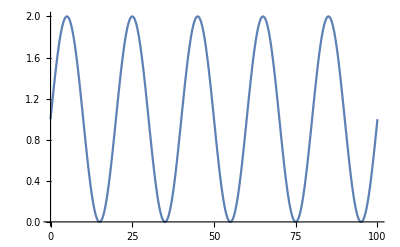

```mathematica
Plot[1+Sin[2*Pi*t/T],{t,0,100}]
```

```mathematica
cyc=FindEcoCycle[condini];
tmin=tmax-T;
cyc=Slice[sol,{tmin,tmax}];
tfin=FinalTime[cyc]
PlotDynamics[cyc,Table[x[i],{i,Intersection[sub,Cv]}],Logged->True,PlotLegends->metabo[[Intersection[sub,Cv]]],AxesLabel->{"time",""}]
```

PlotDynamics[Slice[EcoSim[{x[1]→1,x[2]→1,x[3]→1,x[4]→1,x[5]→1,x[6]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[7]==0,x[i]→0,x[i]→xin[i]],x[8]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[9]==0,x[i]→0,x[i]→xin[i]],x[10]→3,x[11]→1,x[12]→1,x[13]→3,x[14]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[15]==0,x[i]→0,x[i]→xin[i]],x[16]→3,x[17]→3,x[18]→1,x[19]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[20]==0,x[i]→0,x[i]→xin[i]],x[21]→3,x[22]→1,x[23]→1,x[24]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[25]==0,x[i]→0,x[i]→xin[i]],x[26]→1,x[27]→1,x[28]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[29]==0,x[i]→0,x[i]→xin[i]],If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[30]==0,x[i]→0,x[i]→xin[i]],x[31]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[32]==0,x[i]→0,x[i]→xin[i]],x[33]→1,x[34]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[35]==0,x[i]→0,x[i]→xin[i]],x[36]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[37]==0,x[i]→0,x[i]→xin[i]],x[38]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[39]==0,x[i]→0,x[i]→xin[i]],x[40]→1,x[41]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[42]==0,x[i]→0,x[i]→xin[i]],x[43]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[44]==0,x[i]→0,x[i]→xin[i]],x[45]→1,x[46]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[47]==0,x[i]→0,x[i]→xin[i]],x[48]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[49]==0,x[i]→0,x[i]→xin[i]],x[50]→3,x[51]→3,x[52]→3,x[53]→3,x[54]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[55]==0,x[i]→0,x[i]→xin[i]],x[56]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[57]==0,x[i]→0,x[i]→xin[i]],x[58]→1,x[59]→1,x[60]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[61]==0,x[i]→0,x[i]→xin[i]],x[62]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[63]==0,x[i]→0,x[i]→xin[i]],x[64]→3,x[65]→3,x[66]→1,x[67]→1,x[68]→1,x[69]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[70]==0,x[i]→0,x[i]→xin[i]],x[71]→3,x[72]→1,x[73]→0.1},300],{280,300}],{x[1],x[2],x[3],x[13],x[17],x[22],x[26],x[27],x[33],x[34],x[41],x[43],x[50],x[51],x[59],x[60],x[62]},Logged→True,PlotLegends→{13dpg,2pg,3pg,adp,atp,dhap,f6p,fdp,g3p,g6p,h2o,h,nad,nadh,pep,pi,pyr},AxesLabel→{time,}]

```mathematica
Slice[cyc,tmin]
Slice[cyc,tfin]
```

Slice[Slice[EcoSim[{x[1]→1,x[2]→1,x[3]→1,x[4]→1,x[5]→1,x[6]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[7]==0,x[i]→0,x[i]→xin[i]],x[8]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[9]==0,x[i]→0,x[i]→xin[i]],x[10]→3,x[11]→1,x[12]→1,x[13]→3,x[14]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[15]==0,x[i]→0,x[i]→xin[i]],x[16]→3,x[17]→3,x[18]→1,x[19]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[20]==0,x[i]→0,x[i]→xin[i]],x[21]→3,x[22]→1,x[23]→1,x[24]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[25]==0,x[i]→0,x[i]→xin[i]],x[26]→1,x[27]→1,x[28]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[29]==0,x[i]→0,x[i]→xin[i]],If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[30]==0,x[i]→0,x[i]→xin[i]],x[31]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[32]==0,x[i]→0,x[i]→xin[i]],x[33]→1,x[34]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[35]==0,x[i]→0,x[i]→xin[i]],x[36]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[37]==0,x[i]→0,x[i]→xin[i]],x[38]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[39]==0,x[i]→0,x[i]→xin[i]],x[40]→1,x[41]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[42]==0,x[i]→0,x[i]→xin[i]],x[43]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[44]==0,x[i]→0,x[i]→xin[i]],x[45]→1,x[46]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[47]==0,x[i]→0,x[i]→xin[i]],x[48]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[49]==0,x[i]→0,x[i]→xin[i]],x[50]→3,x[51]→3,x[52]→3,x[53]→3,x[54]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[55]==0,x[i]→0,x[i]→xin[i]],x[56]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[57]==0,x[i]→0,x[i]→xin[i]],x[58]→1,x[59]→1,x[60]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[61]==0,x[i]→0,x[i]→xin[i]],x[62]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[63]==0,x[i]→0,x[i]→xin[i]],x[64]→3,x[65]→3,x[66]→1,x[67]→1,x[68]→1,x[69]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[70]==0,x[i]→0,x[i]→xin[i]],x[71]→3,x[72]→1,x[73]→0.1},300],{280,300}],280]

Slice[Slice[EcoSim[{x[1]→1,x[2]→1,x[3]→1,x[4]→1,x[5]→1,x[6]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[7]==0,x[i]→0,x[i]→xin[i]],x[8]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[9]==0,x[i]→0,x[i]→xin[i]],x[10]→3,x[11]→1,x[12]→1,x[13]→3,x[14]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[15]==0,x[i]→0,x[i]→xin[i]],x[16]→3,x[17]→3,x[18]→1,x[19]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[20]==0,x[i]→0,x[i]→xin[i]],x[21]→3,x[22]→1,x[23]→1,x[24]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[25]==0,x[i]→0,x[i]→xin[i]],x[26]→1,x[27]→1,x[28]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[29]==0,x[i]→0,x[i]→xin[i]],If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[30]==0,x[i]→0,x[i]→xin[i]],x[31]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[32]==0,x[i]→0,x[i]→xin[i]],x[33]→1,x[34]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[35]==0,x[i]→0,x[i]→xin[i]],x[36]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[37]==0,x[i]→0,x[i]→xin[i]],x[38]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[39]==0,x[i]→0,x[i]→xin[i]],x[40]→1,x[41]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[42]==0,x[i]→0,x[i]→xin[i]],x[43]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[44]==0,x[i]→0,x[i]→xin[i]],x[45]→1,x[46]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[47]==0,x[i]→0,x[i]→xin[i]],x[48]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[49]==0,x[i]→0,x[i]→xin[i]],x[50]→3,x[51]→3,x[52]→3,x[53]→3,x[54]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[55]==0,x[i]→0,x[i]→xin[i]],x[56]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[57]==0,x[i]→0,x[i]→xin[i]],x[58]→1,x[59]→1,x[60]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[61]==0,x[i]→0,x[i]→xin[i]],x[62]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[63]==0,x[i]→0,x[i]→xin[i]],x[64]→3,x[65]→3,x[66]→1,x[67]→1,x[68]→1,x[69]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[70]==0,x[i]→0,x[i]→xin[i]],x[71]→3,x[72]→1,x[73]→0.1},300],{280,300}],Null]

```mathematica
limreg=Table[lim=Transpose[{subreac2,FindLimMetabo2[system,Slice[cyc,t0]]}];
{t0//N,Position[limcombi,lim][[1,1]]},{t0,tmin,tfin,(tfin-tmin)/100}];
```

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
temp=Transpose[limreg][[2]];
list=Join[{temp[[1]]},temp[[1+Flatten[Position[temp[[1;;-2]]-temp[[2;;-1]],_?(#!=0&)]]]]]
```

{{}⟦1,1⟧}

```mathematica
Table[GraphMetabNetLim[S2,submeta,subreac2,coordsub,limcombi[[kk]],Red,400],{kk,list[[1;;-2]]}]
```

{}

#### Tentative optimization (not reviewed)

```mathematica
(*growth=Table[
μ=Table[1,{k,p}];
μ[[63]]=μ1;
μ[[13]]=μ2;
(*μ[[105]]=1;*)
model={Pop[pop]->Flatten[{Table[Component[x[i]]->{Equation:>0,Color->Colf[i]},{i,{Bv}}],Table[Component[x[i]]->{Equation:>Evaluate[qB*S[[i,subreac2]].Table[vb[j,Table[If[MemberQ[Sv,k],xin[k],If[MemberQ[fxdi,k],fxdval,x[k][t]]],{k,n}],S,α,μ],{j,subreac2}]-If[MemberQ[{},i],0,qB*x[i][t]*S[[Bv,13]]*vb[13,Table[If[MemberQ[Sv,k],xin[k],If[MemberQ[fxdi,k],fxdval,x[k][t]]],{k,n}],S,α,μ]]],Color->Colf[i],Type->"Intensive"},{i,Complement[Cv,fxdi]}]}]};
{label//MatrixForm,model//MatrixForm};
SetModel[model]

tmax=1000;
sol=EcoSim[condini,tmax];
fslice=FinalSlice[sol];
{μ1,μ2,(S[[Bv,13]]*vb[13,Table[If[MemberQ[Sv,k],xin[k],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}],S,α,μ])/.FinalSlice[sol]}
,{μ1,0,.1,.01},{μ2,0.05,.1,.01}]*)
```

```mathematica
(*ListPlot3D[Flatten[growth,1]]*)
```

```mathematica
(*μ=Table[1,{k,p}];
μmax=.02;
npts=40;
μ[[13]]=.15;
growth2=Table[
μ[[63]]=μ1;
model={Pop[pop]->Flatten[{Table[Component[x[i]]->{Equation:>0,Color->Colf[i]},{i,{Bv}}],Table[Component[x[i]]->{Equation:>Evaluate[qB*S[[i,subreac2]].Table[vb[j,Table[If[MemberQ[Sv,k],xin[k],If[MemberQ[fxdi,k],fxdval,x[k][t]]],{k,n}],S,α,μ],{j,subreac2}]-If[MemberQ[{},i],0,qB*x[i][t]*S[[Bv,13]]*vb[13,Table[If[MemberQ[Sv,k],xin[k],If[MemberQ[fxdi,k],fxdval,x[k][t]]],{k,n}],S,α,μ]]],Color->Colf[i],Type->"Intensive"},{i,Complement[Cv,fxdi]}]}]};
{label//MatrixForm,model//MatrixForm};
SetModel[model]

tmax=1000;
sol=EcoSim[condini,tmax];
fslice=FinalSlice[sol];
{μ1,(S[[Bv,13]]*vb[13,Table[If[MemberQ[Sv,k],xin[k],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}],S,α,μ])/.FinalSlice[sol]}
,{μ1,0,μmax,μmax/npts}]
ListPlot[growth2]*)
```

#### Optimized network (not reviewed)

```mathematica
(*tweak the maximal growth rates to optimize growth*)
(*extreme slowdown of PEP to PYR*)
μ=Table[1,{k,p}];
μ[[63]]=0.00001;
μ[[13]]=.15;
(*μ[[105]]=1;*)
SetQSSAModel[system,xin]

tmax=100;
sol=EcoSim[condini,tmax];
fslice=FinalSlice[sol];

(*NEED TO CHANGE S2 FOR GRAD AND LIMITING FACTOR*)
grad=nabg0[Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}]/.FinalSlice[sol],μ];
(S[[Bv,13]]*vb[13,Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}],S,α,μ])/.FinalSlice[sol]

figtraj=PlotDynamics[sol,Table[x[i],{i,Intersection[sub,Cv]}],Logged->True,PlotLegends->metabo[[Intersection[sub,Cv]]],AxesLabel->{"time",""}]
{Join[{{"rate","reaction","code","lim metabo","gradient"}},Sort[Transpose[{(Table[vb[j,Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}],S,α,μ],{j,subreac2}]/.FinalSlice[sol])//N,reacnames2[[subreac2]],subreac2,Table[lst=Flatten[Position[Normal[Transpose[S][[i]]],_?(#<0&)]];
argmin=Ordering[Flatten[{Table[(α[[k,i]]*Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}][[k]]),{k,lst}],gmax}]/.FinalSlice[sol],1];
Flatten[{metabo[[lst]],"max"}][[argmin]],{i,subreac2}],Table[grad[[j]],{j,subreac2}]}]]]//MatrixForm,
Join[{{"concentration","metabolite","index"}},Sort[Table[{If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],metabo[[k]],k},{k,submeta}]/.FinalSlice[sol]]]//MatrixForm}
```

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 3 of … does not exist.

Part::partw: Part 4 of … does not exist.

Part::partw: Part 5 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of … cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in +<<309589136 bytes>> cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

$Aborted

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0.15 Min[0,x[17],x[62]]/.FinalSlice[EcoSim[{x[1]→1,x[2]→1,x[3]→1,x[4]→1,x[5]→1,x[6]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[7]==0,x[i]→0,x[i]→xin[i]],x[8]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[9]==0,x[i]→0,x[i]→xin[i]],x[10]→3,x[11]→1,x[12]→1,x[13]→3,x[14]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[15]==0,x[i]→0,x[i]→xin[i]],x[16]→3,x[17]→3,x[18]→1,x[19]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[20]==0,x[i]→0,x[i]→xin[i]],x[21]→3,x[22]→1,x[23]→1,x[24]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[25]==0,x[i]→0,x[i]→xin[i]],x[26]→1,x[27]→1,x[28]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[29]==0,x[i]→0,x[i]→xin[i]],If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[30]==0,x[i]→0,x[i]→xin[i]],x[31]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[32]==0,x[i]→0,x[i]→xin[i]],x[33]→1,x[34]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[35]==0,x[i]→0,x[i]→xin[i]],x[36]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[37]==0,x[i]→0,x[i]→xin[i]],x[38]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[39]==0,x[i]→0,x[i]→xin[i]],x[40]→1,x[41]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[42]==0,x[i]→0,x[i]→xin[i]],x[43]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[44]==0,x[i]→0,x[i]→xin[i]],x[45]→1,x[46]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[47]==0,x[i]→0,x[i]→xin[i]],x[48]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[49]==0,x[i]→0,x[i]→xin[i]],x[50]→3,x[51]→3,x[52]→3,x[53]→3,x[54]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[55]==0,x[i]→0,x[i]→xin[i]],x[56]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[57]==0,x[i]→0,x[i]→xin[i]],x[58]→1,x[59]→1,x[60]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[61]==0,x[i]→0,x[i]→xin[i]],x[62]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[63]==0,x[i]→0,x[i]→xin[i]],x[64]→3,x[65]→3,x[66]→1,x[67]→1,x[68]→1,x[69]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[70]==0,x[i]→0,x[i]→xin[i]],x[71]→3,x[72]→1,x[73]→0.1},100]]

PlotDynamics[EcoSim[{x[1]→1,x[2]→1,x[3]→1,x[4]→1,x[5]→1,x[6]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[7]==0,x[i]→0,x[i]→xin[i]],x[8]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[9]==0,x[i]→0,x[i]→xin[i]],x[10]→3,x[11]→1,x[12]→1,x[13]→3,x[14]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[15]==0,x[i]→0,x[i]→xin[i]],x[16]→3,x[17]→3,x[18]→1,x[19]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[20]==0,x[i]→0,x[i]→xin[i]],x[21]→3,x[22]→1,x[23]→1,x[24]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[25]==0,x[i]→0,x[i]→xin[i]],x[26]→1,x[27]→1,x[28]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[29]==0,x[i]→0,x[i]→xin[i]],If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[30]==0,x[i]→0,x[i]→xin[i]],x[31]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[32]==0,x[i]→0,x[i]→xin[i]],x[33]→1,x[34]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[35]==0,x[i]→0,x[i]→xin[i]],x[36]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[37]==0,x[i]→0,x[i]→xin[i]],x[38]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[39]==0,x[i]→0,x[i]→xin[i]],x[40]→1,x[41]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[42]==0,x[i]→0,x[i]→xin[i]],x[43]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[44]==0,x[i]→0,x[i]→xin[i]],x[45]→1,x[46]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[47]==0,x[i]→0,x[i]→xin[i]],x[48]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[49]==0,x[i]→0,x[i]→xin[i]],x[50]→3,x[51]→3,x[52]→3,x[53]→3,x[54]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[55]==0,x[i]→0,x[i]→xin[i]],x[56]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[57]==0,x[i]→0,x[i]→xin[i]],x[58]→1,x[59]→1,x[60]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[61]==0,x[i]→0,x[i]→xin[i]],x[62]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[63]==0,x[i]→0,x[i]→xin[i]],x[64]→3,x[65]→3,x[66]→1,x[67]→1,x[68]→1,x[69]→1,If[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}[70]==0,x[i]→0,x[i]→xin[i]],x[71]→3,x[72]→1,x[73]→0.1},100],{x[1],x[2],x[3],x[13],x[17],x[22],x[26],x[27],x[33],x[34],x[41],x[43],x[50],x[51],x[59],x[60],x[62]},Logged→True,PlotLegends→{13dpg,2pg,3pg,adp,atp,dhap,f6p,fdp,g3p,g6p,h2o,h,nad,nadh,pep,pi,pyr},AxesLabel→{time,}]

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FinalSlice[EcoSim[{x[1.]→1.,x[2.]→1.,x[3.]→1.,x[4.]→1.,x[5.]→1.,x[6.]→1.,«39»,x[46.]→1.,If[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,«23»}[47.]==0.,x[i]→0.,x[i]→xin[i]],x[48.]→1.,If[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,«23»}[49.]==0.,x[i]→0.,x[i]→xin[i]],x[50.]→3.,«23»},100.]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Transpose::nmtx: The first two levels of … cannot be transposed.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

{Join[{{rate,reaction,code,lim metabo,gradient}},Transpose[{{0.15 Min[0.,x[17.],x[62.]],Min[5.,x[2.]],Min[5.,x[27.]],Min[0.,x[59.]],Min[5.,x[33.],x[50.],x[60.]],Min[1.,x[59.]],Min[5.,x[17.],x[26.]],Min[5.,x[34.]],1.,0.00001 Min[5.,x[13.],x[43.],x[59.]],Min[5.,x[22.]],Min[5.,x[1.],x[13.]],Min[5.,x[3.]],Min[5.,x[43.],x[60.]]}/.FinalSlice[EcoSim[{x[1.]→1.,x[2.]→1.,x[3.]→1.,x[4.]→1.,66,x[71.]→3.,x[72.]→1.,x[73.]→0.1},100.]],3,{-0.000600233,5.52929×10^-6,0.00004218,0.,6,0.0000207196,0.0000421801,5.52929×10^-6,-4.86296×10^-19}}]],1}
 |  |  |  |

### Linear algebra approach

#### Tools (OLD?! NEW copied from 2R, but modified GraphMetabNetLoop!!)

```mathematica
GraphMetabNetLim[limcb_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},coord_,style_,szvtx_,szim_]:=Graph[verts[submeta,subreac],edges[S,subreac],
VertexLabels->vertlabels[submeta,subreac,metabo,reacnames],
PlotTheme->"IndexLabeled",
VertexStyle->vertstyle[submeta,subreac],VertexSize->{"Scaled",szvtx},
EdgeStyle->Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i->If[j==limcb[[Position[subreac,i][[1,1]],2]],style,Automatic],{j,in}],Table[n+i->j->If[MemberQ[{Bv},j]&&Length[Intersection[Sv,Transpose[limcb][[2]]]]≠0,style,If[MemberQ[Transpose[limcb][[2]],j]&&Not[MemberQ[Sv,j]],style,Automatic]],{j,out}]}]
,{i,subreac}]],
VertexCoordinates->If[ToString[coord]=="Automatic",Automatic,Flatten[{Table[j->coord[[j]],{j,submeta}],Table[(n+i)->coord[[n+i]],{i,subreac}]}]],
VertexShapeFunction->Flatten[{Table[j->Automatic,{j,submeta}],Table[(n+i)->vf1,{i,subreac}]}],ImageSize->szim]

tol=10^(-6);
(*NEW adapted to glycolysis from the toy model (convert indices to submeta)*)
GraphMetabNetLoop[limcb_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_,coord_,style1_,style2_,szvtx_,szim_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,Sacl,reprod,rvaleq,aclmeta,aclreac},
{subS,Lim,P}=PopMatrixSetup[limcb,{S,metabo,reacnames,submeta,subreac,α,μ},xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},{S,metabo,reacnames,submeta,subreac,α,μ}];
(*find the reactions contributing to the autocatalytic loop*)
(*rvaleq=Chop[Transpose[subS].le,tol];*)
rvaleq=Chop[grad,tol];
aclreac=subreac[[Flatten[Position[rvaleq,_?Positive]]]];
(*find the metabolites contributing to the autocatalytic loop*)
reprod=Chop[P.le,tol];
(*complement gets rid of the *)
aclmeta=Complement[submeta[[Flatten[Position[reprod,_?Positive]]]],Sv];
(*manually add the extracell metabo in the loop if: biomass is involved in the autocatalytic loop, and they are limiting a reaction from the autocatalytic loop*)
Sacl=If[MemberQ[aclmeta,Bv],Intersection[Select[limcb,MemberQ[aclreac,#[[1]]]&][[1;;-1,2]],Sv],{}];
aclmeta=Sort[Join[aclmeta,Sacl]];
Graph[verts[submeta,subreac],edges[S,subreac],
VertexLabels->vertlabels[submeta,subreac,metabo,reacnames],
PlotTheme->"IndexLabeled",
VertexStyle->vertstyle[submeta,subreac],VertexSize->{"Scaled",szvtx},
EdgeStyle->Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i->If[MemberQ[aclreac,i]&&MemberQ[aclmeta,j]&&j==limcb[[Position[subreac,i][[1,1]],2]],style1,style2],{j,in}],Table[n+i->j->If[MemberQ[aclreac,i]&&MemberQ[aclmeta,j],style1,style2],{j,out}]}]
,{i,subreac}]],
VertexCoordinates->If[ToString[coord]=="Automatic",Automatic,Flatten[{Table[j->coord[[j]],{j,submeta}],Table[(n+i)->coord[[n+i]],{i,subreac}]}]],
VertexShapeFunction->Flatten[{Table[j->Automatic,{j,submeta}],Table[(n+i)->vf1,{i,subreac}]}],ImageSize->szim]]

ListLim[S_,subreac_]:=Module[{row},
Table[row=Position[Normal[S[[All,subreac[[i]]]]],_?(#<0&)];Table[{subreac[[i]],j[[1]]},{j,row}],{i,Length[subreac]}]]

GenerateLimRegimes[S_,subreac_]:=Module[{combi},
combi=ListLim[S,subreac];
Tuples[combi]]

PopMatrixSetup[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P},
subS=IntegerPart[S[[Join[Intersection[Cv,submeta],{Bv}],subreac]]];
(*Let's make the limitation matrix now*)
Lim=ConstantArray[0,{Length[subreac],Length[submeta]}];
Do[Lim[[Position[subreac,i[[1]]][[1]],Position[submeta,i[[2]]][[1]]]]=μ[[i[[1]]]]*α[[i[[2]],i[[1]]]],{i,limcombi}];
(*now we need to make the matrix that sends all non-internal substrates onto biomass*)
P=ConstantArray[0,{Length[submeta],Length[Join[Intersection[Cv,submeta],{Bv}]]}];
Do[If[MemberQ[Sv,submeta[[i]]],P[[i,-1]]=xin[[submeta[[i]]]],P[[i,Position[Join[Intersection[Cv,submeta],{Bv}],submeta[[i]]][[1]]]]=1],{i,Length[submeta]}];{subS,Lim,P}]

MakePopMatrix[{subS_,Lim_,P_}]:=subS.Lim.P;

LifeCycle[A_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},style_,cordstyle_,szvtx_,szim_]:=Module[{lifecyc,autoloop,edg},
lifecyc=Graph[submeta,Table[Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]],{t,Position[Normal[A],_?(#>0&)]}]];
autoloop=DeleteDuplicates[Flatten[FindCycle[lifecyc,Infinity,All]]];
Graph[submeta,Table[Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]],{t,Position[Normal[A],_?(#>0&)]}],
EdgeStyle->Table[edg=Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]];edg->If[MemberQ[autoloop,edg],style,Automatic],{t,Position[Normal[A],_?(#>0&)]}],
PlotTheme->"IndexLabeled",
VertexCoordinates->cordstyle[[1;;Length[submeta]]],
VertexStyle->Table[j->If[MemberQ[Cv,j],LightGreen,If[MemberQ[Sv,j],LightYellow,LightOrange]],{j,submeta}],
VertexSize->{"Scaled",szvtx},VertexLabels->Table[j->Placed[metabo[[j]],Center],{j,submeta}],ImageSize->szim]]

FindQSS[{subS_,Lim_,P_},{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_}]:=Module[{eig,A,λ,re,le,veq,rvaleq,μeq,grad},
A=MakePopMatrix[{subS,Lim,P}];
eig=Eigensystem[A,1,Method->{"Arnoldi","Criteria"->"RealPart"}]//N;
λ=eig[[1,1]];
re=eig[[2,1,1;;-1]]/eig[[2,1,-1]];
le=Eigensystem[Transpose[A],1,Method->{"Arnoldi","Criteria"->"RealPart"}][[2,1]];
le=Chop[le/(le.re)];
veq=Lim.P.re;
rvaleq=Transpose[subS].le;
μeq=Table[μ[[j]],{j,subreac}];
grad=Table[rvaleq[[j]]*veq[[j]]/μeq[[j]],{j,Length[veq]}];
{λ,re,le,veq,grad}]

(*FindLimMetabo[{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_,P_,re_,le_]:=Module[{metabeq,limsubstr,lst,reac,ix,substr,argmin},
metabeq=Table[{submeta[[k]],metabo[[submeta[[k]]]],If[MemberQ[Sv,submeta[[k]]],xin[[submeta[[k]]]],If[MemberQ[fxdi,submeta[[k]]],fxdval,(P.re)[[k]]]],(P.le)[[k]]},{k,Length[submeta]}];
limsubstr=Table[lst=combi[[i]];reac=lst[[1,1]];substr=Transpose[lst][[2]];ix=Flatten[Table[Position[submeta,j],{j,substr}]];argmin=Ordering[Flatten[{Table[α[[substr[[k]],subreac[[i]]]]*Transpose[metabeq][[3]][[ix[[k]]]],{k,Length[ix]}],gmax}],1];
(*!!n+1 codes for the max rate of a reaction, will need to be added to the list metabo!!*)
Flatten[{substr,n+1}][[argmin[[1]]]],{i,Length[subreac]}];
{metabeq,limsubstr}]*)
FindLimMetabo[{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_,P_,re_,le_]:=Module[{metabeq,limsubstr,lst,reac,ix,substr,argmin},
metabeq=Table[{submeta[[k]],metabo[[submeta[[k]]]],If[MemberQ[Sv,submeta[[k]]],xin[[submeta[[k]]]],If[MemberQ[fxdi,submeta[[k]]],fxdval,(P.re)[[k]]]],If[MemberQ[Sv,submeta[[k]]],"NA",(P.le)[[k]]]},{k,Length[submeta]}];
limsubstr=Table[lst=combi[[i]];reac=lst[[1,1]];substr=Transpose[lst][[2]];ix=Flatten[Table[Position[submeta,j],{j,substr}]];argmin=Ordering[Flatten[{Table[α[[substr[[k]],subreac[[i]]]]*Transpose[metabeq][[3]][[ix[[k]]]],{k,Length[ix]}],gmax}],1];
(*!!n+1 codes for the max rate of a reaction, will need to be added to the list metabo!!*)
Flatten[{substr,n+1}][[argmin[[1]]]],{i,Length[subreac]}];
{metabeq,limsubstr}]

DisplayQSS[{subS_,Lim_,P_},{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{λ,re,le,veq,grad,metabeq,limsubstr},
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},{S,metabo,reacnames,submeta,subreac,α,μ}];
{metabeq,limsubstr}=FindLimMetabo[{S,metabo,reacnames,submeta,subreac,α,μ},xin,P,re,le];
{Join[{{"reaction","code","rate","limiting metabolite","fitness gradient"}},Sort[Transpose[{reacnames[[subreac]],subreac,veq,metabo[[limsubstr]],Chop[grad,tol]}],#1[[3]]<#2[[3]]&]]//MatrixForm,
Join[{{"code","metabolite","concentration","reproductive value"}},Sort[Chop[metabeq,tol],#1[[3]]<#2[[3]]&]]//MatrixForm}]

FindQSSselfc[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,system},
system={S,metabo,reacnames,submeta,subreac,α,μ};
{subS,Lim,P}=PopMatrixSetup[limcombi,system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
If[Element[λ,PositiveReals]&&AllTrue[re,#>0&],If[Transpose[limcombi][[2]]==FindLimMetabo[system,xin,P,re,le][[2]],λ,Undefined],Undefined]]

FindQSSstate[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,system},
system={S,metabo,reacnames,submeta,subreac,α,μ};
{subS,Lim,P}=PopMatrixSetup[limcombi,system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
If[Element[λ,PositiveReals]&&AllTrue[re,#>0&],If[Transpose[limcombi][[2]]==FindLimMetabo[system,xin,P,re,le][[2]],re,Undefined],Undefined]]

FindQSSrates[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,system},
system={S,metabo,reacnames,submeta,subreac,α,μ};
{subS,Lim,P}=PopMatrixSetup[limcombi,system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
If[Element[λ,PositiveReals]&&AllTrue[re,#>0&],If[Transpose[limcombi][[2]]==FindLimMetabo[system,xin,P,re,le][[2]],Lim.P.re,Undefined],Undefined]]
```

#### Tools

```mathematica
arwcf=3*10^(-5);
GraphMetabNetLim[limcb_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},coord_,style_,szvtx_,szim_]:=
Module[{arwsz=szim*arwcf},
Graph[verts[submeta,subreac],edges[S,subreac],
VertexLabels->vertlabels[submeta,subreac,metabo,reacnames],
PlotTheme->"IndexLabeled",
VertexStyle->vertstyle[submeta,subreac],VertexSize->{"Scaled",szvtx},
EdgeStyle->Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i->{If[j==limcb[[Position[subreac,i][[1,1]],2]],style,Automatic],Arrowheads[arwsz]},{j,in}],Table[n+i->j->{If[MemberQ[{Bv},j]&&Length[Intersection[Sv,Transpose[limcb][[2]]]]≠0,style,If[MemberQ[Transpose[limcb][[2]],j]&&Not[MemberQ[Sv,j]],style,Automatic]],Arrowheads[arwsz]},{j,out}]}]
,{i,subreac}]],
VertexCoordinates->If[ToString[coord]=="Automatic",Automatic,Flatten[{Table[j->coord[[j]],{j,submeta}],Table[(n+i)->coord[[n+i]],{i,subreac}]}]],
VertexShapeFunction->Flatten[{Table[j->Automatic,{j,submeta}],Table[(n+i)->vf1,{i,subreac}]}],ImageSize->szim]]

(*GraphMetabNetLoop[limcb_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_,coord_,style1_,style2_,szvtx_,szim_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,Sacl,reprod,rvaleq,aclmeta,aclreac},
{subS,Lim,P}=PopMatrixSetup[limcb,{S,metabo,reacnames,submeta,subreac,α,μ},xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},{S,metabo,reacnames,submeta,subreac,α,μ}];
(*find the reactions contributing to the autocatalytic loop*)
rvaleq=Transpose[subS].le;
aclreac=Flatten[Position[rvaleq,_?Positive]];

(*find the metabolites contributing to the autocatalytic loop*)
reprod=P.le;
reprod[[Sv]]=0;
aclmeta=Flatten[Position[reprod,_?Positive]];
(*manually add the extracell metabo in the loop if: biomass is involved in the autocatalytic loop, and they are limiting a reaction from the autocatalytic loop*)
Sacl=If[MemberQ[aclmeta,Bv],Intersection[Select[limcb,MemberQ[aclreac,#[[1]]]&][[1;;-1,2]],Sv],{}];
aclmeta=Sort[Join[aclmeta,Sacl]];

Graph[verts[submeta,subreac],edges[S,subreac],
VertexLabels->vertlabels[submeta,subreac,metabo,reacnames],
PlotTheme->"IndexLabeled",
VertexStyle->vertstyle[submeta,subreac],VertexSize->{"Scaled",szvtx},
EdgeStyle->Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i->If[MemberQ[aclreac,i]&&MemberQ[aclmeta,j]&&j==limcb[[Position[subreac,i][[1,1]],2]],style1,style2],{j,in}],Table[n+i->j->If[MemberQ[aclreac,i]&&MemberQ[aclmeta,j],style1,style2],{j,out}]}]
,{i,subreac}]],
VertexCoordinates->If[ToString[coord]=="Automatic",Automatic,Flatten[{Table[j->coord[[j]],{j,submeta}],Table[(n+i)->coord[[n+i]],{i,subreac}]}]],
VertexShapeFunction->Flatten[{Table[j->Automatic,{j,submeta}],Table[(n+i)->vf1,{i,subreac}]}],ImageSize->szim]]*)

tol=10^(-6);
arwcf2=0.00008;
(*NEW adapted to glycolysis from the toy model (convert indices to submeta)*)
(*GraphMetabNetLoop[limcb_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_,coord_,style1_,style2_,szvtx_,szim_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,Sacl,reprod,rvaleq,aclmeta,aclreac,arwsz=szim*arwcf2},
{subS,Lim,P}=PopMatrixSetup[limcb,{S,metabo,reacnames,submeta,subreac,α,μ},xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},{S,metabo,reacnames,submeta,subreac,α,μ}];
(*find the reactions contributing to the autocatalytic loop*)
(*rvaleq=Chop[Transpose[subS].le,tol];*)
rvaleq=Chop[grad,tol];
aclreac=subreac[[Flatten[Position[rvaleq,_?Positive]]]];
(*find the metabolites contributing to the autocatalytic loop*)
reprod=Chop[P.le,tol];
(*complement gets rid of the *)
aclmeta=Complement[submeta[[Flatten[Position[reprod,_?Positive]]]],Sv];
(*manually add the extracell metabo in the loop if: biomass is involved in the autocatalytic loop, and they are limiting a reaction from the autocatalytic loop*)
Sacl=If[MemberQ[aclmeta,Bv],Intersection[Select[limcb,MemberQ[aclreac,#[[1]]]&][[1;;-1,2]],Sv],{}];
aclmeta=Sort[Join[aclmeta,Sacl]];
Graph[verts[submeta,subreac],edges[S,subreac],
VertexLabels->vertlabels[submeta,subreac,metabo,reacnames],
PlotTheme->"IndexLabeled",
VertexStyle->vertstyle[submeta,subreac],VertexSize->{"Scaled",szvtx},
EdgeStyle->Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i->{If[MemberQ[aclreac,i]&&MemberQ[aclmeta,j]&&j==limcb[[Position[subreac,i][[1,1]],2]],style1,style2],Arrowheads[arwsz]},{j,in}],Table[n+i->j->{If[MemberQ[aclreac,i]&&MemberQ[aclmeta,j],style1,style2],Arrowheads[arwsz]},{j,out}]}]
,{i,subreac}]],
VertexCoordinates->If[ToString[coord]=="Automatic",Automatic,Flatten[{Table[j->coord[[j]],{j,submeta}],Table[(n+i)->coord[[n+i]],{i,subreac}]}]],
VertexShapeFunction->Flatten[{Table[j->Automatic,{j,submeta}],Table[(n+i)->vf1,{i,subreac}]}],ImageSize->szim]]*)

GraphMetabNetLoop[limcb_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_,coord_,style1_,style2_,style3_,szvtx_,szim_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,Sacl,Sinhib,reprod,rvaleq,aclmeta,aclreac,inhreac,inhmeta,arwsz=szim*arwcf2,arwsz2=szim*arwcf},
{subS,Lim,P}=PopMatrixSetup[limcb,{S,metabo,reacnames,submeta,subreac,α,μ},xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},{S,metabo,reacnames,submeta,subreac,α,μ}];
(*find the reactions contributing to the autocatalytic loop*)
(*rvaleq=Chop[Transpose[subS].le,tol];*)
rvaleq=Chop[grad,tol];
aclreac=subreac[[Flatten[Position[rvaleq,_?Positive]]]];
inhreac=subreac[[Flatten[Position[rvaleq,_?Negative]]]];
(*find the metabolites contributing to the autocatalytic loop*)
reprod=Chop[P.le,tol];
(*complement gets rid of the *)
aclmeta=Complement[submeta[[Flatten[Position[reprod,_?Positive]]]],Sv];
inhmeta=Complement[submeta[[Flatten[Position[reprod,_?Negative]]]],Sv];
(*manually add the extracell metabo in the loop if: biomass is involved in the autocatalytic loop, and they are limiting a reaction from the autocatalytic loop*)
Sacl=If[MemberQ[aclmeta,Bv],Intersection[Select[limcb,MemberQ[aclreac,#[[1]]]&][[1;;-1,2]],Sv],{}];
aclmeta=Sort[Join[aclmeta,Sacl]];
Sinhib=Intersection[Select[limcb,MemberQ[inhreac,#[[1]]]&][[1;;-1,2]],Sv];
inhmeta=Sort[Join[inhmeta,Sinhib]];
Graph[verts[submeta,subreac],edges[S,subreac],
VertexLabels->vertlabels[submeta,subreac,metabo,reacnames],
PlotTheme->"IndexLabeled",
VertexStyle->vertstyle2[submeta,subreac,aclmeta,aclreac,inhmeta,inhreac,style1,style3],VertexSize->{"Scaled",szvtx},
EdgeStyle->Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i->If[MemberQ[aclreac,i]&&MemberQ[aclmeta,j]&&j==limcb[[Position[subreac,i][[1,1]],2]],{style1,Arrowheads[arwsz]},If[MemberQ[inhreac,i]&&(j==limcb[[Position[subreac,i][[1,1]],2]]||MemberQ[aclmeta,j]),{style3,Arrowheads[arwsz]},{style2,Arrowheads[arwsz2]}]],{j,in}],Table[n+i->j->If[MemberQ[aclreac,i]&&MemberQ[aclmeta,j],{style1,Arrowheads[arwsz]},If[MemberQ[inhreac,i]&&MemberQ[inhmeta,j],{style3,Arrowheads[arwsz]},{style2,Arrowheads[arwsz2]}]],{j,out}]}]
,{i,subreac}]],
VertexCoordinates->If[ToString[coord]=="Automatic",Automatic,Flatten[{Table[j->coord[[j]],{j,submeta}],Table[(n+i)->coord[[n+i]],{i,subreac}]}]],
VertexShapeFunction->Flatten[{Table[j->vf1,{j,submeta}],Table[(n+i)->Automatic,{i,subreac}]}],ImageSize->szim]]

vertstyle2[submeta_,subreac_,aclmeta_,aclreac_,inhmeta_,inhreac_,style1_,style3_]:=Flatten[{Table[j->If[MemberQ[Cv,j],If[MemberQ[aclmeta,j],{LightGreen,EdgeForm[style1]},If[MemberQ[inhmeta,j],{LightGreen,EdgeForm[style3]},LightGreen]],If[MemberQ[Sv,j],If[MemberQ[aclmeta,j],{LightYellow,EdgeForm[style1]},If[MemberQ[inhmeta,j],{LightYellow,EdgeForm[style3]},LightYellow]],If[MemberQ[aclmeta,j],{LightOrange,EdgeForm[style1]},LightOrange]]],{j,submeta}],Table[(n+i)->If[MemberQ[aclreac,i],{LightBlue,EdgeForm[style1]},If[MemberQ[inhreac,i],{LightBlue,EdgeForm[style3]},LightBlue]],{i,subreac}]}];

ListLim[S_,subreac_]:=Module[{row},
Table[row=Position[Normal[S[[All,subreac[[i]]]]],_?(#<0&)];Table[{subreac[[i]],j[[1]]},{j,row}],{i,Length[subreac]}]]

GenerateLimRegimes[S_,subreac_]:=Module[{combi},
combi=ListLim[S,subreac];
Tuples[combi]]

PopMatrixSetup[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P},
subS=IntegerPart[S[[Join[Intersection[Cv,submeta],{Bv}],subreac]]];
(*Let's make the limitation matrix now*)
Lim=ConstantArray[0,{Length[subreac],Length[submeta]}];
Do[Lim[[Position[subreac,i[[1]]][[1]],Position[submeta,i[[2]]][[1]]]]=μ[[i[[1]]]]*α[[i[[2]],i[[1]]]],{i,limcombi}];
(*now we need to make the matrix that sends all non-internal substrates onto biomass*)
P=ConstantArray[0,{Length[submeta],Length[Join[Intersection[Cv,submeta],{Bv}]]}];
Do[If[MemberQ[Sv,submeta[[i]]],P[[i,-1]]=xin[[submeta[[i]]]],P[[i,Position[Join[Intersection[Cv,submeta],{Bv}],submeta[[i]]][[1]]]]=1],{i,Length[submeta]}];{subS,Lim,P}]

MakePopMatrix[{subS_,Lim_,P_}]:=subS.Lim.P;

(*LifeCycle[A_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},style_,cordstyle_,szvtx_,szim_]:=Module[{lifecyc,autoloop,edg},
lifecyc=Graph[submeta,Table[Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]],{t,Position[Normal[A],_?(#>0&)]}]];
autoloop=DeleteDuplicates[Flatten[FindCycle[lifecyc,Infinity,All]]];
Graph[submeta,Table[Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]],{t,Position[Normal[A],_?(#>0&)]}],
EdgeStyle->Table[edg=Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]];edg->If[MemberQ[autoloop,edg],style,Automatic],{t,Position[Normal[A],_?(#>0&)]}],
PlotTheme->"IndexLabeled",
VertexCoordinates->cordstyle[[1;;Length[submeta]]],
VertexStyle->Table[j->If[MemberQ[Cv,j],LightGreen,If[MemberQ[Sv,j],LightYellow,LightOrange]],{j,submeta}],
VertexSize->{"Scaled",szvtx},VertexLabels->Table[j->Placed[metabo[[j]],Center],{j,submeta}],ImageSize->szim]]*)

LifeCycle[A_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},style_,cordstyle_,szvtx_,szim_]:=Module[{lifecyc,autoloop,edg,submetab=Complement[submeta,Sv]},
lifecyc=Graph[submeta,Table[Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]],{t,Position[Normal[A],_?(#>0&)]}]];
autoloop=DeleteDuplicates[Flatten[FindCycle[lifecyc,Infinity,All]]];
Graph[submetab,Table[Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]],{t,Position[Normal[A],_?(#>0&)]}],
EdgeStyle->Table[edg=Join[Intersection[Cv,submeta],{Bv}][[t[[2]]]]->Join[Intersection[Cv,submeta],{Bv}][[t[[1]]]];edg->If[MemberQ[autoloop,edg],style,Automatic],{t,Position[Normal[A],_?(#>0&)]}],
PlotTheme->"IndexLabeled",
VertexCoordinates->cordstyle[[1;;Length[submeta]]],
VertexStyle->Table[j->If[MemberQ[Cv,j],LightGreen,If[MemberQ[Sv,j],LightYellow,LightOrange]],{j,submetab}],
VertexSize->{"Scaled",szvtx},VertexLabels->Table[j->Placed[metabo[[j]],Center],{j,submetab}],ImageSize->szim]]

FindQSS[{subS_,Lim_,P_},{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_}]:=Module[{eig,A,λ,re,le,veq,rvaleq,μeq,grad},
A=MakePopMatrix[{subS,Lim,P}];
eig=Eigensystem[A,1,Method->{"Arnoldi","Criteria"->"RealPart"}]//N;
λ=eig[[1,1]];
re=eig[[2,1,1;;-1]]/eig[[2,1,-1]];
le=Eigensystem[Transpose[A],1,Method->{"Arnoldi","Criteria"->"RealPart"}][[2,1]];
le=Chop[le/(le.re)];
veq=Lim.P.re;
rvaleq=Transpose[subS].le;
μeq=Table[μ[[j]],{j,subreac}];
grad=Table[rvaleq[[j]]*veq[[j]]/μeq[[j]],{j,Length[veq]}];
{λ,re,le,veq,grad}]

FindLimMetabo[{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_,P_,re_,le_]:=Module[{metabeq,limsubstr,lst,reac,ix,substr,argmin},
metabeq=Table[{submeta[[k]],metabo[[submeta[[k]]]],If[MemberQ[Sv,submeta[[k]]],xin[[submeta[[k]]]],If[MemberQ[fxdi,submeta[[k]]],fxdval,(P.re)[[k]]]],If[MemberQ[Sv,submeta[[k]]],"NA",(P.le)[[k]]]},{k,Length[submeta]}];
limsubstr=Table[lst=combi[[i]];reac=lst[[1,1]];substr=Transpose[lst][[2]];ix=Flatten[Table[Position[submeta,j],{j,substr}]];argmin=Ordering[Flatten[{Table[α[[substr[[k]],subreac[[i]]]]*Transpose[metabeq][[3]][[ix[[k]]]],{k,Length[ix]}],gmax}],1];
(*!!n+1 codes for the max rate of a reaction, will need to be added to the list metabo!!*)
Flatten[{substr,n+1}][[argmin[[1]]]],{i,Length[subreac]}];
{metabeq,limsubstr}]

DisplayQSS[{subS_,Lim_,P_},{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{λ,re,le,veq,grad,metabeq,limsubstr},
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},{S,metabo,reacnames,submeta,subreac,α,μ}];
{metabeq,limsubstr}=FindLimMetabo[{S,metabo,reacnames,submeta,subreac,α,μ},xin,P,re,le];
metabeq[[1;;-1,4]]=Chop[metabeq[[1;;-1,4]],tol];
{Join[{{"reaction","code","rate","limiting metabolite","fitness gradient"}},Sort[Transpose[{reacnames[[subreac]],subreac,veq,metabo[[limsubstr]],Chop[grad,tol]}],#1[[3]]<#2[[3]]&]]//MatrixForm,
Join[{{"code","metabolite","concentration","reproductive value"}},Sort[metabeq,#1[[3]]<#2[[3]]&]]//MatrixForm}]

FindQSSselfc[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,system},
system={S,metabo,reacnames,submeta,subreac,α,μ};
{subS,Lim,P}=PopMatrixSetup[limcombi,system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
If[Element[λ,PositiveReals]&&AllTrue[re,#>0&],If[Transpose[limcombi][[2]]==FindLimMetabo[system,xin,P,re,le][[2]],λ,Undefined],Undefined]]

CheckSelfc[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,system},
system={S,metabo,reacnames,submeta,subreac,α,μ};
{subS,Lim,P}=PopMatrixSetup[limcombi,system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
If[Element[λ,PositiveReals]&&AllTrue[re,#>0&],If[Transpose[limcombi][[2]]==FindLimMetabo[system,xin,P,re,le][[2]],True,False],False]]

GetQSSλ[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,system},
system={S,metabo,reacnames,submeta,subreac,α,μ};
{subS,Lim,P}=PopMatrixSetup[limcombi,system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
λ]

GetQSSstate[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,system},
system={S,metabo,reacnames,submeta,subreac,α,μ};
{subS,Lim,P}=PopMatrixSetup[limcombi,system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
re]

FindQSSstate[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,system},
system={S,metabo,reacnames,submeta,subreac,α,μ};
{subS,Lim,P}=PopMatrixSetup[limcombi,system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
If[Element[λ,PositiveReals]&&AllTrue[re,#>0&],If[Transpose[limcombi][[2]]==FindLimMetabo[system,xin,P,re,le][[2]],re,Undefined],Undefined]]

FindQSSrates[limcombi_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,system},
system={S,metabo,reacnames,submeta,subreac,α,μ};
{subS,Lim,P}=PopMatrixSetup[limcombi,system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
If[Element[λ,PositiveReals]&&AllTrue[re,#>0&],If[Transpose[limcombi][[2]]==FindLimMetabo[system,xin,P,re,le][[2]],Lim.P.re,Undefined],Undefined]]
```

#### Setup

```mathematica
col1=Darker[Green];
col2=Red;

GraphMetabNet[system,coordsub,vtxsz,imgsz]
(*TOLERANCE FOR CHOPPING FITNESS AND METABOLITE REPROD VALUES*)

μ=Table[1,{k,p}];
(*MAKE PEP TO PYR slower*)
μ[[63]]=.2;

xin=Table[0,{i,n}];
Do[xin[[i]]=1.,{i,essent}];
xin[[35]]=.5;
xin[[44]]=.9;

(*tweak the amount of total metabolites in the conserved pools*)
condini=Table[If[MemberQ[Sv,i],If[xin[[i]]==0,x[i]->0,x[i]->xin[[i]]],If[i==Bv,x[i]->.1,If[MemberQ[Mv,i],x[i]->massbal0,x[i]->1]]],{i,n}];
SetQSSAModel[system,xin]

tmax=1000;
sol=EcoSim[condini,tmax];
fslice=FinalSlice[sol];

grad=nabg0[Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}]/.FinalSlice[sol],μ];
(S[[Bv,GAMi]]*vb[GAMi,Table[If[MemberQ[Sv,k],xin[[k]],If[MemberQ[fxdi,k],fxdval,x[k]]],{k,n}],S2,α,μ])/.FinalSlice[sol]

figtraj=PlotDynamics[sol,Table[x[i],{i,Intersection[sub,Cv]}],Logged->True,PlotLegends->metabo[[Intersection[sub,Cv]]],AxesLabel->{"time",""}]
(*DisplayQSS[{subS,Lim,P},system,xin]*)
```

-Graphics-

NDSolve::dvnoarg: The function x' appears with no arguments.

FilterRules::rep: x'==Equation[x] is not a valid replacement rule.

Join::heads: Heads FilterRules and List at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of … does not exist.

Part::partw: Part 4 of … does not exist.

Part::partw: Part 5 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

FilterRules::rep: x'==Equation[x] is not a valid replacement rule.

Join::heads: Heads FilterRules and List at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FilterRules::rep: x'==Equation[x] is not a valid replacement rule.

Join::heads: Heads FilterRules and List at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FilterRules::rep: x'==Equation[x] is not a valid replacement rule.

General::stop: Further output of FilterRules::rep will be suppressed during this calculation.

Join::heads: Heads FilterRules and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{0,0,0,0,1.,0,0,0,0,0,«4»},{0,-1.,0,0,0,0,0,0,0,0,«4»},{-1.496,0,0,0,0,0,0,0,0,0,«4»},{59.81,0,0,0,0,0,1.,0,0,-1.,«4»},{-59.81,0,0,0,0,0,-1.,0,0,1.,«4»},{0,0,1.,0,0,0,0,0,0,0,«4»},{-0.0709,0,0,1.,0,0,-1.,1.,0,0,«4»},{0,0,-1.,0,0,0,1.,0,0,0,«4»},{-0.129,0,1.,0,-1.,0,0,0,0,0,«4»},{-0.205,0,0,0,0,1.,0,-1.,0,0,«4»},«6»}+{-({x[1],x[2],x[3],x[4],x[5],x[6],0,x[8],0,x[10],«63»}/.FinalSlice[SortRuleList[Join[«2»],{«17»}]])⟦{1,2,3,13,17,22,26,27,33,34,«6»}⟧,0,0,0,0,0,0,0,0,0,«4»} cannot be combined.

Thread::tdlen: Objects of unequal length in {-({x[1],x[2],x[3],x[4],x[5],x[6],0,x[8],0,x[10],«63»}/.FinalSlice[SortRuleList[Join[«2»],{«17»}]])⟦{1,2,3,13,17,22,26,27,33,34,«6»}⟧,0,0,0,0,0,0,0,0,0,«4»}+{{0,0,0,0,1.,0,0,0,0,0,«4»},{0,-1.,0,0,0,0,0,0,0,0,«4»},{-1.496,0,0,0,0,0,0,0,0,0,«4»},{59.81,0,0,0,0,0,1.,0,0,-1.,«4»},{-59.81,0,0,0,0,0,-1.,0,0,1.,«4»},{0,0,1.,0,0,0,0,0,0,0,«4»},{-0.0709,0,0,1.,0,0,-1.,1.,0,0,«4»},{0,0,-1.,0,0,0,1.,0,0,0,«4»},{-0.129,0,1.,0,-1.,0,0,0,0,0,«4»},{-0.205,0,0,0,0,1.,0,-1.,0,0,«4»},«6»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Dot::dotsh: Tensors … and {{Divide[0. + <<1>> + Min[5, <<2>>, ({x[1], x[2], x[3], x[4], x[5], x[6], 0, <<62>>, 0, x[71], x[72], x[73]} /. <<1>>)[[62]]], -<<1>> + <<1>>], <<1>>}, {<<2>>}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

$Aborted

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Min[5,x[17],x[51],x[62]]/.FinalSlice[SortRuleList[Join[FilterRules[{x'==Equation[x],x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,WhenEvent[t==1,x[t]→1],WhenEvent[t==2,x[t]→1],WhenEvent[t==3,x[t]→1],WhenEvent[t==13,x[t]→3],WhenEvent[t==17,x[t]→3],WhenEvent[t==22,x[t]→1],WhenEvent[t==26,x[t]→1],WhenEvent[t==27,x[t]→1],WhenEvent[t==33,x[t]→1],WhenEvent[t==34,x[t]→1],WhenEvent[t==43,x[t]→1],WhenEvent[t==50,x[t]→3],WhenEvent[t==51,x[t]→3],WhenEvent[t==59,x[t]→1],WhenEvent[t==60,x[t]→1],WhenEvent[t==62,x[t]→1],WhenEvent[t==73,x[t]→0.1]},{x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x}],{x[73]→InterpolatingFunction[…],x[1]→InterpolatingFunction[…],x[2]→InterpolatingFunction[…],x[3]→InterpolatingFunction[…],x[13]→InterpolatingFunction[…],x[17]→InterpolatingFunction[…],x[22]→InterpolatingFunction[…],x[26]→InterpolatingFunction[…],x[27]→InterpolatingFunction[…],x[33]→InterpolatingFunction[…],x[34]→InterpolatingFunction[…],x[43]→InterpolatingFunction[…],x[50]→InterpolatingFunction[…],x[51]→InterpolatingFunction[…],x[59]→InterpolatingFunction[…],x[60]→InterpolatingFunction[…],x[62]→InterpolatingFunction[…]}],{x[73],x[1],x[2],x[3],x[13],x[17],x[22],x[26],x[27],x[33],x[34],x[43],x[50],x[51],x[59],x[60],x[62]}]]

PlotDynamics[SortRuleList[Join[FilterRules[{x'==Equation[x],x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,x[0]==0,WhenEvent[t==1,x[t]→1],WhenEvent[t==2,x[t]→1],WhenEvent[t==3,x[t]→1],WhenEvent[t==13,x[t]→3],WhenEvent[t==17,x[t]→3],WhenEvent[t==22,x[t]→1],WhenEvent[t==26,x[t]→1],WhenEvent[t==27,x[t]→1],WhenEvent[t==33,x[t]→1],WhenEvent[t==34,x[t]→1],WhenEvent[t==43,x[t]→1],WhenEvent[t==50,x[t]→3],WhenEvent[t==51,x[t]→3],WhenEvent[t==59,x[t]→1],WhenEvent[t==60,x[t]→1],WhenEvent[t==62,x[t]→1],WhenEvent[t==73,x[t]→0.1]},{x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x}],{x[73]→InterpolatingFunction[…],x[1]→InterpolatingFunction[…],x[2]→InterpolatingFunction[…],x[3]→InterpolatingFunction[…],x[13]→InterpolatingFunction[…],x[17]→InterpolatingFunction[…],x[22]→InterpolatingFunction[…],x[26]→InterpolatingFunction[…],x[27]→InterpolatingFunction[…],x[33]→InterpolatingFunction[…],x[34]→InterpolatingFunction[…],x[43]→InterpolatingFunction[…],x[50]→InterpolatingFunction[…],x[51]→InterpolatingFunction[…],x[59]→InterpolatingFunction[…],x[60]→InterpolatingFunction[…],x[62]→InterpolatingFunction[…]}],{x[73],x[1],x[2],x[3],x[13],x[17],x[22],x[26],x[27],x[33],x[34],x[43],x[50],x[51],x[59],x[60],x[62]}],{x[1],x[2],x[3],x[13],x[17],x[22],x[26],x[27],x[33],x[34],x[43],x[50],x[51],x[59],x[60],x[62]},Logged→True,PlotLegends→{13dpg,2pg,3pg,adp,atp,dhap,f6p,fdp,g3p,g6p,h,nad,nadh,pep,pi,pyr},AxesLabel→{time,}]

#### Generate all limitation regimes

```mathematica
(*summary of all the possible limitation options for each reaction*)
combi=ListLim[S2,subreac2];
(*let us then generate all possible limitation regimes*)
limcombi=GenerateLimRegimes[S2,subreac2];
Length[limcombi]
```

1728

#### Analyze one limitation regime

```mathematica
(*now we want, for each possible limitation combination, to test if they are self-consistent, to eliminate trivial *)
(*Table[If[ToString[FullSimplify[And@@Table[And@@Table[a[limcombi[[kk]][[i,2]]]≤a[combi[[i,j,2]]],{j,Length[combi[[i]]]}] ,{i,Length[limcombi[[kk]]]}]]]==ToString[False],kk,{}],{kk,Length[limcombi]}]*)
(*doesn't seem like there are any contradictions?? To invetigate later...*)

(*let's pick one of these limitation regimes (spoiler alert: it is a self-consistent one)*)
kk=58;
(*let us generate the "Population Matrix" that encodes the life cycle, or auto catalytic loop, of this particular limitation regime*)
{subS,Lim,P}=PopMatrixSetup[limcombi[[kk]],system,xin];
Lim//MatrixForm;
A=MakePopMatrix[{subS,Lim,P}];
A//MatrixForm

(*draw the life cycle of the corresponding "life cycle graph"*)
lifecyc=LifeCycle[A,system,col1,cordstyle,vtxsz,imgsz]
(*find the connected component, useful for visualizing the auto-catalytic cycle*)
ConnectedComponents[lifecyc]
(*find all the different pathways of the auto-catalytic cycle*)
FindCycle[lifecyc,Infinity,All]
```

(-1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1. | 0. | 0. | 0. | 8. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.2 | 0. | 0. | 0.
1. | 0. | 0. | 0. | -2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.2 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 1. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | -0.2 | -1. | 0. | 0.9
0. | 0. | 0. | 0. | 7. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.2 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0.9
0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.2 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

-Graphics-

{{13},{43},{51},{50},{60},{73},{26},{34},{62},{1,2,3,17,22,27,33,59}}

{{1->17,17->27,27->33,33->1},{1->17,17->27,27->22,22->33,33->1},{1->3,3->2,2->59,59->17,17->27,27->33,33->1},{1->3,3->2,2->59,59->17,17->27,27->22,22->33,33->1}}

```mathematica
(*get the QSS to obtain: steady state growth rate, metabolite concentrations, reproductive values, identify the limiting metabolite (before self-consistency)*)
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
GraphMetabNetLim[limcombi[[kk]], system,coordsub,col1,vtxsz,imgsz]
DisplayQSS[{subS,Lim,P},system,xin]
```

-Graphics-

{(reaction | code | rate | limiting metabolite | fitness gradient
FRUpts2 | 25 | 0. | fru[e] | 0
PYK | 63 | 0.00954102 | pep | 0.130145
TPI | 75 | 0.0333269 | dhap | 0.00401696
FBA | 20 | 0.0345185 | fdp | 0.00817754
PFK | 52 | 0.0357526 | atp | 0.120532
μ | 13 | 0.0357526 | atp | -0.116371
PGI | 54 | 0.0460584 | g6p | 0
GLCpts | 30 | 0.0477051 | pep | -0.0251305
ENO | 18 | 0.0589517 | 2pg | 0.00107198
PGM_r | 104 | 0.0610594 | 3pg | 0.00107198
PGK_r | 103 | 0.0632424 | 13dpg | 0.00817754
GAPD | 29 | 0.0655035 | g3p | 0.00817754
PIt2r_r | 105 | 0.805691 | pi | 0
PIt2r | 58 | 0.9 | h[e] | 0),(code | metabolite | concentration | reproductive value
30 | fru[e] | 0 | NA
22 | dhap | 0.0333269 | 3.37128
27 | fdp | 0.0345185 | 6.62619
17 | atp | 0.0357526 | 3.25491
34 | g6p | 0.0460584 | 0
59 | pep | 0.0477051 | 0.52679
2 | 2pg | 0.0589517 | 0.508606
3 | 3pg | 0.0610594 | 0.491049
1 | 13dpg | 0.0632424 | 3.61665
33 | g3p | 0.0655035 | 3.49181
26 | f6p | 0.288253 | 0
35 | glc-D[e] | 0.5 | NA
62 | pyr | 0.601174 | 0
60 | pi | 0.805691 | 0
51 | nadh | 0.832133 | 0
44 | h[e] | 0.9 | NA
73 | N | 1. | 0
61 | pi[e] | 1. | NA
50 | nad | 5.16787 | 0
43 | h | 5.20309 | 0
13 | adp | 5.96425 | 0)}

```mathematica
chemreac[[52]]
```

[c] : atp + f6p --> adp + fdp + h

```mathematica
(*let us look at a particular reaction, the one that creates biomass (GAM)*)
j=13;
kb=Position[subreac2,j][[1,1]];
(*GAM fitness gradient is negative*)
Transpose[subS][[kb]].le
(*why should GAM be downregulated? (negative fitness gradient)*)
Join[{{"metabolite",reacnames2[[subreac2]][[kb]],"reproductive value"}},Transpose[{metabo[[Join[Intersection[Cv,submeta],{Bv}]]],Transpose[subS][[kb]],le}]]//MatrixForm
(*basically, biomass is not limiting in this autocatalytic cycle (the loop is internal, no demographic coupling) so that biomass creation is only a resource sink (ATP here)*)
```

-3.25491

(metabolite | μ | reproductive value
13dpg | 0 | 3.61665
2pg | 0 | 0.508606
3pg | 0 | 0.491049
adp | 7 | 0
atp | -1 | 3.25491
dhap | 0 | 3.37128
f6p | 0 | 0
fdp | 0 | 6.62619
g3p | 0 | 3.49181
g6p | 0 | 0
h | 0 | 0
nad | 7 | 0
nadh | -1 | 0
pep | 0 | 0.52679
pi | 0 | 0
pyr | -1 | 0
biomass | 1 | 0)

```mathematica
GraphMetabNet[system,coordsub,vtxsz,imgsz]
```

-Graphics-

#### All possible autocatalytic loops?

```mathematica
vtxsz2=vtxsz*1;
imgsz2=400;
(*problem is probably that these regimes can't be separated from some actual set of parameters for which they are valid*)
(*Length[limcombi]*)
DeleteDuplicates[Table[GraphMetabNetLoop[limcombi[[kk]],system,xin,coordsub,{col1,Thickness[0.000015*imgsz2]},Automatic,{col2,Thickness[0.000015*imgsz2]},vtxsz2,imgsz2],{kk,100}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Select self-consistent regimes only

```mathematica
(*function testing for self-consistency*)
kk=58;
{subS,Lim,P}=PopMatrixSetup[limcombi[[kk]],system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system]
(*gives an answer, thus confirming this is self-consistent*)
FindQSSselfc[limcombi[[kk]],system,xin]
```

{0.0357526,{0.0632424,0.0589517,0.0610594,5.96425,0.0357526,0.0333269,0.288253,0.0345185,0.0655035,0.0460584,5.20309,5.16787,0.832133,0.0477051,0.805691,0.601174,1.},{3.61665,0.508606,0.491049,0,3.25491,3.37128,0,6.62619,3.49181,0,0,0,0,0.52679,0,0,0},{0.0357526,0.0589517,0.0345185,0.,0.0655035,0.0477051,0.0357526,0.0460584,0.9,0.00954102,0.0333269,0.0632424,0.0610594,0.805691},{-0.116371,0.00107198,0.00817754,0.,0.00817754,-0.0251305,0.120532,0.,0.,0.130145,0.00401696,0.00817754,0.00107198,0.}}

0.0357526

```mathematica
(*Let's go through all combinations and keep the self consistent ones*)
AbsoluteTiming[altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]]]
```

{1.94612,{{58,0.0357526}}}

```mathematica
(*not faster anymore, check if positive and real first: speeds up*)
(*old method twice as fast??? Investigate?*)
(*Timing[
vcb=Quiet[DeleteCases[Table[
{λ,re,le,veq,grad}=FindQSS[PopMatrixSetup[limcombi[[kk]],system,xin]];
If[Element[λ,PositiveReals]&&AllTrue[re,#>0&],{kk,{λ,re}},{}],{kk,1,Length[limcombi]}],{}]];
altss=DeleteCases[Table[kk=vcb[[kkk,1]];
a=ConstantArray[0,n];
Do[a[[Intersection[Cv,submeta][[i]]]]=vcb[[kkk,2,2,i]],{i,Length[Intersection[Cv,submeta]]}];
Do[a[[Intersection[Sv,submeta][[i]]]]=xin[Intersection[Sv,submeta][[i]]],{i,Length[Intersection[Sv,submeta]]}];
If[FullSimplify[And@@Table[And@@Table[a[[limcombi[[kk]][[i,2]]]]≤a[[combi[[i,j,2]]]],{j,Length[combi[[i]]]}] ,{i,Length[limcombi[[kk]]]}]],vcb[[kkk]],{}]
,{kkk,Length[vcb]}],{}]]*)
```

```mathematica
(*GraphMetabNetLoop[limcb_,{S_,metabo_,reacnames_,submeta_,subreac_,α_,μ_},xin_,coord_,style1_,style2_,style3_,szvtx_,szim_]:=Module[{subS,Lim,P,λ,re,le,veq,grad,Sacl,Sinhib,reprod,rvaleq,aclmeta,aclreac,inhreac,inhmeta,arwsz=szim*arwcf2,arwsz2=szim*arwcf},
{subS,Lim,P}=PopMatrixSetup[limcb,{S,metabo,reacnames,submeta,subreac,α,μ},xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},{S,metabo,reacnames,submeta,subreac,α,μ}];
(*find the reactions contributing to the autocatalytic loop*)
(*rvaleq=Chop[Transpose[subS].le,tol];*)
rvaleq=Chop[grad,tol];
aclreac=subreac[[Flatten[Position[rvaleq,_?Positive]]]];
inhreac=subreac[[Flatten[Position[rvaleq,_?Negative]]]];
(*find the metabolites contributing to the autocatalytic loop*)
reprod=Chop[P.le,tol];
(*complement gets rid of the *)
aclmeta=Complement[submeta[[Flatten[Position[reprod,_?Positive]]]],Sv];
inhmeta=Complement[submeta[[Flatten[Position[reprod,_?Negative]]]],Sv];
(*manually add the extracell metabo in the loop if: biomass is involved in the autocatalytic loop, and they are limiting a reaction from the autocatalytic loop*)
Sacl=If[MemberQ[aclmeta,Bv],Intersection[Select[limcb,MemberQ[aclreac,#[[1]]]&][[1;;-1,2]],Sv],{}];
aclmeta=Sort[Join[aclmeta,Sacl]];
Sinhib=Intersection[Select[limcb,MemberQ[inhreac,#[[1]]]&][[1;;-1,2]],Sv];
inhmeta=Sort[Join[inhmeta,Sinhib]];
Graph[verts[submeta,subreac],edges[S,subreac],
VertexLabels->vertlabels[submeta,subreac,metabo,reacnames],
PlotTheme->"IndexLabeled",
VertexStyle->vertstyle2[submeta,subreac,aclmeta,aclreac,inhmeta,inhreac,style1,style3],VertexSize->{"Scaled",szvtx},
EdgeStyle->Flatten[Table[
in=Flatten[Position[Transpose[Normal[S]][[i]],_?(#<0&)]];
out=Flatten[Position[Transpose[Normal[S]][[i]],_?(#>0&)]];
Flatten[{Table[j->n+i->If[MemberQ[aclreac,i]&&MemberQ[aclmeta,j]&&j==limcb[[Position[subreac,i][[1,1]],2]],{style1,Arrowheads[arwsz]},If[MemberQ[inhreac,i]&&(j==limcb[[Position[subreac,i][[1,1]],2]]||MemberQ[aclmeta,j]),{style3,Arrowheads[arwsz]},{style2,Arrowheads[arwsz2]}]],{j,in}],Table[n+i->j->If[MemberQ[aclreac,i]&&MemberQ[aclmeta,j],{style1,Arrowheads[arwsz]},If[MemberQ[inhreac,i]&&MemberQ[inhmeta,j],{style3,Arrowheads[arwsz]},{style2,Arrowheads[arwsz2]}]],{j,out}]}]
,{i,subreac}]],
VertexCoordinates->If[ToString[coord]=="Automatic",Automatic,Flatten[{Table[j->coord[[j]],{j,submeta}],Table[(n+i)->coord[[n+i]],{i,subreac}]}]],
VertexShapeFunction->Flatten[{Table[j->vf1,{j,submeta}],Table[(n+i)->Automatic,{i,subreac}]}],ImageSize->szim]]*)
```

```mathematica
vtxsz2=vtxsz*1.3;
imgsz2=400;
DeleteDuplicates[Table[LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[kk]],system,xin]],system,col1,vtxsz2,imgsz2],{kk,Transpose[altss][[1]]}]];
DeleteDuplicates[Table[{Show[GraphMetabNetLoop[limcombi[[kk]],system,xin,coordsub,{col1,Thickness[0.000015*imgsz2]},Automatic,{col2,Thickness[0.000015*imgsz2]},vtxsz2,imgsz2]],LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[kk]],system,xin]],system,{col1,Thickness[0.000015*imgsz2]},cordstyle,vtxsz2,imgsz2],DisplayQSS[{subS,Lim,P},system,xin]},{kk,Transpose[altss][[1]]}]]
```

{{-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
FRUpts2 | 25 | 0. | fru[e] | 0
PYK | 63 | 0.00954102 | pep | 0.130145
TPI | 75 | 0.0333269 | dhap | 0.00401696
FBA | 20 | 0.0345185 | fdp | 0.00817754
PFK | 52 | 0.0357526 | atp | 0.120532
μ | 13 | 0.0357526 | atp | -0.116371
PGI | 54 | 0.0460584 | g6p | 0
GLCpts | 30 | 0.0477051 | pep | -0.0251305
ENO | 18 | 0.0589517 | 2pg | 0.00107198
PGM_r | 104 | 0.0610594 | 3pg | 0.00107198
PGK_r | 103 | 0.0632424 | 13dpg | 0.00817754
GAPD | 29 | 0.0655035 | g3p | 0.00817754
PIt2r_r | 105 | 0.805691 | pi | 0
PIt2r | 58 | 0.9 | h[e] | 0),(code | metabolite | concentration | reproductive value
30 | fru[e] | 0 | NA
22 | dhap | 0.0333269 | 3.37128
27 | fdp | 0.0345185 | 6.62619
17 | atp | 0.0357526 | 3.25491
34 | g6p | 0.0460584 | 0
59 | pep | 0.0477051 | 0.52679
2 | 2pg | 0.0589517 | 0.508606
3 | 3pg | 0.0610594 | 0.491049
1 | 13dpg | 0.0632424 | 3.61665
33 | g3p | 0.0655035 | 3.49181
26 | f6p | 0.288253 | 0
35 | glc-D[e] | 0.5 | NA
62 | pyr | 0.601174 | 0
60 | pi | 0.805691 | 0
51 | nadh | 0.832133 | 0
44 | h[e] | 0.9 | NA
73 | N | 1. | 0
61 | pi[e] | 1. | NA
50 | nad | 5.16787 | 0
43 | h | 5.20309 | 0
13 | adp | 5.96425 | 0)}}}

### Let’s explore possible limitation regimes along gradients in glucose and Pi

```mathematica
iR1=35;
iR2=61;
```

#### Generate all limitation regimes

```mathematica
(*summary of all the possible limitation options for each reaction*)
combi=ListLim[S2,subreac2];
(*let us then generate all possible limitation regimes*)
limcombi=GenerateLimRegimes[S2,subreac2];
Length[limcombi]
```

1728

#### Along gradient in glucose

```mathematica
(*Exploratory phase:find all relevant limitation regimes along gradients*)
AbsoluteTiming[gllim=Table[xin[[iR1]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.02,.1,.002]}]]
```

{109.708,{{0.02,{34},{0.0263852}},{0.022,{34},{0.0281885}},{0.024,{34},{0.0299046}},{0.026,{34},{0.0315417}},{0.028,{34},{0.0331066}},{0.03,{34},{0.0346056}},{0.032,{34},{0.0360439}},{0.034,{34},{0.0374263}},{0.036,{34},{0.0387567}},{0.038,{34},{0.0400391}},{0.04,{34},{0.0412765}},{0.042,{34},{0.0424721}},{0.044,{34},{0.0436284}},{0.046,{34},{0.0447479}},{0.048,{34,58},{0.0458328,0.0357526}},{0.05,{34,58},{0.0468852,0.0357526}},{0.052,{34,58},{0.0479067,0.0357526}},{0.054,{58},{0.0357526}},{0.056,{58},{0.0357526}},{0.058,{58},{0.0357526}},{0.06,{58},{0.0357526}},{0.062,{58},{0.0357526}},{0.064,{58},{0.0357526}},{0.066,{58},{0.0357526}},{0.068,{58},{0.0357526}},{0.07,{58},{0.0357526}},{0.072,{58},{0.0357526}},{0.074,{58},{0.0357526}},{0.076,{58},{0.0357526}},{0.078,{58},{0.0357526}},{0.08,{58},{0.0357526}},{0.082,{58},{0.0357526}},{0.084,{58},{0.0357526}},{0.086,{58},{0.0357526}},{0.088,{58},{0.0357526}},{0.09,{58},{0.0357526}},{0.092,{58},{0.0357526}},{0.094,{58},{0.0357526}},{0.096,{58},{0.0357526}},{0.098,{58},{0.0357526}},{0.1,{58},{0.0357526}}}}

{34,58}

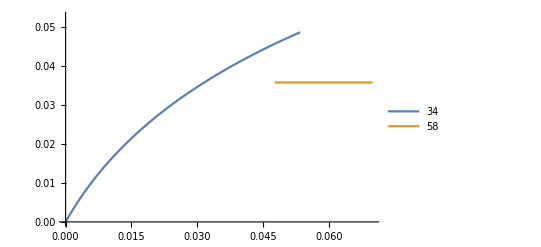

```mathematica
(*summary of all the limitation regimes encountered*)
lrlst=Sort[DeleteDuplicates[Flatten[gllim[[All,2]]]]]
ymax=1.1*Max[Flatten[gllim[[All,3]]]];
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]];
Quiet[Show[Table[Plot[FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x}]],{x,0,.07},PlotStyle->collr[[kk]],PlotRange->{All,{0,ymax}},PlotPoints->50,MaxRecursion->3,PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]]
```

```mathematica
vertstyle2[submeta_,subreac_,aclmeta_,aclreac_,inhmeta_,inhreac_,style1_,style3_]:=Flatten[{Table[j->If[MemberQ[Cv,j],If[MemberQ[aclmeta,j],{LightGreen,EdgeForm[style1]},If[MemberQ[inhmeta,j],{LightGreen,EdgeForm[style3]},LightGreen]],If[MemberQ[Sv,j],If[MemberQ[aclmeta,j],{LightYellow,EdgeForm[style1]},If[MemberQ[inhmeta,j],{LightYellow,EdgeForm[style3]},LightYellow]],If[MemberQ[aclmeta,j],{LightOrange,EdgeForm[style1]},LightOrange]]],{j,submeta}],Table[(n+i)->If[MemberQ[aclreac,i],{LightBlue,EdgeForm[style1]},If[MemberQ[inhreac,i],{LightBlue,EdgeForm[style3]},LightBlue]],{i,subreac}]}];
```

```mathematica
(*computing average coordinates for the point identified, to get a "representative" supply to look at the network*)
avcoord=Table[listi=Position[gllim[[All,2]],j][[1;;-1,1]];Mean[gllim[[listi]][[1;;-1,1]]],{j,lrlst}]

Table[xin[[iR1]]=avcoord[[j]];
{avcoord[[j]],lrlst[[j]],Show[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{col1,Thickness[.008]},Automatic,{col2,Thickness[.008]},vtxsz2,imgsz2]],LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin]],system,{col1,Thickness[.008]},cordstyle,vtxsz2,imgsz2],DisplayQSS[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin],system,xin]},{j,Length[lrlst]}]
```

{0.036,0.074}

{{0.036,34,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
FRUpts2 | 25 | 0. | fru[e] | 0
PYK | 63 | 0.0151994 | pep | 0.00720248
TPI | 75 | 0.0309205 | dhap | 0.00110884
FBA | 20 | 0.0321189 | fdp | 0.00226066
PFK | 52 | 0.0333637 | f6p | 0.00153388
PGI | 54 | 0.0346568 | g6p | 0.00153388
GLCpts | 30 | 0.036 | glc-D[e] | 0.0235047
μ | 13 | 0.0387567 | atp | 0.000876976
ENO | 18 | 0.0541448 | 2pg | 0.000988002
PGM_r | 104 | 0.0562433 | 3pg | 0.000988002
PGK_r | 103 | 0.0584231 | 13dpg | 0.00226066
GAPD | 29 | 0.0606874 | g3p | 0.00226066
PIt2r_r | 105 | 0.807997 | pi | 0
PIt2r | 58 | 0.9 | h[e] | 0),(code | metabolite | concentration | reproductive value
30 | fru[e] | 0 | NA
22 | dhap | 0.0309205 | 0.925285
27 | fdp | 0.0321189 | 1.81605
26 | f6p | 0.0333637 | 1.18623
34 | g6p | 0.0346568 | 1.14197
35 | glc-D[e] | 0.036 | NA
17 | atp | 0.0387567 | 0.583839
2 | 2pg | 0.0541448 | 0.470819
3 | 3pg | 0.0562433 | 0.453252
1 | 13dpg | 0.0584231 | 0.998397
33 | g3p | 0.0606874 | 0.961146
59 | pep | 0.0759972 | 0.489066
62 | pyr | 0.321046 | 0
51 | nadh | 0.565855 | 0
60 | pi | 0.807997 | 0
44 | h[e] | 0.9 | NA
73 | N | 1. | 0.606467
61 | pi[e] | 1. | NA
43 | h | 4.40838 | 0
50 | nad | 5.43415 | 0
13 | adp | 5.96124 | 0)}},{0.074,58,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
FRUpts2 | 25 | 0. | fru[e] | 0
PYK | 63 | 0.00954102 | pep | 0.130145
TPI | 75 | 0.0333269 | dhap | 0.00401696
FBA | 20 | 0.0345185 | fdp | 0.00817754
PFK | 52 | 0.0357526 | atp | 0.120532
μ | 13 | 0.0357526 | atp | -0.116371
PGI | 54 | 0.0460584 | g6p | 0
GLCpts | 30 | 0.0477051 | pep | -0.0251305
ENO | 18 | 0.0589517 | 2pg | 0.00107198
PGM_r | 104 | 0.0610594 | 3pg | 0.00107198
PGK_r | 103 | 0.0632424 | 13dpg | 0.00817754
GAPD | 29 | 0.0655035 | g3p | 0.00817754
PIt2r_r | 105 | 0.805691 | pi | 0
PIt2r | 58 | 0.9 | h[e] | 0),(code | metabolite | concentration | reproductive value
30 | fru[e] | 0 | NA
22 | dhap | 0.0333269 | 3.37128
27 | fdp | 0.0345185 | 6.62619
17 | atp | 0.0357526 | 3.25491
34 | g6p | 0.0460584 | 0
59 | pep | 0.0477051 | 0.52679
2 | 2pg | 0.0589517 | 0.508606
3 | 3pg | 0.0610594 | 0.491049
1 | 13dpg | 0.0632424 | 3.61665
33 | g3p | 0.0655035 | 3.49181
35 | glc-D[e] | 0.074 | NA
26 | f6p | 0.288253 | 0
62 | pyr | 0.601174 | 0
60 | pi | 0.805691 | 0
51 | nadh | 0.832133 | 0
44 | h[e] | 0.9 | NA
73 | N | 1. | 0
61 | pi[e] | 1. | NA
50 | nad | 5.16787 | 0
43 | h | 5.20309 | 0
13 | adp | 5.96425 | 0)}}}

#### Debug Autocatalytic loop graph

```mathematica
k=1;
{subS,Lim,P}=PopMatrixSetup[limcombi[[k]],system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
le
metabo
reprod=P.le
subSv=Intersection[submeta,Sv];
reprod[[Flatten[Table[Position[submeta,i],{i,subSv}]]]]=0.;
reprod
aclmeta=Flatten[Position[reprod,_?Positive]];
Sacl=If[MemberQ[submeta[[aclmeta]],Bv],Intersection[Select[limcombi[[k]],MemberQ[aclreac,#[[1]]]&][[1;;-1,2]],Intersection[submeta,Sv]],{}]
```

{0.195789,0,0,0.113133,0.412561,0.0837106,0,0.138447,0.128022,0,0,0,0,0,0,0,0,0}

{13dpg,2pg,3pg,6pgc,6pgl,ac,ac[e],acald,acald[e],accoa,acon-C,actp,adp,akg,akg[e],amp,atp,cit,co2,co2[e],coa,dhap,e4p,etoh,etoh[e],f6p,fdp,for,for[e],fru[e],fum,fum[e],g3p,g6p,glc-D[e],gln-L,gln-L[e],glu-L,glu-L[e],glx,h2o,h2o[e],h,h[e],icit,lac-D,lac-D[e],mal-L,mal-L[e],nad,nadh,nadp,nadph,nh4,nh4[e],o2,o2[e],oaa,pep,pi,pi[e],pyr,pyr[e],q8,q8h2,r5p,ru5p-D,s7p,succ,succ[e],succoa,xu5p-D,biomass}

{0.195789,0.,0.,0.113133,0.412561,0.0837106,0.,0.138447,0.,0.128022,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.195789,0.,0.,0.113133,0.412561,0.0837106,0.,0.138447,0.,0.128022,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{}

```mathematica
submeta[[aclmeta]]
```

{1,13,17,22,27,33}

```mathematica
Sv
```

{7,9,15,20,25,29,30,32,35,37,39,42,44,47,49,55,57,61,63,70}

```mathematica
k=1;
{subS,Lim,P}=PopMatrixSetup[limcombi[[k]],system,xin];
{λ,re,le,veq,grad}=FindQSS[{subS,Lim,P},system];
le
metabo
rvaleq=Transpose[subS].le;
aclreac=subreac2[[Flatten[Position[rvaleq,_?Positive]]]]

(*find the metabolites contributing to the autocatalytic loop*)
reprod=P.le;
(*complement gets rid of the *)
aclmeta=Complement[submeta[[Flatten[Position[reprod,_?Positive]]]],Sv]
```

{0.195789,0,0,0.113133,0.412561,0.0837106,0,0.138447,0.128022,0,0,0,0,0,0,0,0,0}

{13dpg,2pg,3pg,6pgc,6pgl,ac,ac[e],acald,acald[e],accoa,acon-C,actp,adp,akg,akg[e],amp,atp,cit,co2,co2[e],coa,dhap,e4p,etoh,etoh[e],f6p,fdp,for,for[e],fru[e],fum,fum[e],g3p,g6p,glc-D[e],gln-L,gln-L[e],glu-L,glu-L[e],glx,h2o,h2o[e],h,h[e],icit,lac-D,lac-D[e],mal-L,mal-L[e],nad,nadh,nadp,nadph,nh4,nh4[e],o2,o2[e],oaa,pep,pi,pi[e],pyr,pyr[e],q8,q8h2,r5p,ru5p-D,s7p,succ,succ[e],succoa,xu5p-D,biomass}

{13,20,29,63,75,103}

{1,13,17,22,27,33}

```mathematica
Sv
submeta
```

{7,9,15,20,25,29,30,32,35,37,39,42,44,47,49,55,57,61,63,70}

{1,2,3,13,17,22,26,27,30,33,34,35,41,43,44,50,51,59,60,61,62,73}

```mathematica
GraphMetabNetLoop[limcombi[[lrlst[[1]]]],system,xin,coordsub,{Red,Thickness[.008]},Opacity[0],vtxsz2,imgsz2]
```

-Graphics-

#### Along a gradient in Phosphorus

```mathematica
xin[[iR1]]=.05;
AbsoluteTiming[pilim=Table[xin[[iR2]]=Spi;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Spi,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Spi,Range[0.02,.2,.005]}]]
```

{109.876,{{0.02,{262},{0.00575345}},{0.025,{262},{0.00716759}},{0.03,{262},{0.00857237}},{0.035,{262},{0.00996795}},{0.04,{262},{0.0113545}},{0.045,{262},{0.0127322}},{0.05,{262},{0.0141011}},{0.055,{262},{0.0154614}},{0.06,{262},{0.0168133}},{0.065,{262},{0.0181568}},{0.07,{262},{0.0194922}},{0.075,{262},{0.0208195}},{0.08,{262},{0.0221388}},{0.085,{262},{0.0234504}},{0.09,{262},{0.0247542}},{0.095,{262},{0.0260505}},{0.1,{262},{0.0273393}},{0.105,{262},{0.0286208}},{0.11,{262},{0.0298951}},{0.115,{262},{0.0311621}},{0.12,{262},{0.0324222}},{0.125,{262},{0.0336753}},{0.13,{262},{0.0349216}},{0.135,{70},{0.0357526}},{0.14,{70},{0.0357526}},{0.145,{70},{0.0357526}},{0.15,{70,214},{0.0357526,0.0407884}},{0.155,{70,214},{0.0357526,0.0424963}},{0.16,{70,214},{0.0357526,0.0441821}},{0.165,{70,238},{0.0357526,0.0459441}},{0.17,{46,70},{0.0468852,0.0357526}},{0.175,{46,70},{0.0468852,0.0357526}},{0.18,{46,70},{0.0468852,0.0357526}},{0.185,{46,70},{0.0468852,0.0357526}},{0.19,{46,70},{0.0468852,0.0357526}},{0.195,{46,70},{0.0468852,0.0357526}},{0.2,{46,70},{0.0468852,0.0357526}}}}

{46,70,214,238,262}

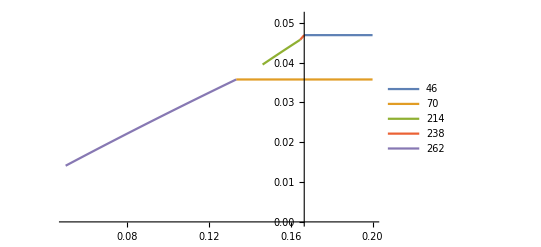

```mathematica
(*spilim//MatrixForm
Show[ListPlot[spilim[[1;;-1,3,1]]],ListPlot[spilim[[1;;-1,3,-1]]]]*)
lrlst=Sort[DeleteDuplicates[Flatten[pilim[[All,2]]]]]
ymax=1.1*Max[Flatten[pilim[[All,3]]]];
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]];
Quiet[Show[Table[Plot[FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR2->x}]],{x,0.05,.2},PlotStyle->collr[[kk]],PlotRange->{All,{0,ymax}},PlotPoints->50,MaxRecursion->3,PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]]
```

```mathematica
(*computing average coordinates for the point identified, to get a "representative" supply to look at the network*)
avcoord=Table[listi=Position[pilim[[All,2]],j][[1;;-1,1]];Mean[pilim[[listi]][[1;;-1,1]]],{j,lrlst}];

Table[xin[[iR2]]=avcoord[[j]];
{avcoord[[j]],lrlst[[j]],Show[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{col1,Thickness[.008]},Automatic,{col2,Thickness[.008]},vtxsz2,imgsz2]],LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin]],system,{col1,Thickness[.008]},cordstyle,vtxsz2,imgsz2],DisplayQSS[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin],system,xin]},{j,Length[lrlst]}]
```

{{0.185,46,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
FRUpts2 | 25 | 0. | fru[e] | 0
PYK | 63 | 0.0169607 | pep | 0.0085032
TPI | 75 | 0.0416269 | dhap | 0.00156199
FBA | 20 | 0.0435786 | fdp | 0.00319722
PFK | 52 | 0.0456217 | f6p | 0.00211843
μ | 13 | 0.0468852 | atp | 0.00116064
PGI | 54 | 0.0477607 | g6p | 0.00211843
GLCpts | 30 | 0.05 | glc-D[e] | 0.0259157
ENO | 18 | 0.0709367 | 2pg | 0.00135885
PGM_r | 104 | 0.0742626 | 3pg | 0.00135885
PGK_r | 103 | 0.0777444 | 13dpg | 0.00319722
GAPD | 29 | 0.0813895 | g3p | 0.00319722
PIt2r_r | 105 | 0.0989703 | pi | 0
PIt2r | 58 | 0.185 | pi[e] | 0),(code | metabolite | concentration | reproductive value
30 | fru[e] | 0 | NA
22 | dhap | 0.0416269 | 0.800331
27 | fdp | 0.0435786 | 1.56482
26 | f6p | 0.0456217 | 0.990392
17 | atp | 0.0468852 | 0.527993
34 | g6p | 0.0477607 | 0.946037
35 | glc-D[e] | 0.05 | NA
2 | 2pg | 0.0709367 | 0.408568
3 | 3pg | 0.0742626 | 0.39027
1 | 13dpg | 0.0777444 | 0.877138
33 | g3p | 0.0813895 | 0.837855
59 | pep | 0.0848035 | 0.427723
60 | pi | 0.0989703 | 0
61 | pi[e] | 0.185 | NA
62 | pyr | 0.428186 | 0
51 | nadh | 0.735933 | 0
44 | h[e] | 0.9 | NA
73 | N | 1. | 0.552748
43 | h | 4.18214 | 0
50 | nad | 5.26407 | 0
13 | adp | 5.95311 | 0)}},{0.1675,70,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
FRUpts2 | 25 | 0. | fru[e] | 0
PYK | 63 | 0.00954102 | pep | 0.130145
TPI | 75 | 0.0333269 | dhap | 0.00401696
FBA | 20 | 0.0345185 | fdp | 0.00817754
PFK | 52 | 0.0357526 | atp | 0.120532
μ | 13 | 0.0357526 | atp | -0.116371
PGI | 54 | 0.0460584 | g6p | 0
GLCpts | 30 | 0.0477051 | pep | -0.0251305
ENO | 18 | 0.0589517 | 2pg | 0.00107198
PGM_r | 104 | 0.0610594 | 3pg | 0.00107198
PGK_r | 103 | 0.0632424 | 13dpg | 0.00817754
GAPD | 29 | 0.0655035 | g3p | 0.00817754
PIt2r_r | 105 | 0.0984758 | pi | 0
PIt2r | 58 | 0.1675 | pi[e] | 0),(code | metabolite | concentration | reproductive value
30 | fru[e] | 0 | NA
22 | dhap | 0.0333269 | 3.37128
27 | fdp | 0.0345185 | 6.62619
17 | atp | 0.0357526 | 3.25491
34 | g6p | 0.0460584 | 0
59 | pep | 0.0477051 | 0.52679
35 | glc-D[e] | 0.05 | NA
2 | 2pg | 0.0589517 | 0.508606
3 | 3pg | 0.0610594 | 0.491049
1 | 13dpg | 0.0632424 | 3.61665
33 | g3p | 0.0655035 | 3.49181
60 | pi | 0.0984758 | 0
61 | pi[e] | 0.1675 | NA
26 | f6p | 0.288253 | 0
62 | pyr | 0.601174 | 0
51 | nadh | 0.832133 | 0
44 | h[e] | 0.9 | NA
73 | N | 1. | 0
43 | h | 4.49588 | 0
50 | nad | 5.16787 | 0
13 | adp | 5.96425 | 0)}},{0.155,214,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
FRUpts2 | 25 | 0. | fru[e] | 0
PYK | 63 | 0.0140045 | pep | 0.00504109
TPI | 75 | 0.0391023 | dhap | 0
FBA | 20 | 0.040764 | fdp | 0
PFK | 52 | 0.0424963 | atp | -0.0174578
μ | 13 | 0.0424963 | atp | 0.0181997
PGI | 54 | 0.0479618 | g6p | 0
GLCpts | 30 | 0.05 | glc-D[e] | -0.0169408
ENO | 18 | 0.0669803 | 2pg | 0.000925097
PGM_r | 104 | 0.0698267 | 3pg | 0.000925097
PGK_r | 103 | 0.072794 | 13dpg | 0.00214412
PIt2r_r | 105 | 0.0758875 | pi | -0.025752
GAPD | 29 | 0.0758875 | pi | 0.0268463
PIt2r | 58 | 0.155 | pi[e] | 0.0525983),(code | metabolite | concentration | reproductive value
30 | fru[e] | 0 | NA
22 | dhap | 0.0391023 | 0
27 | fdp | 0.040764 | 0
17 | atp | 0.0424963 | 0.410808
34 | g6p | 0.0479618 | 0
35 | glc-D[e] | 0.05 | NA
2 | 2pg | 0.0669803 | 0.325004
3 | 3pg | 0.0698267 | 0.311756
59 | pep | 0.0700227 | 0.338816
1 | 13dpg | 0.072794 | 0.693109
60 | pi | 0.0758875 | 0.339344
33 | g3p | 0.0936265 | 0
26 | f6p | 0.12861 | 0
61 | pi[e] | 0.155 | NA
62 | pyr | 0.506119 | 0
51 | nadh | 0.785743 | 0
44 | h[e] | 0.9 | NA
73 | N | 1. | 0.839073
43 | h | 4.31783 | 0
50 | nad | 5.21426 | 0
13 | adp | 5.9575 | 0)}},{0.165,238,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
FRUpts2 | 25 | 0. | fru[e] | 0
PYK | 63 | 0.016654 | pep | 0.0113047
TPI | 75 | 0.0417769 | dhap | 0
FBA | 20 | 0.0436963 | fdp | 0
PFK | 52 | 0.0457039 | f6p | -0.00145899
μ | 13 | 0.0459441 | atp | 0.00153404
PGI | 54 | 0.0478037 | g6p | -0.00145899
GLCpts | 30 | 0.05 | glc-D[e] | -0.0627634
ENO | 18 | 0.0704798 | 2pg | 0.0018296
PGM_r | 104 | 0.0737179 | 3pg | 0.0018296
PGK_r | 103 | 0.0771048 | 13dpg | 0.00429099
PIt2r_r | 105 | 0.0806474 | pi | -0.0477465
GAPD | 29 | 0.0806474 | pi | 0.0499402
PIt2r | 58 | 0.165 | pi[e] | 0.0976867),(code | metabolite | concentration | reproductive value
30 | fru[e] | 0 | NA
22 | dhap | 0.0417769 | 0
27 | fdp | 0.0436963 | 0
26 | f6p | 0.0457039 | -0.694813
17 | atp | 0.0459441 | 0.726735
34 | g6p | 0.0478037 | -0.664292
35 | glc-D[e] | 0.05 | NA
2 | 2pg | 0.0704798 | 0.565017
3 | 3pg | 0.0737179 | 0.540198
1 | 13dpg | 0.0771048 | 1.21128
60 | pi | 0.0806474 | 0.592041
59 | pep | 0.0832702 | 0.590976
33 | g3p | 0.105036 | 0
61 | pi[e] | 0.165 | NA
62 | pyr | 0.450762 | 0
51 | nadh | 0.755335 | 0
44 | h[e] | 0.9 | NA
73 | N | 1. | 0.760125
43 | h | 4.2236 | 0
50 | nad | 5.24466 | 0
13 | adp | 5.95406 | 0)}},{0.075,262,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
FRUpts2 | 25 | 0. | fru[e] | 0
PYK | 63 | 0.00571565 | pep | 0.0112743
TPI | 75 | 0.0199789 | dhap | 0
FBA | 20 | 0.0203949 | fdp | 0
PFK | 52 | 0.0208195 | atp | -0.00982257
μ | 13 | 0.0208195 | atp | 0.0100271
PGI | 54 | 0.0279954 | g6p | 0
GLCpts | 30 | 0.0285782 | pep | -0.00220887
ENO | 18 | 0.0348889 | 2pg | 0.0000549974
PGM_r | 104 | 0.0356152 | 3pg | 0.0000549974
PGK_r | 103 | 0.0363567 | 13dpg | 0.000404831
PIt2r_r | 105 | 0.0371137 | pi | -0.00982257
GAPD | 29 | 0.0371137 | pi | 0.0100271
PIt2r | 58 | 0.075 | pi[e] | 0.0198496),(code | metabolite | concentration | reproductive value
30 | fru[e] | 0 | NA
22 | dhap | 0.0199789 | 0
27 | fdp | 0.0203949 | 0
17 | atp | 0.0208195 | 0.471798
34 | g6p | 0.0279954 | 0
59 | pep | 0.0285782 | 0.077292
2 | 2pg | 0.0348889 | 0.0757156
3 | 3pg | 0.0356152 | 0.0741714
1 | 13dpg | 0.0363567 | 0.534834
60 | pi | 0.0371137 | 0.264662
35 | glc-D[e] | 0.05 | NA
61 | pi[e] | 0.075 | NA
33 | g3p | 0.156589 | 0
26 | f6p | 0.344674 | 0
62 | pyr | 0.647203 | 0
51 | nadh | 0.782642 | 0
44 | h[e] | 0.9 | NA
73 | N | 1. | 0.953418
43 | h | 4.32786 | 0
50 | nad | 5.21736 | 0
13 | adp | 5.97918 | 0)}}}

```mathematica
DeleteDuplicates[Table[xin[[iR2]]=avcoord[[j]];
GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{col1,Thickness[.007]},Automatic,{col2,Thickness[.007]},vtxsz2,imgsz2],{j,Length[lrlst]}]]
```

```mathematica
(*second gradient in P*)
xin[[44]]=.3;
xin[[iR1]]=.05;
AbsoluteTiming[pilim=Table[xin[[iR2]]=Spi;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Spi,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Spi,Range[0.14,.18,.005]}]]
```

$Aborted

{70,214,238,46}

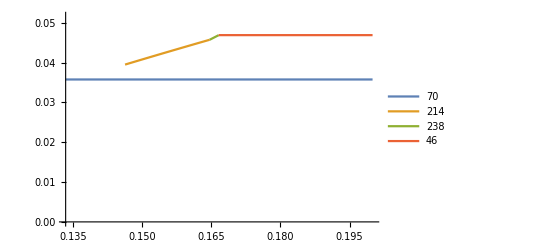

```mathematica
lrlst=DeleteDuplicates[Flatten[pilim[[All,2]]]]
ymax=1.1*Max[Flatten[pilim[[All,3]]]];
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]];
Quiet[Show[Table[Plot[FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR2->x}]],{x,0.05,.2},PlotStyle->collr[[kk]],PlotRange->{All,{0,ymax}},PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]]
```

#### Both Phosphorous and Glucose gradients

```mathematica
xin[[44]]=.3;
lrlst={34,46,58,70,214,238,262};
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349]}

```mathematica
xin[[iR2]]=1.;
Show[Table[Plot[FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x}]],{x,0,.1},PlotStyle->collr[[kk]],PlotRange->{All,{0,ymax}},PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]
```

-Graphics-

```mathematica
R1x=.1;
R2x=.5;
AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,R1x},{y,0,R2x},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotLegends->{lrlst[[kk]]},MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,Length[lrlst]}],ImageSize->700]]]
```

```mathematica
vtxsz3=vtxsz2*1.2;
imgsz3=300;
thicc3=Thickness[0.008];
avcoord2=Table[Mean[Nest[First,overview,Length[lrlst]][[1,i,1,1,1;;-1,{1,2}]]],{i,Length[lrlst]}]
DeleteDuplicates[Table[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,ReplacePart[xin,{iR1->avcoord2[[j,1]],iR2->avcoord2[[j,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2],{j,Length[lrlst]}]];
lbl=Table[Show[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,ReplacePart[xin,{iR1->avcoord2[[j,1]],iR2->avcoord2[[j,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2]],{j,Length[lrlst]}];

fulllbl=Table[Show[Graphics[{collr[[i]],Disk[{0,2},.15]}],lbl[[i]]],{i,Length[lrlst]}]

Do[
fig=fulllbl[[i]];
Export[StringJoin["figures/fig6leg",ToString[i],".png"],fig,"PNG",ImageResolution->resol];
,{i,Length[lbl]}]
```

{{0.0251582,0.383112},{0.0190011,0.183327},{0.0662118,0.37402},{0.0690771,0.222707},{0.0324209,0.0962409},{0.0224022,0.0750741},{0.0546805,0.0647898}}

```mathematica
(*dL=.8;
dD=.6;
eqcl=GatherBy[Range[1,Length[lrlst]],GraphMetabNetLoop[limcombi[[lrlst[[#]]]],system,ReplacePart[xin,{iR1->avcoord2[[#,1]],iR2->avcoord2[[#,2]]}],coordsub,{Red,thicc3},Opacity[0],vtxsz2,imgsz2]&];
coleqcl=Delete[ColorData[97,"ColorList"],2][[Range[1,Length[eqcl]]]];
cols=Table[Table[dc=(dD+dL)/(Length[eqcl[[i]]]+1);If[j*dc<dL,Lighter[coleqcl[[i]],dL-j*dc],Darker[coleqcl[[i]],j*dc-dL]],{j,Length[eqcl[[i]]]}],{i,Length[eqcl]}]

lrlst=Table[lrlst[[j]],{j,Flatten[eqcl]}];
collr=Flatten[cols];*)
```

```mathematica
(*dL=.8;
dD=.6;*)
dL=.2;
dD=.2;
eqcl=GatherBy[Range[1,Length[lrlst]],GraphMetabNetLoop[limcombi[[lrlst[[#]]]],system,ReplacePart[xin,{iR1->avcoord2[[#,1]],iR2->avcoord2[[#,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2]&]
coleqcl=Delete[ColorData[97,"ColorList"],2][[Range[1,Length[eqcl]]]];
cols=Table[Table[dc=(dD+dL)/(Length[eqcl[[i]]]+1);If[j*dc<dL,Lighter[coleqcl[[i]],dL-j*dc],Darker[coleqcl[[i]],j*dc-dL]],{j,Length[eqcl[[i]]]}],{i,Length[eqcl]}]

(*lrlst=Table[lrlst[[j]],{j,Flatten[eqcl]}]*)
(*collr=Table[collr[[kk]],{kk,Length[lrlst]}];*)
lrlst
(*collr=Flatten[cols][[Flatten[eqcl]]]*)
collr=Flatten[cols][[Table[Position[Flatten[eqcl],i][[1,1]],{i,Length[lrlst]}]]]
```

{{1,2},{3,4},{5},{6},{7}}

{{RGBColor[0.41052253333333333, 0.5396604, 0.7291448],RGBColor[0.3438558666666667, 0.47299373333333333, 0.6624781333333334]},{RGBColor[0.5895022666666667, 0.7121310666666667, 0.24855933333333335],RGBColor[0.5228356000000001, 0.6454644, 0.18189266666666667]},{RGBColor[0.922526, 0.385626, 0.209179]},{RGBColor[0.528488, 0.470624, 0.701351]},{RGBColor[0.772079, 0.431554, 0.102387]}}

{34,46,58,70,214,238,262}

{RGBColor[0.41052253333333333, 0.5396604, 0.7291448],RGBColor[0.3438558666666667, 0.47299373333333333, 0.6624781333333334],RGBColor[0.5895022666666667, 0.7121310666666667, 0.24855933333333335],RGBColor[0.5228356000000001, 0.6454644, 0.18189266666666667],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387]}

```mathematica
AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,R1x},{y,0,R2x},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotLegends->{lrlst[[kk]]},MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,Length[lrlst]}],ImageSize->700]]]
```

```mathematica
fulllbl=Table[Show[Graphics[{collr[[i]],Disk[{0,2},.15]}],lbl[[i]]],{i,Length[lrlst]}]

Do[
fig=fulllbl[[i]];
Export[StringJoin["figures/fig6leg",ToString[i],".png"],fig,"PNG",ImageResolution->resol];
,{i,Length[lbl]}]
```

```mathematica
xin[[iR2]]=.4;
ASScut=Show[Table[Plot[FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x}]],{x,0,.1},PlotStyle->collr[[kk]],PlotRange->{All,{0,ymax}}],{kk,Length[lrlst]}]]
Export[StringJoin["figures/fig6b.png"],ASScut,"PNG",ImageResolution->resol];
Export[StringJoin["figures/fig6b.pdf"],ASScut,"PDF"];
```

```mathematica
(*ZNGI*)
ZNGI1=Quiet[Show[Table[ContourPlot[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]==.025,{x,0,R1x},{y,0,R2x},ContourStyle->collr[[kk]],PlotRange->{{0,.1},{0,.5}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}],ImageSize->700]]
```

```mathematica
AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,R1x},{y,0,R2x},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotLegends->{fulllbl[[kk]]},MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]},AxesLabel->{"Glucose","Phosphorus","Growth rate"},BaseStyle->{FontWeight->"Bold",FontSize->18}],{kk,Length[lrlst]}],ImageSize->700]]]
```

```mathematica
AbsoluteTiming[test=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,R1x},{y,0,R2x},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotLegends->{If[Position[eqcl,kk][[1,2]]==Length[eqcl[[Position[eqcl,kk][[1,1]]]]],lbl[[kk]],None]},MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]},BaseStyle->{FontWeight->"Bold",FontSize->16},TicksStyle->Directive[FontOpacity->0,FontSize->0],ViewPoint->{-1,-2,1}],{kk,{1}}],Graphics3D[Text["Glucose",Scaled[{0.45,-.15,0}]]],Graphics3D[Text["Phosphorus",Scaled[{-.15,.45,0}]]],Graphics3D[Text["Growth rate",Scaled[{1,1,1.15}]]],ImageSize->700]]]
Export[StringJoin["figures/test.png"],test,"PNG",ImageResolution->resol];
Export[StringJoin["figures/test.pdf"],test,"PDF"];
```

```mathematica
(*Timing[hull=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,.05},{y,0,.2},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotPoints->50, MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,{6}}],ImageSize->700]]]*)
```

```mathematica
(*AbsoluteTiming[hull=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,.05},{y,0,.2},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotPoints->20, MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,{6}}],ImageSize->700]]]*)
```

```mathematica
(*AbsoluteTiming[hull=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,.05},{y,0,.2},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotPoints->40, MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,{6}}],ImageSize->700]]]*)
```

```mathematica
AbsoluteTiming[
part1=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,R1x},{y,0,R2x},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},MaxRecursion->5,MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]},BaseStyle->{FontWeight->"Bold",FontSize->16},TicksStyle->Directive[FontOpacity->0,FontSize->0]],{kk,Complement[Range[1,Length[lrlst]],{5,6,7}]}],ImageSize->700]]]
```

```mathematica
(*the reasonnable run: takes 15min*)
AbsoluteTiming[sliver=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,.055},{y,0,.2},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotPoints->50,MaxRecursion->3,MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,{5,6}}],ImageSize->700]]]
```

```mathematica
(*VERY LONG: takes 1h??*)
AbsoluteTiming[sliver=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,.055},{y,0,.2},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotPoints->50,MaxRecursion->4,PlotLegends->{If[Position[eqcl,kk][[1,2]]==Length[eqcl[[Position[eqcl,kk][[1,1]]]]],lbl[[kk]],None]},MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,{5,6}}],ImageSize->700]]]
```

```mathematica
AbsoluteTiming[
part3=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,R1x},{y,0,R2x},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},MaxRecursion->5,MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,{7}}],ImageSize->700]]];
```

```mathematica
GLC1=Show[part1,sliver,part3,ViewPoint->{-1,-2,1},ViewAngle->35°]
Export[StringJoin["figures/fig6.png"],GLC1,"PNG",ImageResolution->resol];
Export[StringJoin["figures/fig6.pdf"],GLC1,"PDF"];
```

```mathematica
rota=-Graphics3D-;
Export[StringJoin["figures/fig6c.png"],rota,"PNG",ImageResolution->resol];
Export[StringJoin["figures/fig6c.pdf"],rota,"PDF"];
```

```mathematica
GLC1=Show[part1,sliver,part3,Graphics3D[Text["Glucose",Scaled[{0.45,-.15,0}]]],Graphics3D[Text["Phosphorus",Scaled[{-.15,.45,0}]]],Graphics3D[Text["Growth rate",Scaled[{1,1,1.15}]]],ViewPoint->{-1,-2,1},ViewAngle->35°]
Export[StringJoin["figures/fig7.png"],GLC1,"PNG",ImageResolution->resol];
Export[StringJoin["figures/fig7.pdf"],GLC1,"PDF"];
```

-Graphics3D-

### Exploratory random kinetics parameters

```mathematica
totlregm={};
totautocat={};
totparam={};
```

```mathematica
Do[
α=SparseArray[Table[k->1+.3*RandomReal[{-1,1}],{k,input}]];
μ=Table[1+.3*RandomReal[{-1,1}],{k,p}];
μ[[63]]=.3+.2*RandomReal[{-1,1}];

xin=Table[0,{i,n}];
Do[xin[[i]]=1.,{i,essent}];
Rgrad=35;
system={S2,metabo,reacnames2,submeta,subreac2,α,μ};

Timing[gllim=Table[xin[[Rgrad]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.02,.1,.02]}]];

lrlst=Sort[DeleteDuplicates[Flatten[gllim[[All,2]]]]];
avcoord=Table[listi=Position[gllim[[All,2]],j][[1;;-1,1]];Mean[gllim[[listi]][[1;;-1,1]]],{j,lrlst}];

autocat=Table[xin[[Rgrad]]=avcoord[[j]];
GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{Red,Thickness[.007]},Opacity[0],vtxsz2,imgsz2],{j,Length[lrlst]}];

Do[ix=Position[totautocat,autocat[[i]]];If[ix=={},
AppendTo[totautocat,autocat[[i]]];AppendTo[totlregm,{lrlst[[i]]}];AppendTo[totparam,{α,μ}],
If[MemberQ[totlregm[[ix[[1,1]]]],lrlst[[i]]],False,AppendTo[totlregm[[ix[[1,1]]]],lrlst[[i]]]]],{i,Length[autocat]}];
,{j,20}]
```

```mathematica
Transpose[{totlregm,totautocat}]//MatrixForm
```

```mathematica
j=1;
{α,μ}=totparam[[j]];
system={S2,metabo,reacnames2,submeta,subreac2,α,μ};
Timing[gllim=Table[xin[[Rgrad]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.02,.1,.02]}]]
```

{19.0469,{{0.02,{34},{0.0258291}},{0.04,{82},{0.0381382}},{0.06,{82},{0.0381382}},{0.08,{82},{0.0381382}},{0.1,{82},{0.0381382}}}}

```mathematica
lrlst=Sort[DeleteDuplicates[Flatten[gllim[[All,2]]]]]
ymax=1.1*Max[Flatten[gllim[[All,3]]]];
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]];
Quiet[Show[Table[Plot[xin[[Rgrad]]=x;FindQSSselfc[limcombi[[lrlst[[kk]]]],system,xin],{x,0,.1},PlotStyle->collr[[kk]],PlotRange->{All,{0,ymax}},PlotPoints->50,MaxRecursion->3,PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]]
(*computing average coordinates for the point identified, to get a "representative" supply to look at the network*)
avcoord=Table[listi=Position[gllim[[All,2]],j][[1;;-1,1]];Mean[gllim[[listi]][[1;;-1,1]]],{j,lrlst}]

Table[xin[[Rgrad]]=avcoord[[j]];
{avcoord[[j]],lrlst[[j]],Show[GraphMetabNetLim[limcombi[[lrlst[[j]]]],system,coordsub,Red,vtxsz2,imgsz2],GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{Red,Thickness[.008]},Opacity[0],vtxsz2,imgsz2]],LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin]],system,{Red,Thickness[.008]},cordstyle,vtxsz2,imgsz2],DisplayQSS[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin],system,xin]},{j,Length[lrlst]}]
```

{286,646}

-Graphics-

{0.06,0.06}

### Exploratory random kinetics parameters & supplies

```mathematica
totlregm={};
totautocat={};
totparam={};
```

```mathematica
(*let's add fructose (30)*)
essent={30,35,44,61};

Do[
α=SparseArray[Table[k->1+.3*RandomReal[{-1,1}],{k,input}]];
μ=Table[1+.3*RandomReal[{-1,1}],{k,p}];
μ[[63]]=.3+.2*RandomReal[{-1,1}];

xin=Table[0,{i,n}];
Do[xin[[i]]=0.01+.5*RandomReal[{0,1}],{i,essent}];
Rgrad=35;
system={S2,metabo,reacnames2,submeta,subreac2,α,μ};

Timing[gllim=Table[xin[[Rgrad]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.02,1.,.2]}]];

lrlst=Sort[DeleteDuplicates[Flatten[gllim[[All,2]]]]];
avcoord=Table[listi=Position[gllim[[All,2]],j][[1;;-1,1]];Mean[gllim[[listi]][[1;;-1,1]]],{j,lrlst}];

autocat=Table[xin[[Rgrad]]=avcoord[[j]];
GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{Red,Thickness[.007]},Opacity[0],vtxsz2,imgsz2],{j,Length[lrlst]}];

Do[ix=Position[totautocat,autocat[[i]]];If[ix=={},
AppendTo[totautocat,autocat[[i]]];AppendTo[totlregm,{lrlst[[i]]}];AppendTo[totparam,{α,μ,xin}],
If[MemberQ[totlregm[[ix[[1,1]]]],lrlst[[i]]],False,AppendTo[totlregm[[ix[[1,1]]]],lrlst[[i]]]]],{i,Length[autocat]}];
,{j,1}]
```

$Aborted

```mathematica
Transpose[{totlregm,totautocat}]//MatrixForm
```

```mathematica
j=4;
{α,μ,xin}=totparam[[j]];
system={S2,metabo,reacnames2,submeta,subreac2,α,μ};
Timing[gllim=Table[xin[[Rgrad]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.02,.1,.02]}]]
```

Part::partw: Part 4 of {{SparseArray[«1»],{1.24411,1.26025,1.12591,0.985429,0.961354,1.0785,1.20687,0.75469,1.08663,0.783644,1.29007,1.23378,0.89834,1.19392,«24»,0.861344,0.961257,0.726535,0.751849,0.75969,1.10837,1.17994,0.741511,1.23732,1.14225,1.05021,1.05038,«64»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.233147,0,0,0,0,0.42,0,0,0,0,0,0,0,0,0.416136,0,0,0,0,0,0,«23»}}} does not exist.

Set::shape: Lists {α,μ,xin} and {{SparseArray[Automatic,«3»],{1.24411,1.26025,1.12591,0.985429,0.961354,1.0785,1.20687,0.75469,1.08663,0.783644,1.29007,1.23378,0.89834,«25»,0.861344,0.961257,0.726535,0.751849,0.75969,1.10837,1.17994,0.741511,1.23732,1.14225,1.05021,1.05038,«64»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.233147,0,0,0,0,0.42,0,0,0,0,0,0,0,0,0.416136,0,0,0,0,0,0,«23»}}}⟦4⟧ are not the same shape.

$Aborted

```mathematica
lrlst=Sort[DeleteDuplicates[Flatten[gllim[[All,2]]]]]
ymax=1.1*Max[Flatten[gllim[[All,3]]]];
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]];
Quiet[Show[Table[Plot[xin[[Rgrad]]=x;FindQSSselfc[limcombi[[lrlst[[kk]]]],system,xin],{x,0,.1},PlotStyle->collr[[kk]],PlotRange->{All,{0,ymax}},PlotPoints->50,MaxRecursion->3,PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]]
(*computing average coordinates for the point identified, to get a "representative" supply to look at the network*)
avcoord=Table[listi=Position[gllim[[All,2]],j][[1;;-1,1]];Mean[gllim[[listi]][[1;;-1,1]]],{j,lrlst}]

Table[xin[[Rgrad]]=avcoord[[j]];
{avcoord[[j]],lrlst[[j]],Show[GraphMetabNetLim[limcombi[[lrlst[[j]]]],system,coordsub,Red,vtxsz2,imgsz2],GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{Red,Thickness[.008]},Opacity[0],vtxsz2,imgsz2]],LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin]],system,{Red,Thickness[.008]},cordstyle,vtxsz2,imgsz2],DisplayQSS[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin],system,xin]},{j,Length[lrlst]}]
```

{34,82}

-Graphics-

{0.02,0.07}

#### Cherry picked example for glc/fru surface

```mathematica
α=SparseArray[…];
μ={0.8430035610709055,1.0232365833916517,1.2200591314021243,1.0452178121010232,1.128694584564115,1.135978476543629,1.0700801873936352,0.76860840688195,1.1958640929597748,1.2620158389080158,1.1044056907264974,1.0646571262577016,1.0361384171841068,0.9571205522205993,0.8124637884763648,1.2928324318148936,0.8800939523359363,1.0449126186782398,0.8744431231707732,0.8189244859422576,0.7906608615000557,1.0167269729154316,1.272430608772457,1.1679999215249282,0.7084659947418626,0.9471260376762842,1.2145794187305905,1.0673289676496374,1.0119909647851546,1.278034619673629,0.8751644378361976,0.8367392904774235,1.0472344457452436,0.8081495331471772,1.1390887441257225,1.137575634916794,0.7570592049824043,0.734620410076229,0.8984888517103484,1.0318822772084864,0.9080871362066117,0.9204421627081837,0.7131925932085921,1.21690435083655,1.0190972976601806,0.7828735555276488,0.7238071740206897,0.8188237275304657,1.259752308660808,0.8439794130008631,1.1022370744366203,1.2165369927766678,0.7683869516284099,1.2824078370119922,1.2768631328550455,1.18604495642149,1.000645553962353,1.2936521129406622,1.1552341760852805,0.8733933567183104,0.909561657824482,0.9934662621427319,0.49470829903392594,1.261321976894432,0.7956396921418141,1.0233918049389927,1.2567643383917133,1.0213939202758344,1.2021812202295492,0.7627609729657587,0.7183547163324595,0.8045471877547075,1.2810498470126768,1.0284717172250153,1.2869441267309378,1.2389844004771349,0.9863347222717035,0.7703700172752246,0.8854023658190509,1.2712908947209867,1.219530987376518,1.0777793275977725,1.2912634310331403,1.0913884134530232,1.074478727148328,1.0294118788302427,1.0389665608947924,1.0401097068427494,0.9471623216355347,0.9477678780796359,1.1025035661196765,1.1378334901745701,1.0911554043098441,0.9117325733440407,1.0821004342222311,1.1090873343228131,1.2866365256146817,1.0394848591233,1.2350054865512092,0.9719688792710407,0.9057196296957861,0.8763375971261174,0.7031534901902798,1.2560500105499308,1.1195985164920499,1.222268745747629,0.9867468021623129,1.0163589195723721,1.1831641835309454,0.9305047435220481,1.1059186798816922,1.0804041469873606,1.2190571996388664,0.9087560514564368};
xin={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.05919587470236217,0,0,0,0,0.04065738344342008,0,0,0,0,0,0,0,0,0.20952096490959138,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.3017911800734234,0,0,0,0,0,0,0,0,0,0,0,0};
system={S2,metabo,reacnames2,submeta,subreac2,α,μ};
```

```mathematica
iR1=35;
iR2=30;
R1x=.055;
R2x=.09;
lrlst=Sort[{34,82,202,226,250,274,322,490,514,538}];
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]];
ymax=.06;
```

```mathematica
AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,R1x},{y,0,R2x},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotLegends->{lrlst[[kk]]},MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,Length[lrlst]}],ImageSize->700]]]
```

```mathematica
vtxsz3=vtxsz2*1.2;
imgsz3=300;
thicc3=Thickness[0.008];
avcoord2=Table[Mean[Nest[First,overview,Length[lrlst]][[1,i,1,1,1;;-1,{1,2}]]],{i,Length[lrlst]}]
DeleteDuplicates[Table[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,ReplacePart[xin,{iR1->avcoord2[[j,1]],iR2->avcoord2[[j,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2],{j,Length[lrlst]}]];
lbl=Table[Show[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,ReplacePart[xin,{iR1->avcoord2[[j,1]],iR2->avcoord2[[j,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2]],{j,Length[lrlst]}];

fulllbl=Table[Show[Graphics[{collr[[i]],Disk[{0,2},.15]}],lbl[[i]]],{i,Length[lrlst]}]

Do[
fig=fulllbl[[i]];
,{i,Length[lbl]}]
```

{{0.017783,0.0293068},{0.0457,0.0130961},{0.030678,0.0523456},{0.0309729,0.0450544},{0.0433483,0.0445998},{0.0451221,0.0330351},{0.00883944,0.0731914},{0.0303516,0.0714293},{0.0225974,0.0742204},{0.0394153,0.0683271}}

```mathematica
(*vtxsz3=vtxsz2*1.2;
imgsz3=300;
thicc3=Thickness[0.008];
avcoord2=Table[Mean[Nest[First,overview,Length[lrlst]][[1,i,1,1,1;;-1,{1,2}]]],{i,Length[lrlst]}]
DeleteDuplicates[Table[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,ReplacePart[xin,{iR1->avcoord2[[j,1]],iR2->avcoord2[[j,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2],{j,Length[lrlst]}]];
lbl=Table[Show[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,ReplacePart[xin,{iR1->avcoord2[[j,1]],iR2->avcoord2[[j,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2]],{j,Length[lrlst]}]

Do[
fig=Show[Graphics[{collr[[i]],Disk[{0,2},.15]}],lbl[[i]]];
Export[StringJoin["figures/fig7leg",ToString[i],".png"],fig,"PNG",ImageResolution->resol];
,{i,Length[lbl]}]*)
```

```mathematica
dL=dD=.2;
eqcl=GatherBy[Range[1,Length[lrlst]],GraphMetabNetLoop[limcombi[[lrlst[[#]]]],system,ReplacePart[xin,{iR1->avcoord2[[#,1]],iR2->avcoord2[[#,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2]&];
coleqcl=Delete[ColorData[97,"ColorList"],2][[Range[1,Length[eqcl]]]];
cols=Table[Table[dc=(dD+dL)/(Length[eqcl[[i]]]+1);If[j*dc<dL,Lighter[coleqcl[[i]],dL-j*dc],Darker[coleqcl[[i]],j*dc-dL]],{j,Length[eqcl[[i]]]}],{i,Length[eqcl]}]

lrlst;
collr=Flatten[cols][[Table[Position[Flatten[eqcl],i][[1,1]],{i,Length[lrlst]}]]]
```

{{RGBColor[0.368417, 0.506779, 0.709798]},{RGBColor[0.560181, 0.691569, 0.194885]},{RGBColor[0.922526, 0.385626, 0.209179]},{RGBColor[0.528488, 0.470624, 0.701351]},{RGBColor[0.772079, 0.431554, 0.102387]},{RGBColor[0.363898, 0.618501, 0.782349]},{RGBColor[1., 0.75, 0.]},{RGBColor[0.647624, 0.37816, 0.614037]},{RGBColor[0.571589, 0.586483, 0.]},{RGBColor[0.915, 0.3325, 0.2125]}}

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1., 0.75, 0.],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125]}

```mathematica
fulllbl=Table[Show[Graphics[{collr[[i]],Disk[{0,2},.15]}],lbl[[i]]],{i,Length[lrlst]}]

Do[
fig=fulllbl[[i]];
Export[StringJoin["figures/fig7leg",ToString[i],".png"],fig,"PNG",ImageResolution->resol];
,{i,Length[lbl]}]
```

```mathematica
AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,R1x},{y,0,R2x},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotLegends->{fulllbl[[kk]]},MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,Length[lrlst]}],ImageSize->700]]]
```

{67.6367,-Graphics3D-}

```mathematica
AbsoluteTiming[
part1=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,R1x},{y,0,R2x},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},MaxRecursion->7,MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]},TicksStyle->Directive[FontOpacity->0,FontSize->0]],{kk,Length[lrlst]}],ImageSize->700]]]
```

```mathematica
GLC2=Show[part1,ViewPoint->{-1,-2,1},ViewAngle->35°]
Export[StringJoin["figures/fig7.png"],GLC2,"PNG",ImageResolution->resol];
Export[StringJoin["figures/fig7.pdf"],GLC2,"PDF"];
```

### Exploratory: GAM is pyr-limited, random kinetics parameters & supplies

```mathematica
(*simplified biomass reaction that uses 1 pyr, 1 NADH and 1 ATP*)

metabo[[{17,51,62}]]
(*randcoef=RandomReal[{0,1},3];*)
(*no need to use random coefs, this can just be tweaked by hand*)
randcoef={1,1,3}

Do[S2[[i,GAMi]]=0.,{i,Length[S2[[All,13]]]}]
Do[S2[[{17,51,62}[[i]],GAMi]]=-randcoef[[i]],{i,3}]
(*and creates 1 cell, 1 NAD and 1 ADP*)
Do[S2[[{13,50,73}[[i]],GAMi]]=randcoef[[i]],{i,2}]
S2[[73,GAMi]]=1;

(*when we create one new cell, it also creates the NAD and NAD that comes with it (newborn cells are "discharged");other scenarios are possible, as long as they maintain mass balance of the conserved pools! *)
(*total amount of balanced mass: crucial for keeping conserved metabolites mass-balanced by the birth reaction*)
massbal0=3;
Do[S2[[i,GAMi]]=S2[[i,GAMi]]+2*massbal0,{i,{13,50}}]
```

{atp,nadh,pyr}

{1,1,3}

```mathematica
totlregm={};
totautocat={};
totparam={};
```

```mathematica
(*let's add fructose (30)*)
essent={30,35,44,61};

Do[
α=SparseArray[Table[k->1+.3*RandomReal[{-1,1}],{k,input}]];
μ=Table[1+.3*RandomReal[{-1,1}],{k,p}];
μ[[63]]=.3+.2*RandomReal[{-1,1}];

xin=Table[0,{i,n}];
(*Do[xin[[i]]=1.,{i,essent}];*)
Do[xin[[i]]=0.01+.5*RandomReal[{0,1}],{i,essent}];
Rgrad=35;
system={S2,metabo,reacnames2,submeta,subreac2,α,μ};

Timing[gllim=Table[xin[[Rgrad]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.02,1.,.2]}]];

lrlst=Sort[DeleteDuplicates[Flatten[gllim[[All,2]]]]];
avcoord=Table[listi=Position[gllim[[All,2]],j][[1;;-1,1]];Mean[gllim[[listi]][[1;;-1,1]]],{j,lrlst}];

autocat=Table[xin[[Rgrad]]=avcoord[[j]];
GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{Red,Thickness[.007]},Opacity[0],vtxsz2,imgsz2],{j,Length[lrlst]}];

Do[ix=Position[totautocat,autocat[[i]]];If[ix=={},
AppendTo[totautocat,autocat[[i]]];AppendTo[totlregm,{lrlst[[i]]}];AppendTo[totparam,{α,μ,xin}],
If[MemberQ[totlregm[[ix[[1,1]]]],lrlst[[i]]],False,AppendTo[totlregm[[ix[[1,1]]]],lrlst[[i]]]]],{i,Length[autocat]}];
,{j,20}]
```

```mathematica
Transpose[{totlregm,totautocat}]//MatrixForm
```

```mathematica
j=4;
{α,μ,xin}=totparam[[j]];
system={S2,metabo,reacnames2,submeta,subreac2,α,μ};
Timing[gllim=Table[xin[[Rgrad]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.02,.1,.02]}]]
```

{25.7813,{{0.02,{1678},{0.0267601}},{0.04,{1726},{0.0268095}},{0.06,{1726},{0.0268095}},{0.08,{1726},{0.0268095}},{0.1,{1726},{0.0268095}}}}

```mathematica
lrlst=Sort[DeleteDuplicates[Flatten[gllim[[All,2]]]]]
ymax=1.1*Max[Flatten[gllim[[All,3]]]];
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]];
Quiet[Show[Table[Plot[xin[[Rgrad]]=x;FindQSSselfc[limcombi[[lrlst[[kk]]]],system,xin],{x,0,.1},PlotStyle->collr[[kk]],PlotRange->{All,{0,ymax}},PlotPoints->50,MaxRecursion->3,PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]]
(*computing average coordinates for the point identified, to get a "representative" supply to look at the network*)
avcoord=Table[listi=Position[gllim[[All,2]],j][[1;;-1,1]];Mean[gllim[[listi]][[1;;-1,1]]],{j,lrlst}]

Table[xin[[Rgrad]]=avcoord[[j]];
{avcoord[[j]],lrlst[[j]],Show[GraphMetabNetLim[limcombi[[lrlst[[j]]]],system,coordsub,Red,vtxsz2,imgsz2],GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{Red,Thickness[.008]},Opacity[0],vtxsz2,imgsz2]],LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin]],system,{Red,Thickness[.008]},cordstyle,vtxsz2,imgsz2],DisplayQSS[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin],system,xin]},{j,Length[lrlst]}]
```

{1678,1726}

-Graphics-

{0.02,0.07}

#### Cherry picked example for glc/Pi surface

```mathematica
randcoef={1,1,3}

Rgrad=35;
Do[S2[[i,GAMi]]=0.,{i,Length[S2[[All,13]]]}]
Do[S2[[{17,51,62}[[i]],GAMi]]=-randcoef[[i]],{i,3}]
Do[S2[[{13,50,73}[[i]],GAMi]]=randcoef[[i]],{i,2}]
S2[[73,GAMi]]=1;
massbal0=3;
Do[S2[[i,GAMi]]=S2[[i,GAMi]]+2*massbal0,{i,{13,50}}]
α=SparseArray[…];
μ={1.1109431049787586,1.265333325522579,1.082429301340242,1.111584893443359,0.9771662098730673,1.1209234508037653,1.1653086831855175,1.0179569731643652,0.7380683662332976,0.8930994678757153,0.7100901438846527,0.8265739370278624,1.2746044983555465,0.9455970844775874,0.9484013569486183,1.2174660050122637,1.074748822963339,0.8759020935088361,0.9166907478197717,1.0035053243947367,0.8106574114242089,1.218921593586102,1.0803347830339012,0.764509883568668,0.7092746006853717,1.1161354577888487,1.054219336101522,0.7587913276344895,1.172048490092754,0.9961320118191774,1.1611363927582312,1.0579873153135029,1.2209255935200052,1.0237159291121618,1.1288762021392682,1.1094346313828423,0.8191568952168243,0.7302192036885182,0.7541216997916598,0.796127045914234,1.1222470581478328,0.8393046788472295,0.7427353011629028,0.9856603768432388,0.9551972795433825,1.2025050780260622,0.8405579297874335,0.864048306626384,0.8959235027641482,0.9780382984334666,0.8440761807535277,0.7391107128672678,0.723618125461202,0.9719943037973775,0.9301929982398105,0.9571396327720291,1.2111298761362899,0.843178900362817,1.2214665107533926,0.7843711104426847,1.1699226039773967,0.9347911395333472,0.42186310031281316,1.0353132949380388,0.7040254672768599,1.113256530975831,1.19846130837951,0.7809514358297611,0.834690076062411,0.780525142407564,1.166915470770165,0.9560126241641707,1.2454700412642568,1.1122083469510862,1.174004526990064,0.9834356651685405,0.710855050430022,0.8215932995660541,0.9802964097830402,0.9338216163804749,1.2583652614315408,1.167202777949011,1.1267733414831222,0.9404770124525594,0.8566248298994696,1.1374163278574114,0.8707165495093626,1.114864756752357,0.8886720089636241,1.045100581628509,0.7119976376397001,1.0158871552497812,1.0537620160131924,1.214684965667729,0.8076475612431229,1.2054376031973462,0.7991066474012144,1.2760744803559616,1.0806333008452267,1.186263730481898,0.729507768141896,0.8547123800915887,1.0361485067054013,0.915304029568881,1.2677492972310167,1.0951754888572895,1.1564788622873068,0.7852531184193389,0.9274215944969657,1.1557434625150782,0.7992230728267445,1.2000648725751668,1.033570726476403,1.0108688550602996};
xin={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.16907874257635747,0,0,0,0,0.07,0,0,0,0,0,0,0,0,0.31529675826834835,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.2288461013172427,0,0,0,0,0,0,0,0,0,0,0,0};
system={S2,metabo,reacnames2,submeta,subreac2,α,μ};
```

{1,1,3}

```mathematica
xin[[61]]=.4;
xin[[30]]=.09;
Timing[gllim=Table[xin[[Rgrad]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.001,.1,.002]}]]
```

{30.1406,{{0.001,{1198},{0.0388599}},{0.003,{1198},{0.0397808}},{0.005,{1198},{0.0406903}},{0.007,{1198},{0.0415889}},{0.009,{1198},{0.0424769}},{0.011,{1390},{0.0433023}},{0.013,{1390},{0.0433707}},{0.015,{1678},{0.0434092}},{0.017,{1678},{0.0434323}},{0.019,{1678},{0.0434555}},{0.021,{1678},{0.0434787}},{0.023,{1678},{0.0435019}},{0.025,{1678},{0.0435252}},{0.027,{1678},{0.0435485}},{0.029,{1678},{0.0435718}},{0.031,{1678},{0.0435951}},{0.033,{1678},{0.0436184}},{0.035,{1678},{0.0436418}},{0.037,{1678},{0.0436652}},{0.039,{1678},{0.0436886}},{0.041,{1678},{0.0437121}},{0.043,{1678},{0.0437355}},{0.045,{1726},{0.043738}},{0.047,{1726},{0.043738}},{0.049,{1726},{0.043738}},{0.051,{1726},{0.043738}},{0.053,{1726},{0.043738}},{0.055,{1726},{0.043738}},{0.057,{1726},{0.043738}},{0.059,{1726},{0.043738}},{0.061,{1726},{0.043738}},{0.063,{1726},{0.043738}},{0.065,{1726},{0.043738}},{0.067,{1726},{0.043738}},{0.069,{1726},{0.043738}},{0.071,{1726},{0.043738}},{0.073,{1726},{0.043738}},{0.075,{1726},{0.043738}},{0.077,{1726},{0.043738}},{0.079,{1726},{0.043738}},{0.081,{1726},{0.043738}},{0.083,{1726},{0.043738}},{0.085,{1726},{0.043738}},{0.087,{1726},{0.043738}},{0.089,{1726},{0.043738}},{0.091,{1726},{0.043738}},{0.093,{1726},{0.043738}},{0.095,{1726},{0.043738}},{0.097,{1726},{0.043738}},{0.099,{1726},{0.043738}}}}

```mathematica
iR1=35;
iR2=61;
R1x=.07;
R2x=1;
ymax=.06;
(*lrlst=Sort[{1186,1198,1390,1378,1654,1666,1678,1702,1714}];*)
lrlst=Sort[{1474,1486,1666,1678,1714,1726}];
lrlst=Sort[{1186,1198,1378,1390,1666,1678,1714,1726}];
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]];
```

```mathematica
xin[[30]]=.08;
AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,R1x},{y,0,R2x},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotLegends->{lrlst[[kk]]},MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,Length[lrlst]}],ImageSize->700]]]
```

```mathematica
(*avcoord2=Table[Mean[Nest[First,overview,Length[lrlst]][[1,i,1,1,1;;-1,{1,2}]]],{i,Length[lrlst]}]
Table[xin[[35]]=avcoord2[[j,1]];xin[[30]]=avcoord2[[j,2]];
{lrlst[[j]],Show[GraphMetabNetLim[limcombi[[lrlst[[j]]]],system,coordsub,Red,vtxsz2,imgsz2*2/3],GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{Red,Thickness[.01]},Opacity[0],vtxsz2,imgsz2]]},{j,Length[lrlst]}]*)
```

```mathematica
vtxsz3=vtxsz2*1.2;
imgsz3=300;
thicc3=Thickness[0.008];
avcoord2=Table[Mean[Nest[First,overview,Length[lrlst]][[1,i,1,1,1;;-1,{1,2}]]],{i,Length[lrlst]}]
DeleteDuplicates[Table[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,ReplacePart[xin,{iR1->avcoord2[[j,1]],iR2->avcoord2[[j,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2],{j,Length[lrlst]}]];
lbl=Table[Show[GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,ReplacePart[xin,{iR1->avcoord2[[j,1]],iR2->avcoord2[[j,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2]],{j,Length[lrlst]}]

Do[
fig=Show[Graphics[{collr[[i]],Disk[{0,2},.15]}],lbl[[i]]];
Export[StringJoin["figures/fig8leg",ToString[i],".png"],fig,"PNG",ImageResolution->resol];
,{i,Length[lbl]}]
```

{{0.0181659,0.656729},{0.0124676,0.428035},{0.0386936,0.726611},{0.0239711,0.413009},{0.0467224,0.704389},{0.0199857,0.269961},{0.0572104,0.677984},{0.0419362,0.204353}}

```mathematica
eqcl=GatherBy[Range[1,Length[lrlst]],GraphMetabNetLoop[limcombi[[lrlst[[#]]]],system,ReplacePart[xin,{iR1->avcoord2[[#,1]],iR2->avcoord2[[#,2]]}],coordsub,{col1,thicc3},Automatic,{col2,thicc3},vtxsz2,imgsz2]&];
coleqcl=Delete[ColorData[97,"ColorList"],2][[Range[1,Length[eqcl]]]];
cols=Table[Table[dc=(dD+dL)/(Length[eqcl[[i]]]+1);If[j*dc<dL,Lighter[coleqcl[[i]],dL-j*dc],Darker[coleqcl[[i]],j*dc-dL]],{j,Length[eqcl[[i]]]}],{i,Length[eqcl]}]

lrlst;
collr=Flatten[cols][[Table[Position[Flatten[eqcl],i][[1,1]],{i,Length[lrlst]}]]]
```

{{RGBColor[0.41052253333333333, 0.5396604, 0.7291448],RGBColor[0.3438558666666667, 0.47299373333333333, 0.6624781333333334]},{RGBColor[0.560181, 0.691569, 0.194885]},{RGBColor[0.922526, 0.385626, 0.209179]},{RGBColor[0.528488, 0.470624, 0.701351]},{RGBColor[0.772079, 0.431554, 0.102387]},{RGBColor[0.363898, 0.618501, 0.782349]},{RGBColor[1., 0.75, 0.]}}

{RGBColor[0.41052253333333333, 0.5396604, 0.7291448],RGBColor[0.3438558666666667, 0.47299373333333333, 0.6624781333333334],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1., 0.75, 0.]}

```mathematica
AbsoluteTiming[overview=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,R1x},{y,0,R2x},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},PlotLegends->{If[Position[eqcl,kk][[1,2]]==Length[eqcl[[Position[eqcl,kk][[1,1]]]]],lbl[[kk]],None]},MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,Length[lrlst]}],ImageSize->700]]]
```

```mathematica
AbsoluteTiming[
part1=Quiet[Show[Table[Plot3D[GetQSSλ[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]],{x,0,R1x},{y,0,R2x},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},RegionFunction->Function[{x,y,z},CheckSelfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{iR1->x,iR2->y}]]],Lighting->{{"Ambient",White}},MaxRecursion->7,PlotLegends->{If[Position[eqcl,kk][[1,2]]==Length[eqcl[[Position[eqcl,kk][[1,1]]]]],lbl[[kk]],None]},MeshFunctions->{#3&},Mesh->{Table[i,{i,0,ymax,ymax/20}]}],{kk,Length[lrlst]}],ImageSize->700]]]
```

```mathematica
GLC3=Show[part1,ViewPoint->{-1,-2,1},ViewAngle->35°]
Export[StringJoin["figures/fig9.png"],GLC3,"PNG",ImageResolution->resol];
Export[StringJoin["figures/fig9.pdf"],GLC3,"PDF"];
```

-Graphics3D-

```mathematica
Timing[gllim=Table[xin[[Rgrad]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.02,.1,.02]}]]
```

$Aborted

```mathematica
xin[[61]]=.3;
Timing[gllim=Table[xin[[Rgrad]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.02,.1,.02]}]]
```

{30.1406,{{0.02,{1390},{0.0337453}},{0.04,{1726},{0.0341111}},{0.06,{1726},{0.0341111}},{0.08,{1726},{0.0341111}},{0.1,{1726},{0.0341111}}}}

```mathematica
xin[[30]]=.06;
xin[[61]]=.31;
Timing[gllim=Table[xin[[Rgrad]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.001,.1,.02]}]]
```

{18.8906,{{0.001,{358},{0}},{0.021,{358},{0}},{0.041,{358},{0}},{0.061,{358},{0}},{0.081,{358},{0}}}}

```mathematica
ymax=1.1*Max[Flatten[gllim[[All,3]]]];
lrlst=Sort[{1474,1486,1666,1678,1714,1726}];
lrlst=Sort[{1186,1198,1390,1378,1654,1666,1678,1702,1714}];
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]];
```

```mathematica
xin[[30]]=.06;
Timing[overview=Quiet[Show[Table[Plot3D[
FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{35->x,61->y}]],{x,0,.1},{y,0,1},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},Lighting->{{"Ambient",White}},PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]]]
```

```mathematica
xin[[30]]=.06;
Timing[overview=Quiet[Show[Table[Plot3D[
FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{35->x,61->y}]],{x,0,.1},{y,0,1},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},Lighting->{{"Ambient",White}},PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]]]
```

```mathematica
Quiet[Show[Table[ContourPlot[FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{35->x,61->y}]]==.045,{x,0,.1},{y,0,1},ContourStyle->collr[[kk]],PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}],ImageSize->700]]
```

```mathematica
avcoord2=Table[Mean[Nest[First,overview,Length[lrlst]][[1,i,1,1,1;;-1,{1,2}]]],{i,Length[lrlst]}]
```

{{0.0100448,0.655409},{0.00328201,0.311973},{0.030619,0.645538},{0.0137584,0.288381},{0.0262254,0.132549},{0.0574604,0.647492},{0.0271705,0.221162},{0.0582188,0.150294},{0.0834098,0.635396}}

```mathematica
Table[xin[[35]]=avcoord2[[j,1]];xin[[61]]=avcoord2[[j,2]];
{lrlst[[j]],Show[GraphMetabNetLim[limcombi[[lrlst[[j]]]],system,coordsub,Red,vtxsz2,imgsz2*2/3],GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{Red,Thickness[.01]},Opacity[0],vtxsz2,imgsz2]]},{j,Length[lrlst]}]
```

```mathematica
DeleteDuplicates[Table[xin[[35]]=avcoord2[[j,1]];xin[[61]]=avcoord2[[j,2]];
GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{Red,Thickness[.01]},Opacity[0],vtxsz2,imgsz2],{j,Length[lrlst]}]]
```

```mathematica
Timing[overview=Quiet[Show[Table[Plot3D[
FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{35->x,61->y}]],{x,0,.1},{y,0,1},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},Lighting->{{"Ambient",White}},PlotLegends->{Show[GraphMetabNetLim[limcombi[[lrlst[[kk]]]],system,coordsub,Red,vtxsz2,imgsz2*2/3],GraphMetabNetLoop[limcombi[[lrlst[[kk]]]],system,xin,coordsub,{Red,Thickness[.01]},Opacity[0],vtxsz2,imgsz2]]}],{kk,Length[lrlst]}],ImageSize->700]]]
```

{154.969,-Graphics3D-}

```mathematica
Timing[overview=Quiet[Show[Table[Plot3D[
FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{35->x,61->y}]],{x,0,.1},{y,0,1},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},Lighting->{{"Ambient",White}},PlotLegends->{Show[GraphMetabNetLim[limcombi[[lrlst[[kk]]]],system,coordsub,Red,vtxsz2,imgsz2*2/3],GraphMetabNetLoop[limcombi[[lrlst[[kk]]]],system,xin,coordsub,{Red,Thickness[.01]},Opacity[0],vtxsz2,imgsz2]]}],{kk,Length[lrlst]}],ImageSize->700]]]
```

{116.141,-Graphics3D-}

### Exploratory: GAM is nadh-limited, random kinetics parameters & supplies

```mathematica
(*simplified biomass reaction that uses 1 pyr, 1 NADH and 1 ATP*)

metabo[[{17,51,62}]]
(*randcoef=RandomReal[{0,1},3];*)
(*no need to use random coefs, this can just be tweaked by hand*)
randcoef={1,3,1}

Do[S2[[i,GAMi]]=0.,{i,Length[S2[[All,13]]]}]
Do[S2[[{17,51,62}[[i]],GAMi]]=-randcoef[[i]],{i,3}]
(*and creates 1 cell, 1 NAD and 1 ADP*)
Do[S2[[{13,50,73}[[i]],GAMi]]=randcoef[[i]],{i,2}]
S2[[73,GAMi]]=1;

(*when we create one new cell, it also creates the NAD and NAD that comes with it (newborn cells are "discharged");other scenarios are possible, as long as they maintain mass balance of the conserved pools! *)
(*total amount of balanced mass: crucial for keeping conserved metabolites mass-balanced by the birth reaction*)
massbal0=3;
Do[S2[[i,GAMi]]=S2[[i,GAMi]]+2*massbal0,{i,{13,50}}]
```

{atp,nadh,pyr}

{1,3,1}

```mathematica
totlregm={};
totautocat={};
totparam={};
```

```mathematica
(*let's add fructose (30)*)
essent={30,35,44,61};

Do[
α=SparseArray[Table[k->1+.3*RandomReal[{-1,1}],{k,input}]];
μ=Table[1+.3*RandomReal[{-1,1}],{k,p}];
μ[[63]]=.3+.2*RandomReal[{-1,1}];

xin=Table[0,{i,n}];
(*Do[xin[[i]]=1.,{i,essent}];*)
Do[xin[[i]]=0.01+.5*RandomReal[{0,1}],{i,essent}];
Rgrad=35;
system={S2,metabo,reacnames2,submeta,subreac2,α,μ};

Timing[gllim=Table[xin[[Rgrad]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.02,1.,.2]}]];

lrlst=Sort[DeleteDuplicates[Flatten[gllim[[All,2]]]]];
avcoord=Table[listi=Position[gllim[[All,2]],j][[1;;-1,1]];Mean[gllim[[listi]][[1;;-1,1]]],{j,lrlst}];

autocat=Table[xin[[Rgrad]]=avcoord[[j]];
GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{Red,Thickness[.007]},Opacity[0],vtxsz2,imgsz2],{j,Length[lrlst]}];

Do[ix=Position[totautocat,autocat[[i]]];If[ix=={},
AppendTo[totautocat,autocat[[i]]];AppendTo[totlregm,{lrlst[[i]]}];AppendTo[totparam,{α,μ,xin}],
If[MemberQ[totlregm[[ix[[1,1]]]],lrlst[[i]]],False,AppendTo[totlregm[[ix[[1,1]]]],lrlst[[i]]]]],{i,Length[autocat]}];
,{j,20}]
```

```mathematica
Transpose[{totlregm,totautocat}]//MatrixForm
```

({1102,1150,1126,814,838,862,1078} | -Graphics-
{910,898} | -Graphics-
{1090,1114,1138,1066,802,850} | -Graphics-
{958,946} | -Graphics-
{622,610} | -Graphics-
{922} | -Graphics-
{670,658} | -Graphics-
{490,538} | -Graphics-
{1678,1654} | -Graphics-
{1726,1702} | -Graphics-
{1486} | -Graphics-
{1714,1690} | -Graphics-
{1666,1642} | -Graphics-
{1198,1186} | -Graphics-
{1702} | -Graphics-
{1702} | -Graphics-
{1246} | -Graphics-
{1378} | -Graphics-
{1402,1426} | -Graphics-)

```mathematica
j=16;
{α,μ,xin}=totparam[[j]];
system={S2,metabo,reacnames2,submeta,subreac2,α,μ};
Timing[gllim=Table[xin[[Rgrad]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.02,.1,.02]}]]
```

{18.6563,{{0.02,{1702},{0.00247347}},{0.04,{1702},{0.00247347}},{0.06,{1702},{0.00247347}},{0.08,{1702},{0.00247347}},{0.1,{1702},{0.00247347}}}}

```mathematica
lrlst=Sort[DeleteDuplicates[Flatten[gllim[[All,2]]]]]
ymax=1.1*Max[Flatten[gllim[[All,3]]]];
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]];
Quiet[Show[Table[Plot[xin[[Rgrad]]=x;FindQSSselfc[limcombi[[lrlst[[kk]]]],system,xin],{x,0,.1},PlotStyle->collr[[kk]],PlotRange->{All,{0,ymax}},PlotPoints->50,MaxRecursion->3,PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]]
(*computing average coordinates for the point identified, to get a "representative" supply to look at the network*)
avcoord=Table[listi=Position[gllim[[All,2]],j][[1;;-1,1]];Mean[gllim[[listi]][[1;;-1,1]]],{j,lrlst}]

Table[xin[[Rgrad]]=avcoord[[j]];
{avcoord[[j]],lrlst[[j]],Show[GraphMetabNetLim[limcombi[[lrlst[[j]]]],system,coordsub,Red,vtxsz2,imgsz2],GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{Red,Thickness[.008]},Opacity[0],vtxsz2,imgsz2]],LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin]],system,{Red,Thickness[.008]},cordstyle,vtxsz2,imgsz2],DisplayQSS[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin],system,xin]},{j,Length[lrlst]}]
```

{1702}

-Graphics-

{0.06}

{{0.06,1702,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
PYK | 63 | 0.000772443 | pep | 0
GAM | 13 | 0.00247347 | pyr | 2.6514×10^-6
FRUpts2 | 25 | 0.00311995 | pep | 0
PGI | 54 | 0.00352815 | g6p | 0
GLCpts | 30 | 0.00353427 | pep | 0
TPI | 75 | 0.00572678 | dhap | 0
FBA | 20 | 0.00574453 | fdp | 0
PFK | 52 | 0.00575454 | atp | 0
PIt2r_r | 105 | 0.00595517 | pi | -0.00101382
ENO | 18 | 0.00743404 | 2pg | 4.89044×10^-6
PGM_r | 104 | 0.00744922 | 3pg | 5.18689×10^-6
PGK_r | 103 | 0.00746545 | 13dpg | 4.48763×10^-6
GAPD | 29 | 0.00748308 | pi | 0.00130664
PIt2r | 58 | 0.0134563 | pi[e] | 0.00235838),(code | metabolite | concentration | reproductive value
34 | g6p | 0.00247567 | 0
62 | pyr | 0.00253258 | 0.329839
59 | pep | 0.00298413 | 0.329511
17 | atp | 0.00399606 | 0
27 | fdp | 0.0040492 | 0
2 | 2pg | 0.00613686 | 0.32884
3 | 3pg | 0.00656043 | 0.328125
1 | 13dpg | 0.00712929 | 0.327352
22 | dhap | 0.0071751 | 0
60 | pi | 0.00727777 | 0.182042
61 | pi[e] | 0.0142825 | NA
35 | glc-D[e] | 0.06 | NA
30 | fru[e] | 0.154515 | NA
26 | f6p | 0.361256 | 0
44 | h[e] | 0.437646 | NA
73 | biomass | 1. | 0.990352
33 | g3p | 1.6124 | 0
51 | nadh | 2.02534 | 0
41 | h2o | 3.00552 | 0
50 | nad | 3.97466 | 0
13 | adp | 5.996 | 0
43 | h | 8.07218 | 0)}}}

#### Cherry picked example for glc/Pi surface

```mathematica
α=SparseArray[…];
μ={1.1109431049787586,1.265333325522579,1.082429301340242,1.111584893443359,0.9771662098730673,1.1209234508037653,1.1653086831855175,1.0179569731643652,0.7380683662332976,0.8930994678757153,0.7100901438846527,0.8265739370278624,1.2746044983555465,0.9455970844775874,0.9484013569486183,1.2174660050122637,1.074748822963339,0.8759020935088361,0.9166907478197717,1.0035053243947367,0.8106574114242089,1.218921593586102,1.0803347830339012,0.764509883568668,0.7092746006853717,1.1161354577888487,1.054219336101522,0.7587913276344895,1.172048490092754,0.9961320118191774,1.1611363927582312,1.0579873153135029,1.2209255935200052,1.0237159291121618,1.1288762021392682,1.1094346313828423,0.8191568952168243,0.7302192036885182,0.7541216997916598,0.796127045914234,1.1222470581478328,0.8393046788472295,0.7427353011629028,0.9856603768432388,0.9551972795433825,1.2025050780260622,0.8405579297874335,0.864048306626384,0.8959235027641482,0.9780382984334666,0.8440761807535277,0.7391107128672678,0.723618125461202,0.9719943037973775,0.9301929982398105,0.9571396327720291,1.2111298761362899,0.843178900362817,1.2214665107533926,0.7843711104426847,1.1699226039773967,0.9347911395333472,0.42186310031281316,1.0353132949380388,0.7040254672768599,1.113256530975831,1.19846130837951,0.7809514358297611,0.834690076062411,0.780525142407564,1.166915470770165,0.9560126241641707,1.2454700412642568,1.1122083469510862,1.174004526990064,0.9834356651685405,0.710855050430022,0.8215932995660541,0.9802964097830402,0.9338216163804749,1.2583652614315408,1.167202777949011,1.1267733414831222,0.9404770124525594,0.8566248298994696,1.1374163278574114,0.8707165495093626,1.114864756752357,0.8886720089636241,1.045100581628509,0.7119976376397001,1.0158871552497812,1.0537620160131924,1.214684965667729,0.8076475612431229,1.2054376031973462,0.7991066474012144,1.2760744803559616,1.0806333008452267,1.186263730481898,0.729507768141896,0.8547123800915887,1.0361485067054013,0.915304029568881,1.2677492972310167,1.0951754888572895,1.1564788622873068,0.7852531184193389,0.9274215944969657,1.1557434625150782,0.7992230728267445,1.2000648725751668,1.033570726476403,1.0108688550602996};
xin={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.16907874257635747,0,0,0,0,0.07,0,0,0,0,0,0,0,0,0.31529675826834835,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.2288461013172427,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
Timing[gllim=Table[xin[[Rgrad]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.02,.1,.02]}]]
```

{29.5625,{{0.02,{1678},{0.0267601}},{0.04,{1726},{0.0268095}},{0.06,{1726},{0.0268095}},{0.08,{1726},{0.0268095}},{0.1,{1726},{0.0268095}}}}

```mathematica
xin[[61]]=.3;
Timing[gllim=Table[xin[[Rgrad]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.02,.1,.02]}]]
```

{30.1406,{{0.02,{1390},{0.0337453}},{0.04,{1726},{0.0341111}},{0.06,{1726},{0.0341111}},{0.08,{1726},{0.0341111}},{0.1,{1726},{0.0341111}}}}

```mathematica
xin[[61]]=.45;
Timing[gllim=Table[xin[[Rgrad]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.01,.1,.02]}]]
```

{25.1094,{{0.01,{1486},{0.0459381}},{0.03,{1678},{0.0480814}},{0.05,{1726},{0.0483065}},{0.07,{1726},{0.0483065}},{0.09,{1726},{0.0483065}}}}

```mathematica
xin[[30]]=0;
Timing[gllim=Table[xin[[Rgrad]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.02,.1,.02]}]]
```

{30.5938,{{0.02,{1198},{0.0146113}},{0.04,{1198},{0.0263684}},{0.06,{1438},{0.0338007}},{0.08,{1438},{0.0338007}},{0.1,{1438},{0.0338007}}}}

```mathematica
ymax=1.1*Max[Flatten[gllim[[All,3]]]];
lrlst=Sort[{1474,1486,1666,1678,1714,1726}];
collr=ColorData[97,"ColorList"][[Range[1,Length[lrlst]]]];
```

```mathematica
Timing[overview=Quiet[Show[Table[Plot3D[
FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{35->x,61->y}]],{x,0,.1},{y,0,1},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},Lighting->{{"Ambient",White}},PlotLegends->{lrlst[[kk]]}],{kk,Length[lrlst]}]]]]
```

```mathematica
avcoord2=Table[Mean[Nest[First,overview,Length[lrlst]][[1,i,1,1,1;;-1,{1,2}]]],{i,Length[lrlst]}]
```

{{0.0124285,0.72103},{0.0061345,0.440554},{0.0364413,0.71487},{0.0205254,0.314184},{0.0709081,0.69989},{0.0570058,0.247682}}

```mathematica
Table[xin[[35]]=avcoord2[[j,1]];xin[[30]]=avcoord2[[j,2]];
{lrlst[[j]],Show[GraphMetabNetLim[limcombi[[lrlst[[j]]]],system,coordsub,Red,vtxsz2,imgsz2*2/3],GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{Red,Thickness[.01]},Opacity[0],vtxsz2,imgsz2]]},{j,Length[lrlst]}]
```

```mathematica
DeleteDuplicates[Table[xin[[35]]=avcoord2[[j,1]];xin[[30]]=avcoord2[[j,2]];
GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{Red,Thickness[.01]},Opacity[0],vtxsz2,imgsz2],{j,Length[lrlst]}]]
```

```mathematica
Timing[overview=Quiet[Show[Table[Plot3D[
FindQSSselfc[limcombi[[lrlst[[kk]]]],system,ReplacePart[xin,{35->x,61->y}]],{x,0,.1},{y,0,1},PlotStyle->collr[[kk]],PlotRange->{All,All,{0,ymax}},Lighting->{{"Ambient",White}},PlotLegends->{Show[GraphMetabNetLim[limcombi[[lrlst[[kk]]]],system,coordsub,Red,vtxsz2,imgsz2*2/3],GraphMetabNetLoop[limcombi[[lrlst[[kk]]]],system,xin,coordsub,{Red,Thickness[.01]},Opacity[0],vtxsz2,imgsz2]]}],{kk,Length[lrlst]}],ImageSize->700]]]
```

{116.141,-Graphics3D-}

```mathematica
Table[xin[[35]]=avcoord2[[j,1]];xin[[30]]=avcoord2[[j,2]];
{avcoord2[[j]],lrlst[[j]],Show[GraphMetabNetLim[limcombi[[lrlst[[j]]]],system,coordsub,Red,vtxsz2,imgsz2],GraphMetabNetLoop[limcombi[[lrlst[[j]]]],system,xin,coordsub,{Red,Thickness[.008]},Opacity[0],vtxsz2,imgsz2]],LifeCycle[MakePopMatrix[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin]],system,{Red,Thickness[.008]},cordstyle,vtxsz2,imgsz2],DisplayQSS[PopMatrixSetup[limcombi[[lrlst[[j]]]],system,xin],system,xin]},{j,Length[lrlst]}]
```

{{{0.0202727,0.0335532},34,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
PYK | 63 | 0.0199852 | pep | 0.00208528
FRUpts2 | 25 | 0.0233606 | fru[e] | 0.0166743
PGI | 54 | 0.0289568 | g6p | 0.000730221
GLCpts | 30 | 0.0299667 | glc-D[e] | 0.0110988
TPI | 75 | 0.0450361 | dhap | 0.00104995
FBA | 20 | 0.0467328 | fdp | 0.00726134
GAM | 13 | 0.0489885 | atp | 0.00119032
PFK | 52 | 0.0507089 | f6p | 0.00126872
ENO | 18 | 0.0755853 | 2pg | 0.00125124
PGM_r | 104 | 0.0785799 | 3pg | 0.00118767
PGK_r | 103 | 0.082152 | 13dpg | 0.00742067
GAPD | 29 | 0.088222 | g3p | 0.00289639
PIt2r_r | 105 | 0.128261 | pi | 0
PIt2r | 58 | 0.222404 | h[e] | 0),(code | metabolite | concentration | reproductive value
35 | glc-D[e] | 0.0202727 | NA
34 | g6p | 0.0206154 | 0.927245
26 | f6p | 0.0328332 | 0.959584
30 | fru[e] | 0.0335532 | NA
22 | dhap | 0.0346343 | 0.796389
59 | pep | 0.046394 | 0.453897
17 | atp | 0.0498025 | 0.505516
2 | 2pg | 0.0611282 | 0.4366
33 | g3p | 0.0724024 | 0.826392
3 | 3pg | 0.0729172 | 0.417616
27 | fdp | 0.081165 | 1.49554
60 | pi | 0.120846 | 0
1 | 13dpg | 0.123907 | 0.859617
44 | h[e] | 0.209521 | NA
61 | pi[e] | 0.301791 | NA
62 | pyr | 0.496524 | 0
51 | nadh | 0.80087 | 0
73 | biomass | 1. | 0.530692
41 | h2o | 1.54292 | 0
43 | h | 4.34975 | 0
50 | nad | 5.19913 | 0
13 | adp | 5.9502 | 0)}},{{0.0436071,0.0116491},82,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
FRUpts2 | 25 | 0.00811043 | fru[e] | 0.00643007
PYK | 63 | 0.0207488 | pep | -0.050988
GAM | 13 | 0.0540377 | atp | 0.000228952
TPI | 75 | 0.0542587 | dhap | 0.00187955
PGI | 54 | 0.0558699 | g6p | 0.00299761
FBA | 20 | 0.0565135 | fdp | 0.0129675
GLCpts | 30 | 0.0580193 | pep | 0.0223753
PFK | 52 | 0.0618175 | f6p | 0.0033021
ENO | 18 | 0.0894814 | 2pg | 0.00464568
PGM_r | 104 | 0.0933919 | 3pg | 0.00440722
PGK_r | 103 | 0.0980749 | 13dpg | 0.0132651
GAPD | 29 | 0.106068 | g3p | 0.00519357
PIt2r_r | 105 | 0.110699 | pi | 0
PIt2r | 58 | 0.222404 | h[e] | 0),(code | metabolite | concentration | reproductive value
30 | fru[e] | 0.0116491 | NA
34 | g6p | 0.0397758 | 1.78848
26 | f6p | 0.0400257 | 1.85729
22 | dhap | 0.0417268 | 1.07276
35 | glc-D[e] | 0.0436071 | NA
59 | pep | 0.0481667 | 1.2956
17 | atp | 0.0549356 | 0.0799119
2 | 2pg | 0.0723664 | 1.24135
3 | 3pg | 0.0866618 | 1.18208
33 | g3p | 0.0870486 | 1.11734
27 | fdp | 0.0981521 | 2.00218
60 | pi | 0.104299 | 0
1 | 13dpg | 0.147922 | 1.16689
44 | h[e] | 0.209521 | NA
61 | pi[e] | 0.301791 | NA
62 | pyr | 0.607739 | 0
51 | nadh | 0.962856 | 0
73 | biomass | 1. | 0.0843019
41 | h2o | 1.65591 | 0
43 | h | 4.79001 | 0
50 | nad | 5.03714 | 0
13 | adp | 5.94506 | 0)}},{{0.0316794,0.0502258},202,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
PYK | 63 | 0.0181503 | pep | 0.00120797
FRUpts2 | 25 | 0.0349685 | fru[e] | -0.0139053
PGI | 54 | 0.0452075 | g6p | 0
GLCpts | 30 | 0.0468278 | glc-D[e] | -0.0103224
GAM | 13 | 0.050344 | atp | 0.0239878
TPI | 75 | 0.067652 | dhap | 0
FBA | 20 | 0.0702712 | fdp | 0
PFK | 52 | 0.0764155 | atp | -0.0197642
PIt2r_r | 105 | 0.098121 | pi | -0.0251168
ENO | 18 | 0.102068 | 2pg | 0.00107659
PGM_r | 104 | 0.106223 | 3pg | 0.00102174
PGK_r | 103 | 0.111186 | 13dpg | 0.00639727
GAPD | 29 | 0.119628 | pi | 0.0291056
PIt2r | 58 | 0.222404 | h[e] | 0.0492707),(code | metabolite | concentration | reproductive value
35 | glc-D[e] | 0.0316794 | NA
34 | g6p | 0.0321849 | 0
59 | pep | 0.0421343 | 0.281722
30 | fru[e] | 0.0502258 | NA
17 | atp | 0.0511804 | 0.314647
22 | dhap | 0.0520267 | 0
26 | f6p | 0.0746962 | 0
2 | 2pg | 0.0825454 | 0.270701
60 | pi | 0.0924478 | 0.286592
3 | 3pg | 0.0985687 | 0.258619
27 | fdp | 0.122046 | 0
1 | 13dpg | 0.167697 | 0.532809
44 | h[e] | 0.209521 | NA
61 | pi[e] | 0.301791 | NA
33 | g3p | 0.363397 | 0
62 | pyr | 0.985274 | 0
73 | biomass | 1. | 0.808344
51 | nadh | 1.37622 | 0
41 | h2o | 2.02741 | 0
50 | nad | 4.62378 | 0
13 | adp | 5.94882 | 0
43 | h | 6.00223 | 0)}},{{0.0309561,0.0453035},226,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
PYK | 63 | 0.0205757 | pep | 0.00295785
FRUpts2 | 25 | 0.0315415 | fru[e] | -0.0519657
PGI | 54 | 0.0440398 | g6p | -0.000784742
GLCpts | 30 | 0.0457585 | glc-D[e] | -0.0409729
GAM | 13 | 0.0548179 | atp | 0.00185739
TPI | 75 | 0.0639495 | dhap | 0
FBA | 20 | 0.0666454 | fdp | 0
PFK | 52 | 0.0729905 | f6p | -0.00129558
PIt2r_r | 105 | 0.0979388 | pi | -0.0494168
ENO | 18 | 0.100494 | 2pg | 0.00228162
PGM_r | 104 | 0.104949 | 3pg | 0.00216432
PGK_r | 103 | 0.110288 | 13dpg | 0.013645
GAPD | 29 | 0.119406 | pi | 0.0574951
PIt2r | 58 | 0.222404 | h[e] | 0.0971194),(code | metabolite | concentration | reproductive value
35 | glc-D[e] | 0.0309561 | NA
34 | g6p | 0.0313535 | -0.585522
30 | fru[e] | 0.0453035 | NA
26 | f6p | 0.0472601 | -0.608373
59 | pep | 0.0477647 | 0.55885
22 | dhap | 0.0491794 | 0
17 | atp | 0.0557288 | 0.629967
2 | 2pg | 0.0812726 | 0.535127
60 | pi | 0.0922762 | 0.564913
3 | 3pg | 0.0973862 | 0.509224
27 | fdp | 0.115749 | 0
1 | 13dpg | 0.166342 | 1.0522
33 | g3p | 0.204105 | 0
44 | h[e] | 0.209521 | NA
61 | pi[e] | 0.301791 | NA
62 | pyr | 0.785468 | 0
73 | biomass | 1. | 0.665074
51 | nadh | 1.17823 | 0
41 | h2o | 1.83323 | 0
50 | nad | 4.82177 | 0
43 | h | 5.40491 | 0
13 | adp | 5.94427 | 0)}},{{0.0414625,0.0465379},250,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
PYK | 63 | 0.0178154 | pep | 0.00916978
FRUpts2 | 25 | 0.0324009 | fru[e] | -0.00399789
PGI | 54 | 0.0480968 | g6p | 0
GLCpts | 30 | 0.0498166 | pep | -0.00340741
GAM | 13 | 0.0502253 | atp | 0.0260133
TPI | 75 | 0.0675112 | dhap | 0
FBA | 20 | 0.0701189 | fdp | 0
PFK | 52 | 0.0762354 | atp | -0.0214348
PIt2r_r | 105 | 0.0981258 | pi | -0.0185078
ENO | 18 | 0.10211 | 2pg | 0.000333439
PGM_r | 104 | 0.106258 | 3pg | 0.000316455
PGK_r | 103 | 0.11121 | 13dpg | 0.00470341
GAPD | 29 | 0.119634 | pi | 0.0214448
PIt2r | 58 | 0.222404 | h[e] | 0.0363044),(code | metabolite | concentration | reproductive value
34 | g6p | 0.0342419 | 0
59 | pep | 0.0413569 | 0.0874165
35 | glc-D[e] | 0.0414625 | NA
30 | fru[e] | 0.0465379 | NA
17 | atp | 0.0510598 | 0.342048
22 | dhap | 0.0519185 | 0
2 | 2pg | 0.0825795 | 0.0840043
26 | f6p | 0.0848627 | 0
60 | pi | 0.0924523 | 0.211171
3 | 3pg | 0.0986003 | 0.0802636
27 | fdp | 0.121782 | 0
1 | 13dpg | 0.167733 | 0.392574
44 | h[e] | 0.209521 | NA
61 | pi[e] | 0.301791 | NA
33 | g3p | 0.358302 | 0
62 | pyr | 0.991682 | 0
73 | biomass | 1. | 0.878698
51 | nadh | 1.38195 | 0
41 | h2o | 2.03304 | 0
50 | nad | 4.61805 | 0
13 | adp | 5.94894 | 0
43 | h | 6.01951 | 0)}},{{0.0431107,0.032163},274,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
PYK | 63 | 0.0200041 | pep | 0.0534451
FRUpts2 | 25 | 0.0223927 | fru[e] | -0.0165396
GAM | 13 | 0.0538438 | atp | 0.00266903
PGI | 54 | 0.0538717 | g6p | -0.00140616
GLCpts | 30 | 0.0559368 | pep | -0.0214379
TPI | 75 | 0.0647133 | dhap | 0
FBA | 20 | 0.0673929 | fdp | 0
PFK | 52 | 0.0736952 | f6p | -0.00191487
PIt2r_r | 105 | 0.0979784 | pi | -0.0255784
ENO | 18 | 0.100834 | 2pg | -0.0015439
PGM_r | 104 | 0.105225 | 3pg | -0.00146469
PGK_r | 103 | 0.110482 | 13dpg | 0.00694383
GAPD | 29 | 0.119455 | pi | 0.0297339
PIt2r | 58 | 0.222404 | h[e] | 0.0502493),(code | metabolite | concentration | reproductive value
30 | fru[e] | 0.032163 | NA
34 | g6p | 0.0383532 | -0.873221
35 | glc-D[e] | 0.0431107 | NA
59 | pep | 0.0464378 | -0.383411
26 | f6p | 0.0477164 | -0.906694
22 | dhap | 0.0497668 | 0
17 | atp | 0.0547384 | 0.938304
2 | 2pg | 0.0815476 | -0.367412
60 | pi | 0.0923135 | 0.292285
3 | 3pg | 0.097642 | -0.349928
27 | fdp | 0.117047 | 0
1 | 13dpg | 0.166636 | 0.544183
44 | h[e] | 0.209521 | NA
33 | g3p | 0.23497 | 0
61 | pi[e] | 0.301791 | NA
62 | pyr | 0.826275 | 0
73 | biomass | 1. | 0.989666
51 | nadh | 1.21854 | 0
41 | h2o | 1.87271 | 0
50 | nad | 4.78146 | 0
43 | h | 5.52655 | 0
13 | adp | 5.94526 | 0)}},{{0.00746152,0.0651904},322,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
PGI | 54 | 0.0106478 | g6p | 0.000614603
GLCpts | 30 | 0.0110294 | glc-D[e] | 0.00539823
PYK | 63 | 0.0207166 | pep | -0.0548401
FRUpts2 | 25 | 0.0437655 | pep | 0.0432142
TPI | 75 | 0.0466532 | dhap | 0.00175127
FBA | 20 | 0.0484592 | fdp | 0.0121038
GAM | 13 | 0.0503383 | atp | 0.000324158
PFK | 52 | 0.0526958 | f6p | 0.00302057
ENO | 18 | 0.0779325 | 2pg | 0.00420106
PGM_r | 104 | 0.0811051 | 3pg | 0.00398703
PGK_r | 103 | 0.0848936 | 13dpg | 0.0123727
GAPD | 29 | 0.091339 | g3p | 0.00483322
PIt2r_r | 105 | 0.12513 | pi | 0
PIt2r | 58 | 0.222404 | h[e] | 0),(code | metabolite | concentration | reproductive value
35 | glc-D[e] | 0.00746152 | NA
34 | g6p | 0.00758059 | 2.06547
26 | f6p | 0.0341197 | 2.13949
22 | dhap | 0.0358779 | 1.24792
59 | pep | 0.0480919 | 1.43995
17 | atp | 0.0511747 | 0.130383
2 | 2pg | 0.0630264 | 1.38362
30 | fru[e] | 0.0651904 | NA
33 | g3p | 0.0749604 | 1.29623
3 | 3pg | 0.0752604 | 1.32188
27 | fdp | 0.0841634 | 2.33961
60 | pi | 0.117895 | 0
1 | 13dpg | 0.128042 | 1.34978
44 | h[e] | 0.209521 | NA
61 | pi[e] | 0.301791 | NA
62 | pyr | 0.500082 | 0
51 | nadh | 0.814502 | 0
73 | biomass | 1. | 0.137055
41 | h2o | 1.54817 | 0
43 | h | 4.38218 | 0
50 | nad | 5.1855 | 0
13 | adp | 5.94883 | 0)}},{{0.0298199,0.0626462},490,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
PYK | 63 | 0.0179643 | pep | 0.00851155
FRUpts2 | 25 | 0.0379511 | pep | -0.00563228
PGI | 54 | 0.0425558 | g6p | 0
GLCpts | 30 | 0.0440791 | glc-D[e] | -0.00362635
GAM | 13 | 0.0502781 | atp | 0.0258503
TPI | 75 | 0.0675738 | dhap | 0
FBA | 20 | 0.0701866 | fdp | 0
PFK | 52 | 0.0763155 | atp | -0.0212997
PIt2r_r | 105 | 0.0981237 | pi | -0.0191084
ENO | 18 | 0.102091 | 2pg | 0.000401385
PGM_r | 104 | 0.106242 | 3pg | 0.000380938
PGK_r | 103 | 0.111199 | 13dpg | 0.00486089
GAPD | 29 | 0.119632 | pi | 0.0221417
PIt2r | 58 | 0.222404 | h[e] | 0.0374833),(code | metabolite | concentration | reproductive value
35 | glc-D[e] | 0.0298199 | NA
34 | g6p | 0.0302971 | 0
59 | pep | 0.0417026 | 0.105143
17 | atp | 0.0511135 | 0.339537
22 | dhap | 0.0519666 | 0
30 | fru[e] | 0.0626462 | NA
2 | 2pg | 0.0825643 | 0.101035
26 | f6p | 0.0833644 | 0
60 | pi | 0.0924503 | 0.218029
3 | 3pg | 0.0985862 | 0.0965309
27 | fdp | 0.121899 | 0
1 | 13dpg | 0.167717 | 0.405331
44 | h[e] | 0.209521 | NA
61 | pi[e] | 0.301791 | NA
33 | g3p | 0.360571 | 0
62 | pyr | 0.988829 | 0
73 | biomass | 1. | 0.872264
51 | nadh | 1.3794 | 0
41 | h2o | 2.03053 | 0
50 | nad | 4.6206 | 0
13 | adp | 5.94889 | 0
43 | h | 6.01182 | 0)}},{{0.0238071,0.0655798},514,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
PYK | 63 | 0.0202945 | pep | 0.0487369
PGI | 54 | 0.0338955 | g6p | -0.000845231
GLCpts | 30 | 0.0351911 | glc-D[e] | -0.0150741
FRUpts2 | 25 | 0.0428738 | pep | -0.0350646
GAM | 13 | 0.0536875 | atp | 0.00254191
TPI | 75 | 0.0651718 | dhap | 0
FBA | 20 | 0.0678626 | fdp | 0
PFK | 52 | 0.0741903 | f6p | -0.00184144
PIt2r_r | 105 | 0.0979848 | pi | -0.0276065
ENO | 18 | 0.100889 | 2pg | -0.00116196
PGM_r | 104 | 0.105269 | 3pg | -0.00110236
PGK_r | 103 | 0.110514 | 13dpg | 0.00747377
GAPD | 29 | 0.119462 | pi | 0.0320869
PIt2r | 58 | 0.222404 | h[e] | 0.0542299),(code | metabolite | concentration | reproductive value
35 | glc-D[e] | 0.0238071 | NA
34 | g6p | 0.0241315 | -0.836652
59 | pep | 0.047112 | -0.289207
26 | f6p | 0.048037 | -0.86863
22 | dhap | 0.0501194 | 0
17 | atp | 0.0545795 | 0.898825
30 | fru[e] | 0.0655798 | NA
2 | 2pg | 0.0815918 | -0.277173
60 | pi | 0.0923195 | 0.315438
3 | 3pg | 0.0976831 | -0.26402
27 | fdp | 0.117863 | 0
1 | 13dpg | 0.166683 | 0.587253
44 | h[e] | 0.209521 | NA
33 | g3p | 0.252796 | 0
61 | pi[e] | 0.301791 | NA
62 | pyr | 0.832073 | 0
73 | biomass | 1. | 0.947883
51 | nadh | 1.22514 | 0
41 | h2o | 1.87918 | 0
50 | nad | 4.77486 | 0
43 | h | 5.54648 | 0
13 | adp | 5.94542 | 0)}},{{0.0406574,0.0591959},538,-Graphics-,-Graphics-,{(reaction | code | rate | limiting metabolite | fitness gradient
PYK | 63 | 0.0169662 | pep | 0.00990636
FRUpts2 | 25 | 0.0358425 | pep | -0.00290833
PGI | 54 | 0.0458137 | g6p | 0
GLCpts | 30 | 0.0474421 | pep | -0.00213396
GAM | 13 | 0.0499244 | atp | 0.0261768
TPI | 75 | 0.067154 | dhap | 0
FBA | 20 | 0.0697323 | fdp | 0
PFK | 52 | 0.0757786 | atp | -0.0215737
PIt2r_r | 105 | 0.0981381 | pi | -0.0175045
ENO | 18 | 0.102217 | 2pg | 0.00021824
PGM_r | 104 | 0.106344 | 3pg | 0.000207131
PGK_r | 103 | 0.111271 | 13dpg | 0.00442309
GAPD | 29 | 0.119649 | pi | 0.0202767
PIt2r | 58 | 0.222404 | h[e] | 0.034332),(code | metabolite | concentration | reproductive value
34 | g6p | 0.0326165 | 0
59 | pep | 0.0393856 | 0.0574864
35 | glc-D[e] | 0.0406574 | NA
17 | atp | 0.0507539 | 0.34634
22 | dhap | 0.0516437 | 0
30 | fru[e] | 0.0591959 | NA
2 | 2pg | 0.0826661 | 0.0552554
60 | pi | 0.0924639 | 0.199698
3 | 3pg | 0.0986806 | 0.0528089
26 | f6p | 0.117729 | 0
27 | fdp | 0.12111 | 0
1 | 13dpg | 0.167825 | 0.371198
44 | h[e] | 0.209521 | NA
61 | pi[e] | 0.301791 | NA
33 | g3p | 0.345263 | 0
73 | biomass | 1. | 0.889618
62 | pyr | 1.00805 | 0
51 | nadh | 1.39661 | 0
41 | h2o | 2.04744 | 0
50 | nad | 4.60339 | 0
13 | adp | 5.94925 | 0
43 | h | 6.06371 | 0)}}}

```mathematica
xin[[35]]=.03;xin[[30]]=.03;
```

```mathematica
xin[[30]]=.052;
Timing[gllim=Table[xin[[35]]=Sgluc;
altss=Quiet[DeleteCases[Table[
res=FindQSSselfc[limcombi[[kk]],system,xin];
If[ToString[res]==ToString[Undefined],{},{kk,res}],{kk,1,Length[limcombi]}],{}]];Chop[{Sgluc,altss[[1;;-1,1]],altss[[1;;-1,2]]}],{Sgluc,Range[0.02,.05,.001]}]]
```

{117.625,{{0.02,{34},{0.0547747}},{0.021,{34},{0.0553526}},{0.022,{34},{0.0559194}},{0.023,{34},{0.0564754}},{0.024,{34},{0.0570209}},{0.025,{34},{0.0575562}},{0.026,{226},{0.0577428}},{0.027,{226},{0.0560635}},{0.028,{226},{0.054377}},{0.029,{226},{0.0526832}},{0.03,{226},{0.0509821}},{0.031,{202},{0.0502789}},{0.032,{490},{0.0499392}},{0.033,{538},{0.0499244}},{0.034,{538},{0.0499244}},{0.035,{538},{0.0499244}},{0.036,{538},{0.0499244}},{0.037,{538},{0.0499244}},{0.038,{538},{0.0499244}},{0.039,{538},{0.0499244}},{0.04,{538},{0.0499244}},{0.041,{538},{0.0499244}},{0.042,{538},{0.0499244}},{0.043,{538},{0.0499244}},{0.044,{538},{0.0499244}},{0.045,{538},{0.0499244}},{0.046,{538},{0.0499244}},{0.047,{538},{0.0499244}},{0.048,{538},{0.0499244}},{0.049,{538},{0.0499244}},{0.05,{538},{0.0499244}}}}